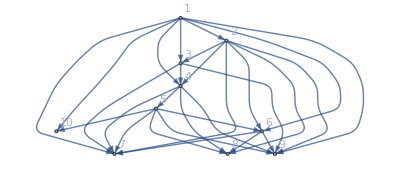

28

{0,0,0,0,0,0,28,24,38,10}

```mathematica
n=10;
destCount=4;
flow=100;
g= Graph[
Table[i,{i,n}],
Join[
Flatten[Table[i->j,{i,n-destCount-1},{j,RandomSample[Range[i+2,n-destCount],RandomInteger[n-i-destCount-1]]}]],
Table[i->i+1,{i,1,n-1-destCount}],
Flatten[Table[i->j,{j,n-destCount+1,n},{i,RandomSample[Range[n-destCount],RandomInteger[{1,n-destCount}]]}]]
],
VertexLabels->Table[i->i,{i,n}]
]
val=Sort[EdgeList[g]]; (*care arce sunt in graf*)
m=EdgeCount[g] (*numarul de arce*)

adjList=Join[{{0}},Sort[Gather[val,#1[[2]]==#2[[2]]&],#1[[1,2]]<#2[[1,2]]&][[All,All,1]]];

dest=Table[n-destCount+i,{i,destCount}];
flows = Differences[Flatten[{0,Sort[RandomSample[Range[flow-1],destCount-1]],flow}]];
(*Aici punem ce flux treb sa ajunga in fiecare destinatie*)
b=Table[0,n];
b[[n-destCount+1;;n]]=flows;(*marimea fluxului transmis din sursa spre destinatie*)
                                                (* b⟦1,2⟧=-1;b⟦n,2⟧=1;*)
b
X=Array[x,m];

(* Creaza un hash map care codeaza muchia cu pozitia ei in lista de muchii ---- Modul de codare este i*n + j pentru muchia i -> j *)
pos = SparseArray[MapIndexed[#⟦1⟧*n+#⟦2⟧->#2⟦1⟧&,val]];

lu=Table[{0,100},{i,m}];

γ=Table[RandomInteger[{1,5}],m];
δ=Table[RandomInteger[{1,5}],m];
f[j_Integer,x_]:=Piecewise[{{γ⟦j⟧ x, x≤δ⟦j⟧}, {γ⟦j⟧ δ⟦j⟧, x>δ⟦j⟧}, {0, True}}]
fd[j_Integer,x_]:=Piecewise[{{f[j,x]/x, x>0}, {γ⟦j⟧, x==0}, {0, True}}]
```

# Alg 3

```mathematica
(*Constante necesare pentru algoritm*)
prev=-1;(*Pentru epsilon*)
epsilon=0.0001;(*Pentru epsilon*)
numarIteratii=10;(*Pentru k iteratii*)
Do[
Print[Style["Test ","Section"],Style[bigCount,"Section"]];
thisTimer=Timing[
(*Generarea populatiei initiale*)
chromosomes= DeleteDuplicates[Table[Table[RandomChoice[adjList⟦i⟧]->i,{i,2,n}],{k,4*n}]];
chromosomeCount=Length[chromosomes];
(*Aflarea parintilor fiecarui nod*)

parents=Table[Flatten[{1,Sort[chromosomes[[i]],#1[[2]]<#2[[2]]&][[All,1]]}],{i,chromosomeCount}];
(*Aflarea solutiilor asociate*)
solutions=Table[
currentFlow=b;
currentX=Table[0,m];
currentSol=0;
DepthFirstScan[chromosomes⟦i⟧,1,"PostvisitVertex"->(
If[#≠parents⟦i⟧⟦#⟧,
edgeId=pos⟦parents⟦i⟧⟦#⟧*n+#⟧;
currentFlow⟦parents⟦i⟧⟦#⟧⟧+=currentFlow⟦#⟧;
currentX⟦edgeId⟧+=currentFlow⟦#⟧;
currentSol+=f[edgeId,currentFlow⟦#⟧];
]&)];
(*Print[{currentSol,currentX}];*)
currentSol
,{i,chromosomeCount}];
Print["Populatia initiala ",chromosomes];
Do[
Print["------------------------------------------------------------------"];
Print["Iteratia ",countIter];
(*Sortarea si alegerea cromozomilor parinti*)
chromosomes=chromosomes[[Ordering[solutions][[;;Quotient[chromosomeCount-Mod[chromosomeCount,4],2]]]]];
chromosomeCount=Length@chromosomes*2;
(*Aflarea parintilor fiecarui nod*)
parents=Table[Flatten[{1,Sort[chromosomes[[i]],#1[[2]]<#2[[2]]&][[All,1]]}],{i,chromosomeCount/2}];
(*Incrucisarea*)
children=Flatten[Table[
cutPoint=n-destCount+RandomInteger[{1,destCount-1}];
DestListLeft=Range[n-destCount+1,cutPoint];
DestListRight=Range[cutPoint+1,n];
edgeListLeft=Table[{},2];
edgeListRight=Table[{},2];
child=Table[{},2];
untouched=Table[{},2];
Do[
visitedVertices=Table[0,n];
visitedVertices[[DestListLeft]]=1;
visitedVertices[[DestListRight]]=2;
edgeListLeft⟦j-i+1⟧=Reap[DepthFirstScan[chromosomes⟦j⟧,1,"PostvisitVertex"->(
If[visitedVertices⟦#⟧==1&&#≠parents⟦i⟧⟦#⟧,
visitedVertices⟦parents⟦j⟧⟦#⟧⟧=1;
Sow[parents⟦j⟧⟦#⟧->#];
]&)]]⟦2,1⟧;
edgeListRight⟦j-i+1⟧=Reap[DepthFirstScan[chromosomes⟦j⟧,1,"PostvisitVertex"->(
If[visitedVertices⟦#⟧==2&&#≠parents⟦i⟧⟦#⟧,
visitedVertices⟦parents⟦j⟧⟦#⟧⟧=2;
Sow[parents⟦j⟧⟦#⟧->#];
]&)]]⟦2,1⟧;
,{j,i,i+1}];


child⟦1⟧=Union[edgeListLeft⟦1⟧,edgeListRight⟦2⟧];
child⟦2⟧=Union[edgeListLeft⟦2⟧,edgeListRight⟦1⟧];
untouched⟦1⟧=Complement[Range[n],child⟦1,All,2⟧];
untouched⟦2⟧=Complement[Range[n],child⟦2,All,2⟧];


Do[
If[untouched⟦j-i+1⟧=={},Continue[]];
visitedVertices=Table[0,n];
visitedVertices[[untouched⟦j-i+1⟧]]=1;
untouched⟦j-i+1⟧=Reap[DepthFirstScan[chromosomes⟦j⟧,1,"PostvisitVertex"->(
If[visitedVertices⟦#⟧==1,
visitedVertices⟦parents⟦j⟧⟦#⟧⟧=1;
Sow[parents⟦j⟧⟦#⟧->#];
]&)]]⟦2,1⟧;
,{j,i,i+1}];

child⟦1⟧=EdgeList@FindSpanningTree[Union[child⟦1⟧,untouched⟦1⟧]];
child⟦2⟧=EdgeList@FindSpanningTree[Union[child⟦2⟧,untouched⟦2⟧]];

{child⟦1⟧,child⟦2⟧}
,{i,1,chromosomeCount/2,2}],1];
chromosomes=Join[chromosomes,children];
Graph[#,VertexLabels->Automatic,GraphLayout->{"LayeredEmbedding","RootVertex"->1}]&/@chromosomes;
(*Mutatia*)
possibleVertices=DeleteCases[Table[If[Length@adjList[[i]]>1,i,0],{i,n}],0];
Do[
If[RandomReal[]<0.5,Continue[]];
chosenVertex=RandomChoice[possibleVertices];
chosenArc=Select[chromosomes⟦i⟧,#⟦2⟧==chosenVertex&];
chromosomes⟦i⟧=DeleteCases[chromosomes⟦i⟧,chosenArc[[1]]];
newParent=RandomChoice[Complement[adjList⟦chosenVertex⟧,{chosenArc⟦1,1⟧}]];
chromosomes⟦i⟧=Union[chromosomes⟦i⟧,{newParent->chosenVertex}];
,{i,chromosomeCount/2+1,chromosomeCount}];
Graph[#,VertexLabels->Automatic,GraphLayout->{"LayeredEmbedding","RootVertex"->1}]&/@chromosomes;
(*Aflarea parintilor fiecarui nod*)
parents=Table[Flatten[{1,Sort[chromosomes[[i]],#1[[2]]<#2[[2]]&][[All,1]]}],{i,chromosomeCount}];
(*Aflarea solutiilor asociate*)
bestSol=100000000000000000000;
bestX=Table[0,m];
solutions=Table[
currentFlow=b;
currentX=Table[0,m];
currentSol=0;
DepthFirstScan[chromosomes⟦i⟧,1,"PostvisitVertex"->(
If[#≠parents⟦i⟧⟦#⟧,

edgeId=pos⟦parents⟦i⟧⟦#⟧*n+#⟧;
currentFlow⟦parents⟦i⟧⟦#⟧⟧+=currentFlow⟦#⟧;
currentX⟦edgeId⟧+=currentFlow⟦#⟧;


currentSol+=f[edgeId,currentFlow⟦#⟧];
]&)];
If[bestSol>currentSol,bestSol=currentSol;bestX=currentX];
(*Print[{currentSol,currentX}];*)
currentSol
,{i,chromosomeCount}];
Print["Parintii si urmasii ",chromosomes];
Print["Cel mai bun cromozom ",chromosomes[[Ordering[solutions,1]]]];
Print["Cea mai buna solutie ",{Min[solutions],bestX}];
Print["Functia obiectiv totala ",Total[solutions]];
(*Print[Graph[#,VertexLabels->Automatic,GraphLayout->{"LayeredEmbedding","RootVertex"->1}]&/@chromosomes[[Ordering[solutions,1]]]];*)

,{countIter,numarIteratii}];
];
Print[thisTimer];
,{bigCount,1,10}]
```

Test 1

Populatia initiala {{1->2,2->3,2->4,4->5,5->6,4->7,5->8,6->9,1->10},{1->2,1->3,1->4,4->5,1->6,1->7,2->8,1->9,1->10},{1->2,2->3,2->4,4->5,2->6,5->7,2->8,4->9,5->10},{1->2,2->3,3->4,4->5,5->6,5->7,2->8,2->9,5->10},{1->2,2->3,3->4,4->5,2->6,5->7,4->8,1->9,5->10},{1->2,2->3,2->4,4->5,1->6,6->7,4->8,3->9,1->10},{1->2,1->3,3->4,4->5,1->6,4->7,2->8,4->9,5->10},{1->2,1->3,3->4,4->5,5->6,2->7,4->8,5->9,1->10},{1->2,2->3,1->4,4->5,5->6,1->7,2->8,4->9,5->10},{1->2,1->3,3->4,4->5,5->6,2->7,6->8,2->9,1->10},{1->2,1->3,1->4,4->5,2->6,4->7,2->8,5->9,1->10},{1->2,2->3,1->4,4->5,5->6,5->7,5->8,5->9,1->10},{1->2,2->3,1->4,4->5,2->6,4->7,2->8,4->9,1->10},{1->2,1->3,1->4,4->5,1->6,2->7,6->8,4->9,5->10},{1->2,1->3,1->4,4->5,1->6,4->7,4->8,3->9,5->10},{1->2,1->3,2->4,4->5,1->6,2->7,4->8,1->9,1->10},{1->2,1->3,2->4,4->5,5->6,1->7,6->8,3->9,1->10},{1->2,2->3,3->4,4->5,1->6,2->7,4->8,4->9,1->10},{1->2,1->3,3->4,4->5,2->6,1->7,2->8,5->9,5->10},{1->2,2->3,1->4,4->5,5->6,3->7,4->8,5->9,1->10},{1->2,1->3,3->4,4->5,1->6,4->7,5->8,6->9,1->10},{1->2,1->3,2->4,4->5,2->6,5->7,5->8,4->9,1->10},{1->2,2->3,2->4,4->5,2->6,3->7,4->8,2->9,5->10},{1->2,1->3,3->4,4->5,5->6,3->7,4->8,4->9,5->10},{1->2,2->3,1->4,4->5,2->6,5->7,5->8,5->9,1->10},{1->2,1->3,2->4,4->5,1->6,1->7,2->8,6->9,5->10},{1->2,1->3,1->4,4->5,1->6,2->7,2->8,1->9,1->10},{1->2,2->3,1->4,4->5,5->6,1->7,5->8,3->9,1->10},{1->2,1->3,2->4,4->5,1->6,2->7,5->8,3->9,5->10},{1->2,1->3,1->4,4->5,1->6,6->7,5->8,1->9,5->10},{1->2,1->3,3->4,4->5,1->6,4->7,6->8,2->9,5->10},{1->2,2->3,2->4,4->5,5->6,3->7,6->8,3->9,1->10},{1->2,2->3,2->4,4->5,5->6,4->7,5->8,4->9,5->10},{1->2,2->3,3->4,4->5,2->6,2->7,5->8,2->9,5->10},{1->2,2->3,3->4,4->5,1->6,5->7,5->8,4->9,1->10},{1->2,2->3,3->4,4->5,2->6,1->7,6->8,3->9,5->10},{1->2,1->3,2->4,4->5,5->6,2->7,2->8,6->9,5->10},{1->2,2->3,2->4,4->5,1->6,1->7,6->8,1->9,5->10},{1->2,1->3,3->4,4->5,5->6,4->7,4->8,2->9,1->10},{1->2,1->3,2->4,4->5,5->6,6->7,4->8,2->9,1->10}}

------------------------------------------------------------------

Iteratia 1

Parintii si urmasii {{1->2,2->3,2->4,4->5,5->6,4->7,5->8,4->9,5->10},{1->2,1->3,2->4,4->5,1->6,2->7,4->8,1->9,1->10},{1->2,1->3,2->4,4->5,2->6,5->7,5->8,4->9,1->10},{1->2,1->3,1->4,4->5,1->6,1->7,2->8,1->9,1->10},{1->2,1->3,1->4,4->5,1->6,2->7,2->8,1->9,1->10},{1->2,2->3,3->4,4->5,2->6,2->7,5->8,2->9,5->10},{1->2,2->3,3->4,4->5,1->6,2->7,4->8,4->9,1->10},{1->2,2->3,2->4,4->5,2->6,3->7,4->8,2->9,5->10},{1->2,2->3,2->4,4->5,1->6,1->7,6->8,1->9,5->10},{1->2,2->3,2->4,4->5,2->6,5->7,2->8,4->9,5->10},{1->2,1->3,3->4,4->5,5->6,3->7,4->8,4->9,5->10},{1->2,1->3,2->4,4->5,1->6,2->7,5->8,3->9,5->10},{1->2,2->3,3->4,4->5,1->6,5->7,5->8,4->9,1->10},{1->2,2->3,3->4,4->5,2->6,5->7,4->8,1->9,5->10},{1->2,2->3,1->4,4->5,5->6,1->7,2->8,4->9,5->10},{1->2,2->3,1->4,4->5,5->6,5->7,5->8,5->9,1->10},{1->2,2->3,1->4,4->5,2->6,5->7,5->8,5->9,1->10},{1->2,1->3,2->4,4->5,1->6,1->7,2->8,6->9,5->10},{1->2,1->3,3->4,4->5,5->6,2->7,4->8,5->9,1->10},{1->2,1->3,1->4,4->5,1->6,2->7,6->8,4->9,5->10},{1->2,1->10,2->3,2->4,4->5,4->7,5->6,5->8,6->9},{1->2,1->3,1->6,1->9,2->4,2->7,4->5,4->8,5->10},{1->2,1->3,1->9,1->10,2->4,2->6,4->5,5->7,5->8},{1->2,1->3,1->6,1->7,1->10,2->8,3->4,4->5,4->9},{1->2,1->3,1->6,2->7,2->8,2->9,3->4,4->5,5->10},{1->2,1->6,1->9,1->10,2->3,2->7,3->4,4->5,5->8},{1->2,1->6,2->3,2->4,2->7,2->9,4->5,4->8,5->10},{1->2,1->10,2->3,2->4,2->6,3->7,4->5,4->8,5->9},{1->2,1->6,1->7,2->3,2->4,2->9,4->5,5->10,6->8},{1->2,1->9,2->3,2->4,2->6,2->8,4->5,5->7,5->10},{1->2,1->3,1->6,2->4,3->7,4->5,4->8,4->9,5->10},{1->2,1->6,2->3,2->4,2->7,3->9,4->5,5->8,5->10},{1->2,1->6,1->9,2->3,3->4,4->5,5->7,5->8,5->10},{1->2,1->4,1->10,2->3,2->6,4->5,4->8,4->9,5->7},{1->2,1->4,1->7,1->10,2->3,2->8,3->9,4->5,5->6},{1->2,1->4,1->10,2->3,4->5,5->6,5->7,5->8,5->9},{1->2,2->3,2->6,3->4,4->5,5->7,5->8,5->9,5->10},{1->2,1->3,1->6,1->7,1->9,1->10,2->4,2->8,4->5},{1->2,1->3,1->4,2->7,4->5,4->8,4->9,5->6,5->10},{1->2,1->3,1->6,1->10,2->7,3->4,6->8,4->5,5->9}}

Cel mai bun cromozom {{1->2,2->3,2->4,4->5,5->6,4->7,5->8,4->9,5->10}}

Cea mai buna solutie {31,{100,0,0,0,0,0,0,0,100,0,0,0,0,0,0,0,34,28,0,38,0,0,24,0,10,0,0,0}}

Functia obiectiv totala 1994

------------------------------------------------------------------

Iteratia 2

Parintii si urmasii {{1->2,2->3,2->4,4->5,5->6,4->7,5->8,4->9,5->10},{1->2,1->3,1->6,1->9,2->4,2->7,4->5,4->8,5->10},{1->2,1->6,2->3,2->4,2->7,2->9,4->5,4->8,5->10},{1->2,1->3,2->4,4->5,1->6,2->7,4->8,1->9,1->10},{1->2,1->3,2->4,4->5,2->6,5->7,5->8,4->9,1->10},{1->2,1->3,1->4,4->5,1->6,1->7,2->8,1->9,1->10},{1->2,1->3,1->6,1->7,1->9,1->10,2->4,2->8,4->5},{1->2,1->3,1->4,4->5,1->6,2->7,2->8,1->9,1->10},{1->2,2->3,3->4,4->5,2->6,2->7,5->8,2->9,5->10},{1->2,2->3,3->4,4->5,1->6,2->7,4->8,4->9,1->10},{1->2,2->3,2->4,4->5,2->6,3->7,4->8,2->9,5->10},{1->2,2->3,2->4,4->5,1->6,1->7,6->8,1->9,5->10},{1->2,1->6,1->7,2->3,2->4,2->9,4->5,5->10,6->8},{1->2,1->3,1->6,2->4,3->7,4->5,4->8,4->9,5->10},{1->2,1->6,2->3,2->4,2->7,3->9,4->5,5->8,5->10},{1->2,1->3,1->4,2->7,4->5,4->8,4->9,5->6,5->10},{1->2,1->3,1->9,1->10,2->4,2->6,4->5,5->7,5->8},{1->2,2->3,2->4,4->5,2->6,5->7,2->8,4->9,5->10},{1->2,1->3,3->4,4->5,5->6,3->7,4->8,4->9,5->10},{1->2,1->10,2->3,2->4,2->6,3->7,4->5,4->8,5->9},{1->2,1->9,2->3,2->4,4->5,4->7,5->6,5->8,5->10},{1->2,1->3,1->6,1->10,2->4,2->7,4->5,4->8,4->9},{1->2,1->6,1->9,1->10,2->3,2->4,2->7,4->5,4->8},{1->2,1->3,1->6,2->4,2->7,2->9,4->5,4->8,5->10},{1->2,1->3,1->9,1->10,2->4,2->6,2->8,4->5,5->7},{1->2,1->3,1->6,1->7,1->10,2->4,4->5,4->9,5->8},{1->2,1->3,1->6,1->7,1->9,1->10,2->4,2->8,4->5},{1->2,1->3,1->4,1->6,1->9,1->10,2->7,2->8,4->5},{1->2,2->3,2->6,2->7,3->4,4->5,4->8,4->9,5->10},{1->2,1->6,2->3,2->7,2->9,3->4,4->5,5->8,5->10},{1->2,1->9,2->3,2->4,2->6,3->7,4->5,4->8,5->10},{1->2,1->3,1->6,1->7,2->4,2->9,4->5,5->10,6->8},{1->2,1->7,2->3,2->4,4->5,4->9,5->6,5->10,6->8},{1->2,1->3,2->4,2->9,3->7,4->5,4->8,5->6,5->10},{1->2,1->4,1->6,1->9,2->3,2->7,4->5,5->8,5->10},{1->2,1->4,2->3,2->7,4->5,4->8,4->9,5->6,5->10},{1->2,1->3,2->4,2->6,4->5,4->9,5->7,5->8,5->10},{1->2,1->9,1->10,2->3,2->4,2->6,2->8,4->5,5->7},{1->2,1->3,1->10,2->4,3->7,4->5,4->8,5->6,5->9},{1->2,1->3,1->10,2->6,3->4,3->7,4->5,4->8,4->9}}

Cel mai bun cromozom {{1->2,2->3,2->4,4->5,5->6,4->7,5->8,4->9,5->10}}

Cea mai buna solutie {31,{100,0,0,0,0,0,0,0,100,0,0,0,0,0,0,0,34,28,0,38,0,0,24,0,10,0,0,0}}

Functia obiectiv totala 1761

------------------------------------------------------------------

Iteratia 3

Parintii si urmasii {{1->2,2->3,2->4,4->5,5->6,4->7,5->8,4->9,5->10},{1->2,1->3,1->6,1->10,2->4,2->7,4->5,4->8,4->9},{1->2,1->3,1->6,1->7,1->10,2->4,4->5,4->9,5->8},{1->2,1->3,1->6,1->9,2->4,2->7,4->5,4->8,5->10},{1->2,1->6,2->3,2->4,2->7,2->9,4->5,4->8,5->10},{1->2,1->3,1->6,2->4,2->7,2->9,4->5,4->8,5->10},{1->2,1->3,2->4,2->6,4->5,4->9,5->7,5->8,5->10},{1->2,1->9,2->3,2->4,4->5,4->7,5->6,5->8,5->10},{1->2,1->3,2->4,4->5,1->6,2->7,4->8,1->9,1->10},{1->2,1->6,1->9,1->10,2->3,2->4,2->7,4->5,4->8},{1->2,1->3,2->4,4->5,2->6,5->7,5->8,4->9,1->10},{1->2,2->3,2->6,2->7,3->4,4->5,4->8,4->9,5->10},{1->2,1->3,1->4,4->5,1->6,1->7,2->8,1->9,1->10},{1->2,1->3,1->6,1->7,1->9,1->10,2->4,2->8,4->5},{1->2,1->3,1->6,1->7,1->9,1->10,2->4,2->8,4->5},{1->2,1->3,1->4,4->5,1->6,2->7,2->8,1->9,1->10},{1->2,2->3,3->4,4->5,2->6,2->7,5->8,2->9,5->10},{1->2,1->3,1->4,1->6,1->9,1->10,2->7,2->8,4->5},{1->2,1->6,2->3,2->7,2->9,3->4,4->5,5->8,5->10},{1->2,2->3,3->4,4->5,1->6,2->7,4->8,4->9,1->10},{1->2,1->10,2->3,2->4,2->8,4->5,4->7,4->9,5->6},{1->2,1->3,1->6,2->4,4->5,4->8,4->9,5->10,6->7},{1->2,1->3,1->6,2->4,3->7,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,1->9,1->10,2->4,2->7,4->5,4->8},{1->2,1->6,2->3,2->4,2->9,4->5,4->7,4->8,5->10},{1->2,1->3,1->6,2->4,2->7,4->5,4->8,4->9,5->10},{1->2,1->3,1->6,1->9,2->4,4->5,5->7,5->8,5->10},{1->2,2->3,2->4,4->5,4->7,4->9,5->6,5->8,5->10},{1->2,1->3,1->6,1->9,1->10,2->4,2->7,4->5,4->8},{1->2,1->6,1->9,1->10,2->3,2->4,2->7,4->5,4->8},{1->2,2->3,2->4,2->6,4->5,4->8,4->9,5->7,5->10},{1->2,1->10,2->3,2->4,2->6,2->7,4->5,4->9,5->8},{1->2,1->3,1->4,1->6,1->7,1->9,1->10,2->8,4->5},{1->2,1->3,1->6,1->7,1->10,2->4,2->8,4->5,5->9},{1->2,1->3,1->6,1->7,1->9,1->10,2->4,2->8,4->5},{1->2,1->3,1->4,1->6,1->9,1->10,2->8,4->5,4->7},{1->2,1->9,2->3,2->6,2->7,3->4,4->5,5->8,5->10},{1->2,1->6,2->3,2->7,2->8,2->9,3->4,4->5,5->10},{1->2,1->6,1->10,2->3,2->7,2->9,3->4,4->5,5->8},{1->2,1->6,2->3,2->7,3->4,4->5,4->8,4->9,5->10}}

Cel mai bun cromozom {{1->2,1->3,1->6,2->4,2->7,4->5,4->8,4->9,5->10}}

Cea mai buna solutie {30,{100,0,0,0,0,0,0,0,72,0,28,0,0,0,0,0,10,0,24,38,0,0,0,0,10,0,0,0}}

Functia obiectiv totala 1645

------------------------------------------------------------------

Iteratia 4

Parintii si urmasii {{1->2,1->3,1->6,2->4,2->7,4->5,4->8,4->9,5->10},{1->2,2->3,2->4,4->5,5->6,4->7,5->8,4->9,5->10},{1->2,2->3,2->4,4->5,4->7,4->9,5->6,5->8,5->10},{1->2,1->3,1->6,1->10,2->4,2->7,4->5,4->8,4->9},{1->2,1->3,1->6,1->7,1->10,2->4,4->5,4->9,5->8},{1->2,1->10,2->3,2->4,2->6,2->7,4->5,4->9,5->8},{1->2,1->3,1->6,1->9,2->4,2->7,4->5,4->8,5->10},{1->2,1->6,2->3,2->4,2->7,2->9,4->5,4->8,5->10},{1->2,1->3,1->6,2->4,2->7,2->9,4->5,4->8,5->10},{1->2,1->3,2->4,2->6,4->5,4->9,5->7,5->8,5->10},{1->2,1->9,2->3,2->4,4->5,4->7,5->6,5->8,5->10},{1->2,1->3,2->4,4->5,1->6,2->7,4->8,1->9,1->10},{1->2,1->6,1->9,1->10,2->3,2->4,2->7,4->5,4->8},{1->2,1->3,1->6,1->9,1->10,2->4,2->7,4->5,4->8},{1->2,1->3,1->6,1->9,1->10,2->4,2->7,4->5,4->8},{1->2,1->6,1->9,1->10,2->3,2->4,2->7,4->5,4->8},{1->2,2->3,2->4,2->6,4->5,4->8,4->9,5->7,5->10},{1->2,1->6,2->3,2->4,2->9,4->5,4->7,4->8,5->10},{1->2,1->3,1->6,1->9,2->4,4->5,5->7,5->8,5->10},{1->2,1->3,2->4,4->5,2->6,5->7,5->8,4->9,1->10},{1->2,1->3,1->6,2->4,2->7,4->5,4->9,5->8,5->10},{1->2,1->10,2->3,2->4,4->5,4->7,4->8,4->9,5->6},{1->2,2->3,2->4,4->5,4->7,4->9,5->6,5->8,5->10},{1->2,1->3,1->6,2->4,2->7,4->5,4->8,4->9,5->10},{1->2,1->3,1->6,1->7,1->10,2->4,4->5,4->9,5->8},{1->2,1->10,2->3,2->4,2->6,2->7,4->5,4->9,5->8},{1->2,1->6,1->9,2->3,2->4,2->7,4->5,4->8,5->10},{1->2,1->6,1->10,2->3,2->4,2->7,2->9,4->5,4->8},{1->2,1->6,2->3,2->4,2->7,4->5,4->8,4->9,5->10},{1->2,1->3,2->4,2->9,4->5,5->6,5->7,5->8,5->10},{1->2,1->4,1->9,1->10,2->3,4->5,4->7,5->6,5->8},{1->2,1->6,1->9,2->3,2->4,2->7,4->5,4->8,5->10},{1->2,1->6,1->9,1->10,2->3,2->4,2->7,4->5,4->8},{1->2,1->3,1->6,1->10,2->4,2->7,4->5,4->8,5->9},{1->2,1->3,1->6,1->9,1->10,2->4,2->7,4->5,4->8},{1->2,1->6,1->9,1->10,2->3,2->4,2->7,4->5,4->8},{1->2,2->3,2->4,2->6,2->9,3->7,4->5,4->8,5->10},{1->2,1->6,2->3,2->4,4->5,4->7,4->9,5->10,6->8},{1->2,1->3,1->6,1->10,2->4,4->5,4->9,5->7,5->8},{1->2,1->3,1->9,2->4,2->6,4->5,5->7,5->8,5->10}}

Cel mai bun cromozom {{1->2,1->3,1->6,2->4,2->7,4->5,4->9,5->8,5->10}}

Cea mai buna solutie {27,{100,0,0,0,0,0,0,0,72,0,28,0,0,0,0,0,34,0,0,38,0,0,24,0,10,0,0,0}}

Functia obiectiv totala 1467

------------------------------------------------------------------

Iteratia 5

Parintii si urmasii {{1->2,1->3,1->6,2->4,2->7,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,2->4,2->7,4->5,4->8,4->9,5->10},{1->2,1->3,1->6,2->4,2->7,4->5,4->8,4->9,5->10},{1->2,1->6,2->3,2->4,2->7,4->5,4->8,4->9,5->10},{1->2,2->3,2->4,4->5,5->6,4->7,5->8,4->9,5->10},{1->2,2->3,2->4,4->5,4->7,4->9,5->6,5->8,5->10},{1->2,2->3,2->4,4->5,4->7,4->9,5->6,5->8,5->10},{1->2,1->3,1->6,1->10,2->4,2->7,4->5,4->8,4->9},{1->2,1->3,1->6,1->7,1->10,2->4,4->5,4->9,5->8},{1->2,1->3,1->6,1->7,1->10,2->4,4->5,4->9,5->8},{1->2,1->10,2->3,2->4,2->6,2->7,4->5,4->9,5->8},{1->2,1->10,2->3,2->4,2->6,2->7,4->5,4->9,5->8},{1->2,1->3,1->6,1->9,2->4,2->7,4->5,4->8,5->10},{1->2,1->6,2->3,2->4,2->7,2->9,4->5,4->8,5->10},{1->2,1->3,1->6,2->4,2->7,2->9,4->5,4->8,5->10},{1->2,1->3,2->4,2->6,4->5,4->9,5->7,5->8,5->10},{1->2,1->6,1->9,2->3,2->4,2->7,4->5,4->8,5->10},{1->2,1->6,1->9,2->3,2->4,2->7,4->5,4->8,5->10},{1->2,1->9,2->3,2->4,4->5,4->7,5->6,5->8,5->10},{1->2,1->10,2->3,2->4,4->5,4->7,4->8,4->9,5->6},{1->2,1->3,1->6,1->10,2->4,2->7,4->5,4->8,4->9},{1->2,1->3,1->6,2->4,2->7,4->5,4->9,5->8,5->10},{1->2,1->3,2->4,2->7,4->5,4->8,4->9,5->6,5->10},{1->2,1->6,2->3,2->4,2->7,4->5,4->8,4->9,5->10},{1->2,2->3,2->4,4->5,4->7,4->9,5->6,5->8,5->10},{1->2,2->3,2->4,4->5,4->7,4->9,5->6,5->8,5->10},{1->2,1->10,2->3,2->4,4->5,4->7,4->9,5->6,5->8},{1->2,1->3,2->4,2->7,4->5,4->8,4->9,5->6,5->10},{1->2,1->3,1->6,1->7,1->10,2->4,4->5,4->9,5->8},{1->2,1->6,1->7,1->10,2->3,2->4,4->5,4->9,5->8},{1->2,1->10,2->3,2->4,2->6,2->7,4->5,4->9,5->8},{1->2,1->10,2->3,2->4,2->6,2->7,4->5,4->9,5->8},{1->2,1->3,1->6,1->9,2->4,2->7,4->5,4->8,5->10},{1->2,1->6,2->3,2->4,2->7,4->5,4->8,5->10,6->9},{1->2,1->3,1->6,2->4,2->7,2->9,4->5,4->8,5->10},{1->2,1->3,2->4,2->6,4->5,4->9,5->7,5->8,5->10},{1->2,1->6,1->9,2->3,2->4,2->7,4->5,4->8,5->10},{1->2,1->6,1->9,2->3,2->4,2->7,4->5,4->8,5->10},{1->2,2->3,2->4,4->5,4->7,4->9,5->6,5->8,5->10},{1->2,1->9,1->10,2->3,2->4,4->5,4->7,4->8,5->6}}

Cel mai bun cromozom {{1->2,1->3,1->6,2->4,2->7,4->5,4->9,5->8,5->10}}

Cea mai buna solutie {27,{100,0,0,0,0,0,0,0,72,0,28,0,0,0,0,0,34,0,0,38,0,0,24,0,10,0,0,0}}

Functia obiectiv totala 1339

------------------------------------------------------------------

Iteratia 6

Parintii si urmasii {{1->2,1->3,1->6,2->4,2->7,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,2->4,2->7,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,2->4,2->7,4->5,4->8,4->9,5->10},{1->2,1->3,1->6,2->4,2->7,4->5,4->8,4->9,5->10},{1->2,1->6,2->3,2->4,2->7,4->5,4->8,4->9,5->10},{1->2,1->3,2->4,2->7,4->5,4->8,4->9,5->6,5->10},{1->2,1->6,2->3,2->4,2->7,4->5,4->8,4->9,5->10},{1->2,1->3,2->4,2->7,4->5,4->8,4->9,5->6,5->10},{1->2,2->3,2->4,4->5,5->6,4->7,5->8,4->9,5->10},{1->2,2->3,2->4,4->5,4->7,4->9,5->6,5->8,5->10},{1->2,2->3,2->4,4->5,4->7,4->9,5->6,5->8,5->10},{1->2,2->3,2->4,4->5,4->7,4->9,5->6,5->8,5->10},{1->2,2->3,2->4,4->5,4->7,4->9,5->6,5->8,5->10},{1->2,2->3,2->4,4->5,4->7,4->9,5->6,5->8,5->10},{1->2,1->3,1->6,1->10,2->4,2->7,4->5,4->8,4->9},{1->2,1->3,1->6,1->7,1->10,2->4,4->5,4->9,5->8},{1->2,1->3,1->6,1->7,1->10,2->4,4->5,4->9,5->8},{1->2,1->3,1->6,1->10,2->4,2->7,4->5,4->8,4->9},{1->2,1->3,1->6,1->7,1->10,2->4,4->5,4->9,5->8},{1->2,1->6,1->7,1->10,2->3,2->4,4->5,4->9,5->8},{1->2,1->3,1->6,2->4,2->7,4->5,5->8,5->10,6->9},{1->2,1->3,1->6,2->4,2->7,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,1->7,2->4,4->5,4->8,4->9,5->10},{1->2,1->3,1->6,2->4,2->7,4->5,4->9,5->8,5->10},{1->2,1->6,2->3,2->4,2->7,2->8,4->5,4->9,5->10},{1->2,2->3,2->4,2->7,4->5,4->8,4->9,5->6,5->10},{1->2,1->6,2->3,2->4,2->7,4->5,4->8,4->9,5->10},{1->2,1->3,2->4,2->6,2->7,4->5,4->8,4->9,5->10},{1->2,2->3,2->4,4->5,4->7,5->6,5->8,5->9,5->10},{1->2,1->10,2->3,2->4,4->5,4->7,4->9,5->6,5->8},{1->2,2->3,2->4,4->5,4->7,4->9,5->6,5->8,5->10},{1->2,2->3,3->4,4->5,4->7,4->9,5->6,5->8,5->10},{1->2,2->3,2->4,4->5,4->7,4->9,5->6,5->8,5->10},{1->2,2->3,2->4,4->5,4->7,4->9,5->6,5->8,5->10},{1->2,1->3,1->6,1->10,2->7,3->4,4->5,4->8,4->9},{1->2,1->3,1->6,1->7,2->4,4->5,4->9,5->8,5->10},{1->2,1->3,1->7,1->10,2->4,4->5,4->9,5->6,5->8},{1->2,1->3,1->6,1->10,2->4,2->7,4->5,4->8,4->9},{1->2,1->3,1->6,1->7,1->10,2->4,4->5,4->9,5->8},{1->2,1->6,1->7,1->10,2->3,2->4,2->8,4->5,4->9}}

Cel mai bun cromozom {{1->2,1->3,1->6,1->7,2->4,4->5,4->9,5->8,5->10}}

Cea mai buna solutie {26,{72,0,0,0,28,0,0,0,72,0,0,0,0,0,0,0,34,0,0,38,0,0,24,0,10,0,0,0}}

Functia obiectiv totala 1300

------------------------------------------------------------------

Iteratia 7

Parintii si urmasii {{1->2,1->3,1->6,1->7,2->4,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,2->4,2->7,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,2->4,2->7,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,2->4,2->7,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,2->4,2->7,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,1->7,2->4,4->5,4->8,4->9,5->10},{1->2,1->3,1->6,2->4,2->7,4->5,4->8,4->9,5->10},{1->2,1->3,1->6,2->4,2->7,4->5,4->8,4->9,5->10},{1->2,1->6,2->3,2->4,2->7,4->5,4->8,4->9,5->10},{1->2,1->3,2->4,2->7,4->5,4->8,4->9,5->6,5->10},{1->2,1->6,2->3,2->4,2->7,4->5,4->8,4->9,5->10},{1->2,1->3,2->4,2->7,4->5,4->8,4->9,5->6,5->10},{1->2,2->3,2->4,2->7,4->5,4->8,4->9,5->6,5->10},{1->2,1->6,2->3,2->4,2->7,4->5,4->8,4->9,5->10},{1->2,1->3,2->4,2->6,2->7,4->5,4->8,4->9,5->10},{1->2,2->3,2->4,4->5,5->6,4->7,5->8,4->9,5->10},{1->2,2->3,2->4,4->5,4->7,4->9,5->6,5->8,5->10},{1->2,2->3,2->4,4->5,4->7,4->9,5->6,5->8,5->10},{1->2,2->3,2->4,4->5,4->7,4->9,5->6,5->8,5->10},{1->2,2->3,2->4,4->5,4->7,4->9,5->6,5->8,5->10},{1->2,1->3,1->4,1->6,1->7,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,2->4,2->7,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,2->4,2->7,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,2->4,2->7,4->5,4->9,5->8,5->10},{1->2,1->3,1->4,1->6,2->7,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,1->7,2->4,4->5,4->8,4->9,5->10},{1->2,1->3,1->6,2->4,4->5,4->7,4->8,4->9,5->10},{1->2,1->3,1->6,2->4,2->7,4->5,4->8,4->9,5->10},{1->2,1->6,1->10,2->3,2->4,2->7,4->5,4->8,4->9},{1->2,1->3,2->4,2->7,4->5,4->8,4->9,5->6,5->10},{1->2,1->6,2->3,2->4,2->7,4->5,4->8,4->9,5->10},{1->2,1->3,2->4,2->7,2->8,4->5,4->9,5->6,5->10},{1->2,2->3,2->4,2->7,4->5,4->8,4->9,5->6,5->10},{1->2,1->6,2->3,2->4,2->7,2->8,4->5,4->9,5->10},{1->2,1->3,2->4,2->6,2->7,4->5,4->8,4->9,5->10},{1->2,1->3,2->4,4->5,4->7,4->9,5->6,5->8,5->10},{1->2,2->3,2->4,4->5,4->7,4->9,5->6,5->8,5->10},{1->2,2->3,2->4,2->8,4->5,4->7,4->9,5->6,5->10},{1->2,1->6,2->3,2->4,4->5,4->7,4->9,5->8,5->10},{1->2,2->3,2->4,4->5,4->7,4->9,5->6,5->8,5->10}}

Cel mai bun cromozom {{1->2,1->3,1->6,1->7,2->4,4->5,4->9,5->8,5->10}}

Cea mai buna solutie {26,{72,0,0,0,28,0,0,0,72,0,0,0,0,0,0,0,34,0,0,38,0,0,24,0,10,0,0,0}}

Functia obiectiv totala 1243

------------------------------------------------------------------

Iteratia 8

Parintii si urmasii {{1->2,1->3,1->6,1->7,2->4,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,2->4,2->7,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,2->4,2->7,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,2->4,2->7,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,2->4,2->7,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,2->4,2->7,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,2->4,2->7,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,2->4,2->7,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,1->7,2->4,4->5,4->8,4->9,5->10},{1->2,1->3,1->6,1->7,2->4,4->5,4->8,4->9,5->10},{1->2,1->3,1->6,2->4,2->7,4->5,4->8,4->9,5->10},{1->2,1->3,1->6,2->4,2->7,4->5,4->8,4->9,5->10},{1->2,1->6,2->3,2->4,2->7,4->5,4->8,4->9,5->10},{1->2,1->3,2->4,2->7,4->5,4->8,4->9,5->6,5->10},{1->2,1->6,2->3,2->4,2->7,4->5,4->8,4->9,5->10},{1->2,1->3,2->4,2->7,4->5,4->8,4->9,5->6,5->10},{1->2,2->3,2->4,2->7,4->5,4->8,4->9,5->6,5->10},{1->2,1->6,2->3,2->4,2->7,4->5,4->8,4->9,5->10},{1->2,1->3,2->4,2->6,2->7,4->5,4->8,4->9,5->10},{1->2,1->3,1->6,2->4,2->7,4->5,4->8,4->9,5->10},{1->2,1->3,1->6,1->7,2->4,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,1->9,2->4,2->7,4->5,5->8,5->10},{1->2,1->3,1->6,2->4,2->7,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,2->4,2->7,2->8,4->5,4->9,5->10},{1->2,1->3,1->6,2->4,2->7,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,2->4,2->7,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,2->4,2->7,4->5,4->9,5->8,5->10},{1->2,1->3,2->4,2->6,2->7,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,1->7,2->4,4->5,4->8,4->9,5->10},{1->2,1->3,1->6,1->7,2->4,4->5,4->8,4->9,5->10},{1->2,1->3,1->6,2->4,2->7,4->5,4->8,5->9,5->10},{1->2,1->3,1->6,2->4,2->7,2->8,4->5,4->9,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->8,4->9,5->10},{1->2,1->3,2->4,2->7,4->5,4->8,4->9,5->6,5->10},{1->2,1->6,2->3,2->4,2->7,4->5,4->8,4->9,5->10},{1->2,1->3,2->4,2->7,4->5,4->8,4->9,5->6,5->10},{1->2,2->3,2->4,2->7,4->5,4->8,4->9,5->6,5->10},{1->2,1->6,2->3,2->4,2->7,4->5,4->8,4->9,5->10},{1->2,1->3,2->4,2->6,2->7,4->5,4->8,4->9,5->10},{1->2,1->3,1->6,2->4,2->7,4->5,4->8,4->9,5->10}}

Cel mai bun cromozom {{1->2,1->3,1->6,1->7,2->4,4->5,4->9,5->8,5->10}}

Cea mai buna solutie {26,{72,0,0,0,28,0,0,0,72,0,0,0,0,0,0,0,34,0,0,38,0,0,24,0,10,0,0,0}}

Functia obiectiv totala 1177

------------------------------------------------------------------

Iteratia 9

Parintii si urmasii {{1->2,1->3,1->6,1->7,2->4,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,1->7,2->4,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,2->4,2->7,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,2->4,2->7,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,2->4,2->7,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,2->4,2->7,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,2->4,2->7,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,2->4,2->7,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,2->4,2->7,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,2->4,2->7,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,2->4,2->7,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,2->4,2->7,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,2->4,2->7,4->5,4->9,5->8,5->10},{1->2,1->3,2->4,2->6,2->7,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,1->7,2->4,4->5,4->8,4->9,5->10},{1->2,1->3,1->6,1->7,2->4,4->5,4->8,4->9,5->10},{1->2,1->3,1->6,1->7,2->4,4->5,4->8,4->9,5->10},{1->2,1->3,1->6,1->7,2->4,4->5,4->8,4->9,5->10},{1->2,1->3,1->6,2->4,2->7,4->5,4->8,4->9,5->10},{1->2,1->3,1->6,2->4,2->7,4->5,4->8,4->9,5->10},{1->2,1->3,1->6,1->7,2->4,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,1->7,2->4,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,2->4,2->7,4->5,4->9,5->8,5->10},{1->2,1->3,2->4,2->6,2->7,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,2->4,2->7,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,2->4,2->7,4->5,4->9,5->10,6->8},{1->2,1->3,1->6,2->4,2->7,2->9,4->5,5->8,5->10},{1->2,1->3,1->6,2->4,2->7,3->9,4->5,5->8,5->10},{1->2,1->3,1->6,2->4,2->7,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,2->4,4->5,4->9,5->7,5->8,5->10},{1->2,1->3,1->6,2->4,2->7,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,2->4,2->7,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,2->4,2->7,4->5,4->9,5->8,5->10},{1->2,1->3,2->4,2->6,4->5,4->9,5->8,5->10,6->7},{1->2,1->3,1->6,1->7,2->4,4->5,4->8,4->9,5->10},{1->2,1->3,1->7,2->4,4->5,4->8,4->9,5->6,5->10},{1->2,1->3,1->6,1->7,1->10,2->4,4->5,4->8,4->9},{1->2,1->3,1->6,1->7,2->4,2->8,4->5,4->9,5->10},{1->2,1->3,1->6,2->4,2->7,4->5,4->8,4->9,5->10},{1->2,1->3,1->6,2->4,2->7,4->5,4->9,5->8,5->10}}

Cel mai bun cromozom {{1->2,1->3,1->6,1->7,2->4,4->5,4->9,5->8,5->10}}

Cea mai buna solutie {26,{72,0,0,0,28,0,0,0,72,0,0,0,0,0,0,0,34,0,0,38,0,0,24,0,10,0,0,0}}

Functia obiectiv totala 1176

------------------------------------------------------------------

Iteratia 10

Parintii si urmasii {{1->2,1->3,1->6,1->7,2->4,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,1->7,2->4,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,1->7,2->4,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,1->7,2->4,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,2->4,2->7,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,2->4,2->7,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,2->4,2->7,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,2->4,2->7,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,2->4,2->7,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,2->4,2->7,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,2->4,2->7,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,2->4,2->7,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,2->4,2->7,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,2->4,2->7,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,2->4,2->7,4->5,4->9,5->8,5->10},{1->2,1->3,2->4,2->6,2->7,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,2->4,2->7,4->5,4->9,5->8,5->10},{1->2,1->3,2->4,2->6,2->7,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,2->4,2->7,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,2->4,2->7,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,1->7,1->9,2->4,4->5,5->8,5->10},{1->2,1->3,1->6,1->7,2->4,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,1->7,2->4,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,1->7,2->4,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,1->7,2->4,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,1->9,2->4,2->7,4->5,5->8,5->10},{1->2,1->3,1->6,2->4,2->7,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,2->4,2->7,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,1->10,2->4,2->7,4->5,4->9,5->8},{1->2,1->6,2->3,2->4,2->7,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,2->7,3->4,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,2->4,2->7,2->8,4->5,4->9,5->10},{1->2,1->3,1->6,2->7,3->4,4->5,4->9,5->8,5->10},{1->2,1->3,1->4,1->6,2->7,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,2->4,2->7,4->5,4->9,5->8,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,2->4,2->7,4->5,4->9,5->8,5->10},{1->2,1->3,2->4,2->7,4->5,4->9,5->6,5->8,5->10},{1->2,1->3,1->6,1->10,2->4,2->7,4->5,4->9,5->8},{1->2,1->3,1->6,2->4,2->7,4->5,4->9,5->8,5->10}}

Cel mai bun cromozom {{1->2,1->3,1->6,1->7,2->4,4->5,4->9,5->8,5->10}}

Cea mai buna solutie {26,{72,0,0,0,28,0,0,0,72,0,0,0,0,0,0,0,34,0,0,38,0,0,24,0,10,0,0,0}}

Functia obiectiv totala 1158

{0.453125,Null}

Test 2

Populatia initiala {{1->2,1->3,1->4,4->5,2->6,3->7,6->8,4->9,5->10},{1->2,1->3,3->4,4->5,1->6,6->7,2->8,3->9,1->10},{1->2,2->3,3->4,4->5,2->6,4->7,6->8,5->9,1->10},{1->2,2->3,2->4,4->5,5->6,6->7,2->8,3->9,5->10},{1->2,2->3,3->4,4->5,5->6,3->7,5->8,3->9,1->10},{1->2,1->3,3->4,4->5,5->6,1->7,6->8,3->9,5->10},{1->2,2->3,1->4,4->5,1->6,5->7,2->8,2->9,5->10},{1->2,1->3,1->4,4->5,1->6,5->7,5->8,4->9,1->10},{1->2,2->3,3->4,4->5,1->6,1->7,2->8,1->9,1->10},{1->2,1->3,3->4,4->5,2->6,4->7,6->8,4->9,5->10},{1->2,1->3,3->4,4->5,2->6,2->7,2->8,4->9,5->10},{1->2,2->3,3->4,4->5,2->6,6->7,2->8,5->9,5->10},{1->2,2->3,1->4,4->5,5->6,4->7,5->8,3->9,5->10},{1->2,2->3,3->4,4->5,2->6,4->7,4->8,6->9,5->10},{1->2,1->3,3->4,4->5,1->6,3->7,5->8,6->9,1->10},{1->2,1->3,1->4,4->5,5->6,1->7,5->8,2->9,1->10},{1->2,2->3,2->4,4->5,1->6,4->7,4->8,4->9,5->10},{1->2,2->3,2->4,4->5,2->6,4->7,2->8,5->9,5->10},{1->2,1->3,1->4,4->5,2->6,1->7,2->8,4->9,5->10},{1->2,2->3,3->4,4->5,1->6,4->7,4->8,2->9,5->10},{1->2,1->3,1->4,4->5,5->6,3->7,5->8,2->9,1->10},{1->2,2->3,2->4,4->5,2->6,1->7,6->8,2->9,5->10},{1->2,1->3,2->4,4->5,1->6,3->7,6->8,4->9,1->10},{1->2,2->3,3->4,4->5,5->6,6->7,6->8,6->9,1->10},{1->2,2->3,1->4,4->5,1->6,1->7,5->8,2->9,1->10},{1->2,2->3,1->4,4->5,5->6,4->7,4->8,1->9,1->10},{1->2,1->3,2->4,4->5,5->6,2->7,6->8,3->9,5->10},{1->2,2->3,2->4,4->5,2->6,3->7,4->8,3->9,1->10},{1->2,2->3,2->4,4->5,2->6,5->7,2->8,1->9,5->10},{1->2,2->3,2->4,4->5,2->6,1->7,4->8,4->9,1->10},{1->2,1->3,3->4,4->5,1->6,2->7,6->8,3->9,1->10},{1->2,2->3,2->4,4->5,1->6,5->7,2->8,5->9,1->10},{1->2,1->3,1->4,4->5,5->6,3->7,4->8,6->9,5->10},{1->2,2->3,3->4,4->5,1->6,6->7,6->8,1->9,1->10},{1->2,2->3,3->4,4->5,2->6,2->7,4->8,4->9,1->10},{1->2,1->3,1->4,4->5,2->6,2->7,5->8,2->9,5->10},{1->2,1->3,3->4,4->5,1->6,2->7,4->8,5->9,5->10},{1->2,2->3,1->4,4->5,2->6,4->7,5->8,5->9,1->10},{1->2,1->3,2->4,4->5,1->6,4->7,5->8,6->9,5->10}}

------------------------------------------------------------------

Iteratia 1

Parintii si urmasii {{1->2,2->3,2->4,4->5,2->6,1->7,4->8,4->9,1->10},{1->2,2->3,2->4,4->5,1->6,4->7,4->8,4->9,5->10},{1->2,2->3,2->4,4->5,2->6,1->7,6->8,2->9,5->10},{1->2,2->3,3->4,4->5,1->6,1->7,2->8,1->9,1->10},{1->2,2->3,3->4,4->5,2->6,2->7,4->8,4->9,1->10},{1->2,2->3,2->4,4->5,2->6,4->7,2->8,5->9,5->10},{1->2,2->3,3->4,4->5,1->6,6->7,6->8,1->9,1->10},{1->2,1->3,1->4,4->5,2->6,2->7,5->8,2->9,5->10},{1->2,1->3,2->4,4->5,1->6,4->7,5->8,6->9,5->10},{1->2,1->3,3->4,4->5,1->6,2->7,4->8,5->9,5->10},{1->2,2->3,3->4,4->5,1->6,4->7,4->8,2->9,5->10},{1->2,2->3,1->4,4->5,2->6,4->7,5->8,5->9,1->10},{1->2,1->3,1->4,4->5,1->6,5->7,5->8,4->9,1->10},{1->2,1->3,3->4,4->5,2->6,4->7,6->8,4->9,5->10},{1->2,2->3,1->4,4->5,5->6,4->7,4->8,1->9,1->10},{1->2,2->3,2->4,4->5,2->6,5->7,2->8,1->9,5->10},{1->2,2->3,3->4,4->5,2->6,4->7,4->8,6->9,5->10},{1->2,1->3,1->4,4->5,5->6,1->7,5->8,2->9,1->10},{1->2,1->7,1->10,2->3,2->4,2->6,4->5,4->8,4->9},{1->2,1->6,1->10,2->3,2->4,4->5,4->8,4->9,6->7},{1->2,1->3,1->7,1->9,1->10,2->4,2->6,2->8,4->5},{1->2,2->3,2->4,2->6,2->7,2->9,4->5,5->10,6->8},{1->2,2->3,2->4,2->6,2->7,4->5,4->8,4->9,5->10},{1->2,1->10,2->3,2->4,2->6,2->8,4->5,4->7,5->9},{1->2,1->4,1->6,2->3,2->9,4->5,6->7,6->8,5->10},{1->2,1->4,1->9,1->10,2->3,2->6,2->7,4->5,5->8},{1->2,1->3,1->6,2->4,4->5,5->7,5->8,5->10,6->9},{1->2,1->3,1->6,2->4,3->7,4->5,4->8,5->9,5->10},{1->2,1->4,1->6,1->10,2->3,3->7,4->5,5->8,5->9},{1->2,1->4,2->3,2->6,2->9,4->5,4->7,4->8,5->10},{1->2,1->3,1->4,2->6,4->5,4->9,6->8,5->7,5->10},{1->2,1->3,1->10,2->4,2->6,4->5,4->7,4->9,5->8},{1->2,1->4,1->9,2->3,2->8,4->5,4->7,5->6,5->10},{1->2,1->9,1->10,2->3,2->4,2->6,4->5,4->8,5->7},{1->2,1->4,1->10,2->3,2->6,2->9,4->5,5->7,5->8},{1->2,1->7,2->3,2->6,3->4,6->9,4->5,4->8,5->10}}

Cel mai bun cromozom {{1->2,2->3,2->4,2->6,2->7,4->5,4->8,4->9,5->10}}

Cea mai buna solutie {30,{100,0,0,0,0,0,0,0,72,0,28,0,0,0,0,0,10,0,24,38,0,0,0,0,10,0,0,0}}

Functia obiectiv totala 1767

------------------------------------------------------------------

Iteratia 2

Parintii si urmasii {{1->2,2->3,2->4,2->6,2->7,4->5,4->8,4->9,5->10},{1->2,2->3,2->4,4->5,2->6,1->7,4->8,4->9,1->10},{1->2,1->7,1->10,2->3,2->4,2->6,4->5,4->8,4->9},{1->2,2->3,2->4,4->5,1->6,4->7,4->8,4->9,5->10},{1->2,2->3,2->4,4->5,2->6,1->7,6->8,2->9,5->10},{1->2,2->3,2->4,2->6,2->7,2->9,4->5,5->10,6->8},{1->2,1->3,1->10,2->4,2->6,4->5,4->7,4->9,5->8},{1->2,2->3,3->4,4->5,1->6,1->7,2->8,1->9,1->10},{1->2,1->3,1->7,1->9,1->10,2->4,2->6,2->8,4->5},{1->2,2->3,3->4,4->5,2->6,2->7,4->8,4->9,1->10},{1->2,2->3,2->4,4->5,2->6,4->7,2->8,5->9,5->10},{1->2,2->3,3->4,4->5,1->6,6->7,6->8,1->9,1->10},{1->2,1->3,1->4,4->5,2->6,2->7,5->8,2->9,5->10},{1->2,1->3,2->4,4->5,1->6,4->7,5->8,6->9,5->10},{1->2,1->3,1->6,2->4,3->7,4->5,4->8,5->9,5->10},{1->2,1->7,2->3,2->6,3->4,6->9,4->5,4->8,5->10},{1->2,1->3,3->4,4->5,1->6,2->7,4->8,5->9,5->10},{1->2,1->9,1->10,2->3,2->4,2->6,4->5,4->8,5->7},{1->2,1->10,2->3,2->4,2->6,2->7,4->5,4->8,4->9},{1->2,2->3,2->4,2->6,2->7,4->5,4->8,4->9,5->10},{1->2,1->7,2->3,2->4,2->6,3->9,4->5,4->8,5->10},{1->2,1->3,1->6,1->10,2->4,4->5,4->7,4->8,4->9},{1->2,1->7,1->10,2->3,2->4,2->6,2->9,4->5,6->8},{1->2,2->3,2->4,2->6,2->7,2->9,4->5,6->8,5->10},{1->2,1->3,1->10,2->4,2->6,4->5,4->7,4->9,5->8},{1->2,1->6,1->7,1->9,1->10,2->3,2->8,3->4,4->5},{1->2,1->7,1->10,2->3,2->4,2->6,4->5,4->8,4->9},{1->2,1->9,1->10,2->3,2->6,2->7,2->8,3->4,4->5},{1->2,1->3,1->10,2->4,2->6,2->8,4->5,4->7,5->9},{1->2,1->6,1->9,2->3,2->4,6->7,6->8,4->5,5->10},{1->2,1->3,1->4,1->6,2->7,4->5,6->9,5->8,5->10},{1->2,1->3,1->6,2->9,3->4,4->5,4->7,5->8,5->10},{1->2,1->3,2->6,3->4,3->7,6->9,4->5,4->8,5->10},{1->2,1->7,2->3,2->4,2->6,4->5,4->8,5->9,5->10},{1->2,1->3,1->10,2->6,2->7,3->4,4->5,4->8,5->9},{1->2,1->3,1->9,2->4,2->6,3->7,4->5,4->8,5->10}}

Cel mai bun cromozom {{1->2,2->3,2->4,2->6,2->7,4->5,4->8,4->9,5->10}}

Cea mai buna solutie {30,{100,0,0,0,0,0,0,0,72,0,28,0,0,0,0,0,10,0,24,38,0,0,0,0,10,0,0,0}}

Functia obiectiv totala 1556

------------------------------------------------------------------

Iteratia 3

Parintii si urmasii {{1->2,2->3,2->4,2->6,2->7,4->5,4->8,4->9,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->8,4->9,5->10},{1->2,2->3,2->4,4->5,2->6,1->7,4->8,4->9,1->10},{1->2,1->7,1->10,2->3,2->4,2->6,4->5,4->8,4->9},{1->2,1->7,1->10,2->3,2->4,2->6,4->5,4->8,4->9},{1->2,1->7,2->3,2->4,2->6,4->5,4->8,5->9,5->10},{1->2,1->10,2->3,2->4,2->6,2->7,4->5,4->8,4->9},{1->2,2->3,2->4,4->5,1->6,4->7,4->8,4->9,5->10},{1->2,1->7,1->10,2->3,2->4,2->6,2->9,4->5,6->8},{1->2,2->3,2->4,4->5,2->6,1->7,6->8,2->9,5->10},{1->2,2->3,2->4,2->6,2->7,2->9,4->5,5->10,6->8},{1->2,1->3,1->6,1->10,2->4,4->5,4->7,4->8,4->9},{1->2,2->3,2->4,2->6,2->7,2->9,4->5,6->8,5->10},{1->2,1->3,1->10,2->4,2->6,4->5,4->7,4->9,5->8},{1->2,1->3,1->10,2->4,2->6,4->5,4->7,4->9,5->8},{1->2,2->3,3->4,4->5,1->6,1->7,2->8,1->9,1->10},{1->2,1->3,1->7,1->9,1->10,2->4,2->6,2->8,4->5},{1->2,1->6,1->7,1->9,1->10,2->3,2->8,3->4,4->5},{1->2,2->3,2->4,2->6,2->7,4->5,4->8,4->9,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->8,4->9,5->10},{1->2,1->7,1->10,2->3,2->4,2->6,4->5,4->8,4->9},{1->2,1->4,1->7,1->10,2->3,2->6,4->5,4->8,4->9},{1->2,1->7,2->3,2->4,2->6,4->5,4->8,5->9,5->10},{1->2,1->7,1->10,2->3,2->4,2->6,4->5,4->8,4->9},{1->2,2->3,2->4,2->6,2->7,4->5,4->8,4->9,5->10},{1->2,1->6,1->10,2->3,2->4,4->5,4->7,4->8,4->9},{1->2,1->7,2->3,2->4,2->6,2->9,4->5,6->8,5->10},{1->2,1->7,1->10,2->3,2->4,2->6,2->9,4->5,6->8},{1->2,1->10,2->3,2->4,2->6,4->5,4->9,6->7,6->8},{1->2,1->3,1->6,2->4,2->9,4->5,4->7,4->8,5->10},{1->2,1->10,2->3,2->4,2->6,2->7,2->9,4->5,6->8},{1->2,1->3,1->6,2->4,4->5,4->7,4->9,5->8,5->10},{1->2,1->3,1->9,1->10,2->4,2->6,4->5,4->7,5->8},{1->2,1->6,1->7,1->10,2->3,2->4,2->8,4->5,4->9},{1->2,1->3,1->7,1->9,1->10,2->4,2->6,2->8,4->5},{1->2,1->6,1->7,1->9,1->10,2->3,3->4,4->5,6->8}}

Cel mai bun cromozom {{1->2,2->3,2->4,2->6,2->7,4->5,4->8,4->9,5->10}}

Cea mai buna solutie {30,{100,0,0,0,0,0,0,0,72,0,28,0,0,0,0,0,10,0,24,38,0,0,0,0,10,0,0,0}}

Functia obiectiv totala 1295

------------------------------------------------------------------

Iteratia 4

Parintii si urmasii {{1->2,2->3,2->4,2->6,2->7,4->5,4->8,4->9,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->8,4->9,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->8,4->9,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->8,4->9,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->8,4->9,5->10},{1->2,1->3,1->6,2->4,4->5,4->7,4->9,5->8,5->10},{1->2,2->3,2->4,4->5,2->6,1->7,4->8,4->9,1->10},{1->2,1->7,1->10,2->3,2->4,2->6,4->5,4->8,4->9},{1->2,1->7,1->10,2->3,2->4,2->6,4->5,4->8,4->9},{1->2,1->7,2->3,2->4,2->6,4->5,4->8,5->9,5->10},{1->2,1->7,1->10,2->3,2->4,2->6,4->5,4->8,4->9},{1->2,1->7,2->3,2->4,2->6,4->5,4->8,5->9,5->10},{1->2,1->7,1->10,2->3,2->4,2->6,4->5,4->8,4->9},{1->2,1->10,2->3,2->4,2->6,2->7,4->5,4->8,4->9},{1->2,2->3,2->4,4->5,1->6,4->7,4->8,4->9,5->10},{1->2,1->7,1->10,2->3,2->4,2->6,2->9,4->5,6->8},{1->2,1->7,1->10,2->3,2->4,2->6,2->9,4->5,6->8},{1->2,2->3,2->4,4->5,2->6,1->7,6->8,2->9,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->8,4->9,5->10},{1->2,1->10,2->3,2->4,2->6,2->7,4->5,4->8,4->9},{1->2,2->3,2->4,2->6,2->7,4->5,4->8,4->9,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->8,4->9,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->8,4->9,5->10},{1->2,1->3,1->6,2->4,4->5,4->7,4->9,5->8,5->10},{1->2,1->6,1->7,1->10,2->3,2->4,4->5,4->8,4->9},{1->2,1->7,1->10,2->3,2->4,2->6,4->5,4->8,4->9},{1->2,2->3,2->4,2->6,4->5,4->8,5->7,5->9,5->10},{1->2,1->7,1->10,2->3,2->4,2->6,4->5,4->8,4->9},{1->2,1->7,1->9,2->3,2->4,2->6,4->5,4->8,5->10},{1->2,1->7,1->10,2->3,2->4,2->6,4->5,4->8,4->9},{1->2,1->10,2->3,2->4,2->6,2->7,4->5,4->8,4->9},{1->2,1->10,2->3,2->4,2->6,4->5,4->7,4->8,4->9},{1->2,1->3,1->10,2->4,2->6,2->9,4->5,4->7,6->8},{1->2,1->7,2->3,2->4,2->6,2->9,4->5,4->8,5->10},{1->2,1->7,1->10,2->3,2->4,2->6,2->9,4->5,6->8},{1->2,1->7,1->10,2->3,2->4,2->6,2->9,4->5,6->8}}

Cel mai bun cromozom {{1->2,2->3,2->4,2->6,2->7,4->5,4->8,4->9,5->10}}

Cea mai buna solutie {30,{100,0,0,0,0,0,0,0,72,0,28,0,0,0,0,0,10,0,24,38,0,0,0,0,10,0,0,0}}

Functia obiectiv totala 1183

------------------------------------------------------------------

Iteratia 5

Parintii si urmasii {{1->2,2->3,2->4,2->6,2->7,4->5,4->8,4->9,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->8,4->9,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->8,4->9,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->8,4->9,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->8,4->9,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->8,4->9,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->8,4->9,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->8,4->9,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->8,4->9,5->10},{1->2,1->3,1->6,2->4,4->5,4->7,4->9,5->8,5->10},{1->2,1->3,1->6,2->4,4->5,4->7,4->9,5->8,5->10},{1->2,2->3,2->4,4->5,2->6,1->7,4->8,4->9,1->10},{1->2,1->7,1->10,2->3,2->4,2->6,4->5,4->8,4->9},{1->2,1->7,1->10,2->3,2->4,2->6,4->5,4->8,4->9},{1->2,1->7,2->3,2->4,2->6,4->5,4->8,5->9,5->10},{1->2,1->7,1->10,2->3,2->4,2->6,4->5,4->8,4->9},{1->2,1->7,2->3,2->4,2->6,4->5,4->8,5->9,5->10},{1->2,1->7,1->10,2->3,2->4,2->6,4->5,4->8,4->9},{1->2,1->4,2->3,2->6,2->7,4->5,4->8,4->9,5->10},{1->2,1->3,2->4,2->6,2->7,4->5,4->8,4->9,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->8,4->9,5->10},{1->2,1->3,2->4,2->6,2->7,4->5,4->8,4->9,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->9,5->10,6->8},{1->2,2->3,2->6,2->7,3->4,4->5,4->8,4->9,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->8,4->9,5->10},{1->2,2->3,2->6,2->7,3->4,4->5,4->8,4->9,5->10},{1->2,1->3,2->4,2->6,2->7,4->5,4->8,4->9,5->10},{1->2,1->3,1->6,2->4,4->5,4->7,5->8,5->10,6->9},{1->2,1->3,1->6,1->10,2->4,4->5,4->7,4->9,5->8},{1->2,1->7,2->3,2->4,2->6,4->5,4->8,4->9,5->10},{1->2,1->7,1->10,2->3,2->4,2->6,2->8,4->5,4->9},{1->2,1->7,1->10,2->3,2->4,2->6,4->5,4->8,4->9},{1->2,1->7,1->10,2->3,2->4,2->6,4->5,4->8,4->9},{1->2,1->7,2->3,2->4,2->6,4->5,4->8,5->9,5->10},{1->2,1->7,2->3,2->4,2->6,4->5,4->8,5->9,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->8,4->9,5->10}}

Cel mai bun cromozom {{1->2,1->7,2->3,2->4,2->6,4->5,4->8,4->9,5->10}}

Cea mai buna solutie {29,{72,0,0,0,28,0,0,0,72,0,0,0,0,0,0,0,10,0,24,38,0,0,0,0,10,0,0,0}}

Functia obiectiv totala 1182

------------------------------------------------------------------

Iteratia 6

Parintii si urmasii {{1->2,1->7,2->3,2->4,2->6,4->5,4->8,4->9,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->8,4->9,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->8,4->9,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->8,4->9,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->8,4->9,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->8,4->9,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->8,4->9,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->8,4->9,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->8,4->9,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->8,4->9,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->8,4->9,5->10},{1->2,1->3,2->4,2->6,2->7,4->5,4->8,4->9,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->8,4->9,5->10},{1->2,1->3,2->4,2->6,2->7,4->5,4->8,4->9,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->8,4->9,5->10},{1->2,1->3,2->4,2->6,2->7,4->5,4->8,4->9,5->10},{1->2,1->3,1->6,2->4,4->5,4->7,4->9,5->8,5->10},{1->2,1->3,1->6,2->4,4->5,4->7,4->9,5->8,5->10},{1->2,1->7,2->3,2->4,2->6,4->5,4->8,4->9,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->10,6->8},{1->2,2->3,2->4,2->7,4->5,4->8,4->9,5->6,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->8,4->9,5->10},{1->2,1->3,2->4,2->6,2->7,4->5,4->8,4->9,5->10},{1->2,1->9,2->3,2->4,2->6,2->7,4->5,4->8,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->8,4->9,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->8,4->9,5->10},{1->2,2->3,2->4,2->7,4->5,4->8,4->9,5->6,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->8,4->9,5->10},{1->2,1->3,2->4,2->6,2->7,4->5,4->8,4->9,5->10},{1->2,1->3,2->4,2->6,4->5,4->8,4->9,5->10,6->7},{1->2,2->3,2->4,2->6,2->7,4->5,4->8,4->9,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->8,4->9,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->8,4->9,5->10},{1->2,1->3,2->4,2->6,2->7,4->5,4->8,4->9,5->10},{1->2,1->3,1->6,2->4,4->5,4->7,4->9,5->8,5->10},{1->2,1->6,2->3,2->4,4->5,4->7,4->9,5->8,5->10}}

Cel mai bun cromozom {{1->2,1->7,2->3,2->4,2->6,4->5,4->8,4->9,5->10}}

Cea mai buna solutie {29,{72,0,0,0,28,0,0,0,72,0,0,0,0,0,0,0,10,0,24,38,0,0,0,0,10,0,0,0}}

Functia obiectiv totala 1107

------------------------------------------------------------------

Iteratia 7

Parintii si urmasii {{1->2,1->7,2->3,2->4,2->6,4->5,4->8,4->9,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->8,4->9,5->10},{1->2,1->7,2->3,2->4,2->6,4->5,4->8,4->9,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->8,4->9,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->8,4->9,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->8,4->9,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->8,4->9,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->8,4->9,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->8,4->9,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->8,4->9,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->8,4->9,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->8,4->9,5->10},{1->2,1->3,2->4,2->6,2->7,4->5,4->8,4->9,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->8,4->9,5->10},{1->2,1->3,2->4,2->6,2->7,4->5,4->8,4->9,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->8,4->9,5->10},{1->2,1->3,2->4,2->6,2->7,4->5,4->8,4->9,5->10},{1->2,2->3,2->4,2->7,4->5,4->8,4->9,5->6,5->10},{1->2,1->7,1->10,2->3,2->4,2->6,4->5,4->8,4->9},{1->2,1->6,1->7,2->3,2->4,4->5,4->8,4->9,5->10},{1->2,1->4,1->7,2->3,2->6,4->5,4->8,4->9,5->10},{1->2,1->6,2->3,2->4,2->7,4->5,4->8,4->9,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->8,4->9,5->10},{1->2,1->4,2->3,2->6,2->7,4->5,4->8,4->9,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->8,4->9,5->10},{1->2,2->3,2->6,2->7,3->4,4->5,4->8,4->9,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->9,5->10,6->8},{1->2,1->9,2->3,2->4,2->6,2->7,4->5,4->8,5->10},{1->2,1->3,2->4,2->6,2->7,4->5,4->8,4->9,5->10},{1->2,2->3,2->4,2->6,4->5,4->8,4->9,5->7,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->8,4->9,5->10},{1->2,2->3,2->4,2->6,2->7,2->9,4->5,4->8,5->10},{1->2,1->3,1->10,2->4,2->6,2->7,4->5,4->8,4->9},{1->2,2->3,2->4,2->6,2->7,4->5,4->8,4->9,5->10},{1->2,1->3,1->10,2->4,2->6,2->7,4->5,4->8,4->9},{1->2,2->3,2->7,3->4,4->5,4->8,4->9,5->6,5->10}}

Cel mai bun cromozom {{1->2,1->7,2->3,2->4,2->6,4->5,4->8,4->9,5->10}}

Cea mai buna solutie {29,{72,0,0,0,28,0,0,0,72,0,0,0,0,0,0,0,10,0,24,38,0,0,0,0,10,0,0,0}}

Functia obiectiv totala 1154

------------------------------------------------------------------

Iteratia 8

Parintii si urmasii {{1->2,1->7,2->3,2->4,2->6,4->5,4->8,4->9,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->8,4->9,5->10},{1->2,1->7,2->3,2->4,2->6,4->5,4->8,4->9,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->8,4->9,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->8,4->9,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->8,4->9,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->8,4->9,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->8,4->9,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->8,4->9,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->8,4->9,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->8,4->9,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->8,4->9,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->8,4->9,5->10},{1->2,1->3,2->4,2->6,2->7,4->5,4->8,4->9,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->8,4->9,5->10},{1->2,1->3,2->4,2->6,2->7,4->5,4->8,4->9,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->8,4->9,5->10},{1->2,1->3,2->4,2->6,2->7,4->5,4->8,4->9,5->10},{1->2,1->7,2->3,2->4,2->6,4->5,4->8,4->9,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->8,4->9,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->8,4->9,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->8,4->9,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->8,4->9,5->10},{1->2,2->3,2->6,2->7,3->4,4->5,4->8,4->9,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->8,4->9,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->8,4->9,5->10},{1->2,2->3,2->6,2->7,3->4,4->5,4->8,4->9,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->8,4->9,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->8,4->9,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->8,4->9,5->10},{1->2,1->6,2->3,2->4,2->7,4->5,4->8,4->9,5->10},{1->2,1->3,2->4,2->6,2->7,4->5,4->8,4->9,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->8,4->9,5->10},{1->2,1->3,1->4,2->6,2->7,4->5,4->8,4->9,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->9,5->8,5->10},{1->2,1->3,2->4,2->6,2->7,4->5,4->8,5->10,6->9}}

Cel mai bun cromozom {{1->2,2->3,2->4,2->6,2->7,4->5,4->9,5->8,5->10}}

Cea mai buna solutie {27,{100,0,0,0,0,0,0,0,72,0,28,0,0,0,0,0,34,0,0,38,0,0,24,0,10,0,0,0}}

Functia obiectiv totala 1118

------------------------------------------------------------------

Iteratia 9

Parintii si urmasii {{1->2,2->3,2->4,2->6,2->7,4->5,4->9,5->8,5->10},{1->2,1->7,2->3,2->4,2->6,4->5,4->8,4->9,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->8,4->9,5->10},{1->2,1->7,2->3,2->4,2->6,4->5,4->8,4->9,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->8,4->9,5->10},{1->2,1->7,2->3,2->4,2->6,4->5,4->8,4->9,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->8,4->9,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->8,4->9,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->8,4->9,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->8,4->9,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->8,4->9,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->8,4->9,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->8,4->9,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->8,4->9,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->8,4->9,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->8,4->9,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->8,4->9,5->10},{1->2,1->3,2->4,2->6,2->7,4->5,4->8,4->9,5->10},{1->2,2->3,2->6,2->7,3->4,4->5,4->9,5->8,5->10},{1->2,1->7,1->10,2->3,2->4,2->6,4->5,4->8,4->9},{1->2,1->7,2->3,2->4,2->6,4->5,4->8,4->9,5->10},{1->2,1->7,2->3,2->4,2->6,4->5,4->8,4->9,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->8,4->9,5->10},{1->2,1->7,2->3,2->4,2->6,4->5,4->8,4->9,5->10},{1->2,1->7,2->3,2->4,4->5,4->8,4->9,5->6,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->8,4->9,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->8,4->9,5->10},{1->2,1->10,2->3,2->4,2->6,2->7,4->5,4->8,4->9},{1->2,1->10,2->3,2->4,2->6,2->7,4->5,4->8,4->9},{1->2,2->3,2->4,2->6,2->7,4->5,4->8,4->9,5->10},{1->2,2->3,2->4,2->7,4->5,4->8,4->9,5->6,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->8,4->9,5->10},{1->2,2->3,2->4,2->6,4->5,4->8,4->9,5->10,6->7},{1->2,2->3,2->4,2->7,4->5,4->8,4->9,5->6,5->10},{1->2,2->3,2->4,2->6,2->7,2->8,4->5,4->9,5->10},{1->2,1->3,2->4,2->6,4->5,4->7,4->8,4->9,5->10}}

Cel mai bun cromozom {{1->2,2->3,2->4,2->6,2->7,4->5,4->9,5->8,5->10}}

Cea mai buna solutie {27,{100,0,0,0,0,0,0,0,72,0,28,0,0,0,0,0,34,0,0,38,0,0,24,0,10,0,0,0}}

Functia obiectiv totala 1106

------------------------------------------------------------------

Iteratia 10

Parintii si urmasii {{1->2,2->3,2->4,2->6,2->7,4->5,4->9,5->8,5->10},{1->2,1->7,2->3,2->4,2->6,4->5,4->8,4->9,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->8,4->9,5->10},{1->2,1->7,2->3,2->4,2->6,4->5,4->8,4->9,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->8,4->9,5->10},{1->2,1->7,2->3,2->4,2->6,4->5,4->8,4->9,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->8,4->9,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->8,4->9,5->10},{1->2,1->7,2->3,2->4,2->6,4->5,4->8,4->9,5->10},{1->2,1->7,2->3,2->4,2->6,4->5,4->8,4->9,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->8,4->9,5->10},{1->2,1->7,2->3,2->4,2->6,4->5,4->8,4->9,5->10},{1->2,1->7,2->3,2->4,4->5,4->8,4->9,5->6,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->8,4->9,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->8,4->9,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->8,4->9,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->8,4->9,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->8,4->9,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->9,5->8,5->10},{1->2,1->7,2->3,2->4,2->6,4->5,4->8,5->9,5->10},{1->2,1->6,1->7,1->10,2->3,2->4,4->5,4->8,4->9},{1->2,1->7,2->3,2->4,2->6,4->5,4->8,4->9,5->10},{1->2,1->6,2->3,2->4,2->7,4->5,4->8,4->9,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->8,4->9,5->10},{1->2,1->6,1->7,2->3,2->4,2->8,4->5,4->9,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->8,4->9,5->10},{1->2,1->7,2->3,2->4,2->6,4->5,4->8,4->9,5->10},{1->2,1->7,2->3,2->4,2->6,4->5,4->8,4->9,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->8,4->9,5->10},{1->2,1->7,2->3,2->4,2->6,2->9,4->5,4->8,5->10},{1->2,1->7,2->3,2->4,4->5,4->8,4->9,5->6,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->8,4->9,5->10},{1->2,1->9,2->3,2->4,2->6,2->7,4->5,4->8,5->10},{1->2,1->9,2->3,2->4,2->6,2->7,4->5,4->8,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->8,4->9,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->8,4->9,5->10}}

Cel mai bun cromozom {{1->2,2->3,2->4,2->6,2->7,4->5,4->9,5->8,5->10}}

Cea mai buna solutie {27,{100,0,0,0,0,0,0,0,72,0,28,0,0,0,0,0,34,0,0,38,0,0,24,0,10,0,0,0}}

Functia obiectiv totala 1081

{0.390625,Null}

Test 3

Populatia initiala {{1->2,1->3,1->4,4->5,1->6,6->7,4->8,6->9,5->10},{1->2,1->3,2->4,4->5,2->6,3->7,4->8,4->9,1->10},{1->2,1->3,1->4,4->5,2->6,3->7,6->8,2->9,5->10},{1->2,1->3,1->4,4->5,2->6,1->7,6->8,3->9,1->10},{1->2,1->3,1->4,4->5,1->6,4->7,4->8,3->9,1->10},{1->2,1->3,3->4,4->5,5->6,6->7,2->8,2->9,5->10},{1->2,2->3,1->4,4->5,1->6,2->7,2->8,3->9,5->10},{1->2,2->3,1->4,4->5,2->6,3->7,6->8,2->9,1->10},{1->2,1->3,1->4,4->5,1->6,4->7,6->8,1->9,1->10},{1->2,1->3,2->4,4->5,2->6,5->7,2->8,4->9,1->10},{1->2,1->3,3->4,4->5,2->6,4->7,5->8,4->9,5->10},{1->2,2->3,2->4,4->5,2->6,2->7,2->8,4->9,5->10},{1->2,1->3,3->4,4->5,1->6,2->7,2->8,1->9,5->10},{1->2,1->3,2->4,4->5,5->6,3->7,2->8,6->9,5->10},{1->2,1->3,2->4,4->5,2->6,3->7,4->8,6->9,1->10},{1->2,1->3,3->4,4->5,5->6,6->7,5->8,1->9,1->10},{1->2,2->3,2->4,4->5,1->6,4->7,6->8,4->9,1->10},{1->2,2->3,3->4,4->5,1->6,5->7,6->8,1->9,1->10},{1->2,2->3,1->4,4->5,2->6,4->7,2->8,5->9,1->10},{1->2,1->3,2->4,4->5,1->6,5->7,5->8,2->9,1->10},{1->2,1->3,2->4,4->5,5->6,6->7,6->8,2->9,5->10},{1->2,2->3,2->4,4->5,2->6,5->7,6->8,1->9,5->10},{1->2,1->3,1->4,4->5,1->6,5->7,5->8,5->9,1->10},{1->2,1->3,3->4,4->5,1->6,3->7,2->8,5->9,5->10},{1->2,2->3,2->4,4->5,5->6,2->7,4->8,5->9,1->10},{1->2,1->3,2->4,4->5,2->6,6->7,2->8,2->9,1->10},{1->2,2->3,3->4,4->5,5->6,1->7,6->8,6->9,5->10},{1->2,2->3,1->4,4->5,1->6,6->7,6->8,4->9,5->10},{1->2,2->3,3->4,4->5,5->6,1->7,4->8,3->9,5->10},{1->2,2->3,2->4,4->5,2->6,5->7,5->8,6->9,1->10},{1->2,1->3,1->4,4->5,5->6,6->7,6->8,1->9,5->10},{1->2,1->3,3->4,4->5,1->6,5->7,2->8,5->9,5->10},{1->2,2->3,2->4,4->5,5->6,3->7,5->8,5->9,1->10},{1->2,2->3,2->4,4->5,2->6,1->7,2->8,1->9,1->10},{1->2,2->3,1->4,4->5,1->6,4->7,2->8,5->9,1->10},{1->2,2->3,1->4,4->5,5->6,2->7,5->8,5->9,1->10},{1->2,2->3,3->4,4->5,2->6,4->7,2->8,6->9,5->10},{1->2,2->3,3->4,4->5,5->6,6->7,6->8,6->9,5->10},{1->2,1->3,1->4,4->5,1->6,6->7,6->8,3->9,5->10}}

------------------------------------------------------------------

Iteratia 1

Parintii si urmasii {{1->2,2->3,2->4,4->5,2->6,2->7,2->8,4->9,5->10},{1->2,2->3,2->4,4->5,5->6,2->7,4->8,5->9,1->10},{1->2,1->3,3->4,4->5,2->6,4->7,5->8,4->9,5->10},{1->2,2->3,2->4,4->5,2->6,1->7,2->8,1->9,1->10},{1->2,2->3,2->4,4->5,2->6,5->7,6->8,1->9,5->10},{1->2,2->3,1->4,4->5,2->6,3->7,6->8,2->9,1->10},{1->2,1->3,2->4,4->5,1->6,5->7,5->8,2->9,1->10},{1->2,2->3,2->4,4->5,5->6,3->7,5->8,5->9,1->10},{1->2,1->3,2->4,4->5,2->6,3->7,4->8,4->9,1->10},{1->2,2->3,2->4,4->5,1->6,4->7,6->8,4->9,1->10},{1->2,2->3,2->4,4->5,2->6,5->7,5->8,6->9,1->10},{1->2,2->3,1->4,4->5,5->6,2->7,5->8,5->9,1->10},{1->2,1->3,1->4,4->5,2->6,1->7,6->8,3->9,1->10},{1->2,1->3,2->4,4->5,2->6,5->7,2->8,4->9,1->10},{1->2,1->3,2->4,4->5,2->6,6->7,2->8,2->9,1->10},{1->2,1->3,2->4,4->5,2->6,3->7,4->8,6->9,1->10},{1->2,1->3,1->4,4->5,1->6,5->7,5->8,5->9,1->10},{1->2,2->3,3->4,4->5,5->6,1->7,4->8,3->9,5->10},{1->2,1->4,1->10,2->3,2->6,2->7,2->8,4->5,5->9},{1->2,2->3,2->4,2->7,4->5,4->8,4->9,5->6,5->10},{1->2,1->3,1->6,1->10,3->4,4->5,4->7,4->9,5->8},{1->2,1->3,1->7,1->9,2->6,2->8,3->4,4->5,5->10},{1->2,2->3,2->4,2->6,2->9,4->5,5->7,5->10,6->8},{1->2,1->9,2->3,2->4,2->6,3->7,4->5,5->8,5->10},{1->2,1->3,1->6,1->10,2->4,4->5,5->7,5->8,5->9},{1->2,1->10,2->3,2->4,2->9,3->7,4->5,5->6,5->8},{1->2,1->3,1->6,1->10,2->4,3->7,6->8,4->5,4->9},{1->2,1->6,1->10,2->3,2->4,4->5,4->8,4->9,6->7},{1->2,1->3,1->10,2->4,2->6,4->5,5->7,5->8,6->9},{1->2,1->4,2->3,2->7,4->5,5->6,5->8,5->9,5->10},{1->2,1->3,1->4,1->7,1->10,2->6,4->5,4->9,6->8},{1->2,1->3,1->10,2->4,2->6,2->8,4->5,5->7,6->9},{1->2,1->3,1->10,2->4,2->6,4->5,4->7,4->8,6->9},{1->2,1->3,1->10,2->4,2->6,2->8,2->9,3->7,4->5},{1->2,1->3,1->4,1->6,3->9,4->5,5->7,5->8,5->10},{1->2,1->4,1->7,1->10,2->3,4->5,4->8,5->6,5->9}}

Cel mai bun cromozom {{1->2,2->3,2->4,2->7,4->5,4->8,4->9,5->6,5->10}}

Cea mai buna solutie {30,{100,0,0,0,0,0,0,0,72,0,28,0,0,0,0,0,10,0,24,38,0,0,0,0,10,0,0,0}}

Functia obiectiv totala 1815

------------------------------------------------------------------

Iteratia 2

Parintii si urmasii {{1->2,2->3,2->4,2->7,4->5,4->8,4->9,5->6,5->10},{1->2,2->3,2->4,4->5,2->6,2->7,2->8,4->9,5->10},{1->2,2->3,2->4,4->5,5->6,2->7,4->8,5->9,1->10},{1->2,1->9,2->3,2->4,2->6,3->7,4->5,5->8,5->10},{1->2,1->3,3->4,4->5,2->6,4->7,5->8,4->9,5->10},{1->2,2->3,2->4,4->5,2->6,1->7,2->8,1->9,1->10},{1->2,2->3,2->4,4->5,2->6,5->7,6->8,1->9,5->10},{1->2,2->3,2->4,2->6,2->9,4->5,5->7,5->10,6->8},{1->2,1->3,1->6,1->10,2->4,4->5,5->7,5->8,5->9},{1->2,1->3,1->10,2->4,2->6,4->5,4->7,4->8,6->9},{1->2,2->3,1->4,4->5,2->6,3->7,6->8,2->9,1->10},{1->2,1->4,2->3,2->7,4->5,5->6,5->8,5->9,5->10},{1->2,1->3,2->4,4->5,1->6,5->7,5->8,2->9,1->10},{1->2,2->3,2->4,4->5,5->6,3->7,5->8,5->9,1->10},{1->2,1->3,2->4,4->5,2->6,3->7,4->8,4->9,1->10},{1->2,2->3,2->4,4->5,1->6,4->7,6->8,4->9,1->10},{1->2,1->10,2->3,2->4,2->9,3->7,4->5,5->6,5->8},{1->2,2->3,2->4,4->5,2->6,5->7,5->8,6->9,1->10},{1->2,2->3,2->4,2->7,2->9,4->5,4->8,5->6,5->10},{1->2,2->3,2->4,2->6,2->7,2->8,4->5,4->9,5->10},{1->2,2->3,2->4,2->7,4->5,4->8,5->6,5->9,5->10},{1->2,1->4,1->9,1->10,2->3,2->6,3->7,4->5,5->8},{1->2,1->3,1->10,2->6,2->8,3->4,4->5,4->7,4->9},{1->2,1->3,1->7,1->9,2->6,2->8,3->4,4->5,5->10},{1->2,1->9,2->3,2->4,2->6,4->5,6->8,5->7,5->10},{1->2,2->3,2->4,2->6,2->9,4->5,6->8,5->7,5->10},{1->2,1->3,1->10,2->4,2->6,4->5,6->9,5->7,5->8},{1->2,1->3,1->10,2->4,2->6,4->5,4->7,4->8,5->9},{1->2,1->4,2->3,2->6,4->5,3->7,6->8,5->9,5->10},{1->2,1->4,1->10,2->3,2->7,2->9,4->5,5->6,5->8},{1->2,1->3,1->6,1->10,2->4,4->5,5->7,5->9,6->8},{1->2,1->10,2->3,2->4,2->9,3->7,4->5,5->6,5->8},{1->2,1->3,1->10,2->6,3->4,3->7,4->5,4->8,4->9},{1->2,1->6,1->10,2->3,2->4,6->8,4->5,4->7,4->9},{1->2,1->10,2->3,2->6,3->4,3->7,4->5,5->8,6->9},{1->2,1->10,2->3,2->4,2->6,2->9,4->5,4->8,5->7}}

Cel mai bun cromozom {{1->2,2->3,2->4,2->7,4->5,4->8,4->9,5->6,5->10}}

Cea mai buna solutie {30,{100,0,0,0,0,0,0,0,72,0,28,0,0,0,0,0,10,0,24,38,0,0,0,0,10,0,0,0}}

Functia obiectiv totala 1714

------------------------------------------------------------------

Iteratia 3

Parintii si urmasii {{1->2,2->3,2->4,2->7,4->5,4->8,4->9,5->6,5->10},{1->2,2->3,2->4,2->7,4->5,4->8,5->6,5->9,5->10},{1->2,2->3,2->4,2->7,2->9,4->5,4->8,5->6,5->10},{1->2,2->3,2->4,4->5,2->6,2->7,2->8,4->9,5->10},{1->2,2->3,2->4,4->5,5->6,2->7,4->8,5->9,1->10},{1->2,2->3,2->4,2->6,2->7,2->8,4->5,4->9,5->10},{1->2,1->9,2->3,2->4,2->6,3->7,4->5,5->8,5->10},{1->2,1->3,3->4,4->5,2->6,4->7,5->8,4->9,5->10},{1->2,2->3,2->4,4->5,2->6,1->7,2->8,1->9,1->10},{1->2,1->3,1->10,2->4,2->6,4->5,4->7,4->8,5->9},{1->2,2->3,2->4,4->5,2->6,5->7,6->8,1->9,5->10},{1->2,2->3,2->4,2->6,2->9,4->5,5->7,5->10,6->8},{1->2,1->3,1->6,1->10,2->4,4->5,5->7,5->8,5->9},{1->2,1->3,1->10,2->4,2->6,4->5,4->7,4->8,6->9},{1->2,1->9,2->3,2->4,2->6,4->5,6->8,5->7,5->10},{1->2,2->3,2->4,2->6,2->9,4->5,6->8,5->7,5->10},{1->2,2->3,1->4,4->5,2->6,3->7,6->8,2->9,1->10},{1->2,1->4,2->3,2->7,4->5,5->6,5->8,5->9,5->10},{1->2,2->3,2->4,4->5,4->7,4->8,5->6,5->9,5->10},{1->2,1->10,2->3,2->4,2->7,4->5,4->8,4->9,5->6},{1->2,2->3,2->4,2->7,2->8,4->5,4->9,5->6,5->10},{1->2,2->3,2->4,2->6,2->7,2->9,4->5,4->8,5->10},{1->2,2->3,2->4,2->7,2->8,4->5,4->9,5->6,5->10},{1->2,1->10,2->3,2->4,2->6,2->7,2->8,4->5,5->9},{1->2,1->3,1->9,2->4,2->6,3->7,4->5,5->8,5->10},{1->2,1->3,2->4,2->6,4->5,4->7,4->9,5->8,5->10},{1->2,1->7,1->9,1->10,2->3,2->4,2->6,2->8,4->5},{1->2,1->3,1->10,2->4,2->6,4->5,4->7,4->8,5->9},{1->2,1->3,1->9,2->4,2->6,4->5,5->7,5->10,6->8},{1->2,2->3,2->4,2->6,2->9,4->5,6->8,5->7,5->10},{1->2,1->3,2->4,2->6,4->5,5->7,5->8,5->10,6->9},{1->2,1->3,2->4,2->6,4->5,4->7,4->8,5->9,5->10},{1->2,1->6,2->3,2->4,2->9,4->5,5->7,5->10,6->8},{1->2,1->9,2->3,2->4,2->6,4->5,4->7,5->10,6->8},{1->2,1->4,2->3,2->6,4->5,3->7,5->8,5->9,5->10},{1->2,1->4,1->10,2->3,2->6,2->9,3->7,4->5,6->8}}

Cel mai bun cromozom {{1->2,2->3,2->4,2->7,4->5,4->8,4->9,5->6,5->10}}

Cea mai buna solutie {30,{100,0,0,0,0,0,0,0,72,0,28,0,0,0,0,0,10,0,24,38,0,0,0,0,10,0,0,0}}

Functia obiectiv totala 1519

------------------------------------------------------------------

Iteratia 4

Parintii si urmasii {{1->2,2->3,2->4,2->7,4->5,4->8,4->9,5->6,5->10},{1->2,1->3,2->4,2->6,4->5,4->7,4->9,5->8,5->10},{1->2,2->3,2->4,2->7,4->5,4->8,5->6,5->9,5->10},{1->2,1->10,2->3,2->4,2->7,4->5,4->8,4->9,5->6},{1->2,2->3,2->4,2->7,2->9,4->5,4->8,5->6,5->10},{1->2,2->3,2->4,2->6,2->7,2->9,4->5,4->8,5->10},{1->2,2->3,2->4,4->5,4->7,4->8,5->6,5->9,5->10},{1->2,1->3,2->4,2->6,4->5,4->7,4->8,5->9,5->10},{1->2,2->3,2->4,4->5,2->6,2->7,2->8,4->9,5->10},{1->2,2->3,2->4,4->5,5->6,2->7,4->8,5->9,1->10},{1->2,2->3,2->4,2->6,2->7,2->8,4->5,4->9,5->10},{1->2,2->3,2->4,2->7,2->8,4->5,4->9,5->6,5->10},{1->2,2->3,2->4,2->7,2->8,4->5,4->9,5->6,5->10},{1->2,1->9,2->3,2->4,2->6,4->5,4->7,5->10,6->8},{1->2,1->9,2->3,2->4,2->6,3->7,4->5,5->8,5->10},{1->2,1->3,3->4,4->5,2->6,4->7,5->8,4->9,5->10},{1->2,2->3,2->4,4->5,2->6,1->7,2->8,1->9,1->10},{1->2,1->7,1->9,1->10,2->3,2->4,2->6,2->8,4->5},{1->2,2->3,2->4,2->7,4->5,4->8,4->9,5->6,5->10},{1->2,1->3,2->4,2->6,4->5,4->7,4->9,5->8,5->10},{1->2,1->4,1->10,2->3,2->7,4->5,4->8,4->9,5->6},{1->2,1->3,2->4,2->7,4->5,4->8,5->6,5->9,5->10},{1->2,1->3,2->4,2->7,2->9,4->5,4->8,5->6,5->10},{1->2,2->3,2->4,2->6,2->7,2->9,4->5,4->8,5->10},{1->2,1->3,2->4,4->5,4->7,4->8,5->6,5->9,5->10},{1->2,1->3,2->4,2->6,4->5,4->7,4->8,5->9,5->10},{1->2,1->10,2->3,2->4,2->6,2->7,2->8,4->5,5->9},{1->2,2->3,2->4,2->7,4->5,4->8,4->9,5->6,5->10},{1->2,1->3,2->4,2->6,2->7,2->8,4->5,4->9,5->10},{1->2,1->9,2->3,2->4,2->7,2->8,4->5,5->6,5->10},{1->2,2->3,2->4,2->7,2->8,4->5,4->9,5->6,5->10},{1->2,1->9,2->3,2->4,2->6,4->5,4->7,6->8,5->10},{1->2,1->3,1->9,2->4,2->6,3->7,4->5,5->8,5->10},{1->2,1->3,2->4,4->5,4->7,4->9,5->6,5->8,5->10},{1->2,1->3,1->7,1->9,1->10,2->4,2->6,2->8,4->5},{1->2,1->7,1->9,1->10,2->3,2->4,2->6,2->8,4->5}}

Cel mai bun cromozom {{1->2,2->3,2->4,2->7,4->5,4->8,4->9,5->6,5->10}}

Cea mai buna solutie {30,{100,0,0,0,0,0,0,0,72,0,28,0,0,0,0,0,10,0,24,38,0,0,0,0,10,0,0,0}}

Functia obiectiv totala 1380

------------------------------------------------------------------

Iteratia 5

Parintii si urmasii {{1->2,2->3,2->4,2->7,4->5,4->8,4->9,5->6,5->10},{1->2,2->3,2->4,2->7,4->5,4->8,4->9,5->6,5->10},{1->2,2->3,2->4,2->7,4->5,4->8,4->9,5->6,5->10},{1->2,1->3,2->4,2->6,4->5,4->7,4->9,5->8,5->10},{1->2,1->3,2->4,2->6,4->5,4->7,4->9,5->8,5->10},{1->2,1->3,2->4,4->5,4->7,4->9,5->6,5->8,5->10},{1->2,2->3,2->4,2->7,4->5,4->8,5->6,5->9,5->10},{1->2,1->10,2->3,2->4,2->7,4->5,4->8,4->9,5->6},{1->2,1->3,2->4,2->7,4->5,4->8,5->6,5->9,5->10},{1->2,2->3,2->4,2->7,2->9,4->5,4->8,5->6,5->10},{1->2,2->3,2->4,2->6,2->7,2->9,4->5,4->8,5->10},{1->2,1->3,2->4,2->7,2->9,4->5,4->8,5->6,5->10},{1->2,2->3,2->4,2->6,2->7,2->9,4->5,4->8,5->10},{1->2,2->3,2->4,4->5,4->7,4->8,5->6,5->9,5->10},{1->2,1->3,2->4,2->6,4->5,4->7,4->8,5->9,5->10},{1->2,1->3,2->4,4->5,4->7,4->8,5->6,5->9,5->10},{1->2,1->3,2->4,2->6,4->5,4->7,4->8,5->9,5->10},{1->2,2->3,2->4,4->5,2->6,2->7,2->8,4->9,5->10},{1->2,2->3,2->4,2->7,4->5,4->8,4->9,5->6,5->10},{1->2,2->3,2->4,2->7,4->5,4->8,4->9,5->6,5->10},{1->2,2->3,2->4,4->5,4->8,4->9,5->6,5->7,5->10},{1->2,1->3,1->7,2->4,2->6,4->5,4->9,5->8,5->10},{1->2,1->3,2->4,2->6,4->5,4->7,4->9,5->8,5->10},{1->2,1->3,2->4,4->5,4->7,4->9,5->6,5->8,5->10},{1->2,1->10,2->3,2->4,2->7,4->5,4->8,4->9,5->6},{1->2,2->3,2->4,2->7,4->5,4->8,5->6,5->9,5->10},{1->2,1->3,2->4,2->7,2->9,4->5,4->8,5->6,5->10},{1->2,2->3,2->4,4->5,4->8,5->6,5->7,5->9,5->10},{1->2,2->3,2->4,2->6,2->7,2->9,4->5,5->10,6->8},{1->2,1->3,2->4,2->7,2->9,4->5,4->8,5->6,5->10},{1->2,2->3,2->4,2->6,3->7,4->5,4->8,5->9,5->10},{1->2,2->3,2->4,2->9,4->5,4->7,4->8,5->6,5->10},{1->2,1->3,2->4,2->6,4->5,4->7,4->8,5->9,5->10},{1->2,1->3,2->4,3->7,4->5,4->8,5->6,5->9,5->10},{1->2,1->3,2->4,2->6,4->5,4->7,4->8,4->9,5->10},{1->2,2->3,2->4,2->6,2->7,2->8,4->5,5->9,5->10}}

Cel mai bun cromozom {{1->2,1->3,1->7,2->4,2->6,4->5,4->9,5->8,5->10}}

Cea mai buna solutie {26,{72,0,0,0,28,0,0,0,72,0,0,0,0,0,0,0,34,0,0,38,0,0,24,0,10,0,0,0}}

Functia obiectiv totala 1254

------------------------------------------------------------------

Iteratia 6

Parintii si urmasii {{1->2,1->3,1->7,2->4,2->6,4->5,4->9,5->8,5->10},{1->2,2->3,2->4,2->7,4->5,4->8,4->9,5->6,5->10},{1->2,2->3,2->4,2->7,4->5,4->8,4->9,5->6,5->10},{1->2,2->3,2->4,2->7,4->5,4->8,4->9,5->6,5->10},{1->2,2->3,2->4,2->7,4->5,4->8,4->9,5->6,5->10},{1->2,2->3,2->4,2->7,4->5,4->8,4->9,5->6,5->10},{1->2,1->3,2->4,2->6,4->5,4->7,4->9,5->8,5->10},{1->2,1->3,2->4,2->6,4->5,4->7,4->9,5->8,5->10},{1->2,1->3,2->4,4->5,4->7,4->9,5->6,5->8,5->10},{1->2,1->3,2->4,2->6,4->5,4->7,4->9,5->8,5->10},{1->2,1->3,2->4,4->5,4->7,4->9,5->6,5->8,5->10},{1->2,2->3,2->4,2->7,4->5,4->8,5->6,5->9,5->10},{1->2,1->10,2->3,2->4,2->7,4->5,4->8,4->9,5->6},{1->2,1->3,2->4,2->7,4->5,4->8,5->6,5->9,5->10},{1->2,1->10,2->3,2->4,2->7,4->5,4->8,4->9,5->6},{1->2,2->3,2->4,2->7,4->5,4->8,5->6,5->9,5->10},{1->2,1->3,2->4,2->6,4->5,4->7,4->8,4->9,5->10},{1->2,2->3,2->4,2->7,2->9,4->5,4->8,5->6,5->10},{1->2,1->3,2->4,2->6,4->5,4->9,5->7,5->8,5->10},{1->2,2->3,2->4,2->7,2->8,4->5,4->9,5->6,5->10},{1->2,2->3,2->4,2->7,4->5,4->8,4->9,5->6,5->10},{1->2,2->3,2->4,3->7,4->5,4->8,4->9,5->6,5->10},{1->2,2->3,2->4,2->7,4->5,4->8,4->9,5->6,5->10},{1->2,2->3,2->4,2->7,4->5,4->8,4->9,5->6,5->10},{1->2,2->3,2->4,2->6,4->5,4->7,4->9,5->8,5->10},{1->2,1->3,2->4,2->6,4->5,4->7,4->9,5->8,5->10},{1->2,1->3,1->6,2->4,4->5,4->7,4->9,5->8,5->10},{1->2,2->3,2->4,2->6,4->5,4->7,4->9,5->8,5->10},{1->2,2->3,2->4,4->5,4->7,5->6,5->8,5->9,5->10},{1->2,2->3,2->4,2->7,4->5,4->8,4->9,5->6,5->10},{1->2,1->10,2->3,2->4,2->7,4->5,4->8,5->6,5->9},{1->2,1->3,1->10,2->4,2->7,4->5,4->8,4->9,5->6},{1->2,1->4,2->3,2->7,4->5,4->8,5->6,5->9,5->10},{1->2,1->10,2->3,2->4,2->7,4->5,4->8,4->9,5->6},{1->2,1->3,1->4,2->6,2->9,4->5,4->7,4->8,5->10},{1->2,2->3,2->4,2->7,4->5,4->8,4->9,5->6,5->10}}

Cel mai bun cromozom {{1->2,1->3,1->7,2->4,2->6,4->5,4->9,5->8,5->10}}

Cea mai buna solutie {26,{72,0,0,0,28,0,0,0,72,0,0,0,0,0,0,0,34,0,0,38,0,0,24,0,10,0,0,0}}

Functia obiectiv totala 1198

------------------------------------------------------------------

Iteratia 7

Parintii si urmasii {{1->2,1->3,1->7,2->4,2->6,4->5,4->9,5->8,5->10},{1->2,2->3,2->4,2->7,4->5,4->8,4->9,5->6,5->10},{1->2,2->3,2->4,2->7,4->5,4->8,4->9,5->6,5->10},{1->2,2->3,2->4,2->7,4->5,4->8,4->9,5->6,5->10},{1->2,2->3,2->4,2->7,4->5,4->8,4->9,5->6,5->10},{1->2,2->3,2->4,2->7,4->5,4->8,4->9,5->6,5->10},{1->2,2->3,2->4,2->7,4->5,4->8,4->9,5->6,5->10},{1->2,2->3,2->4,2->7,4->5,4->8,4->9,5->6,5->10},{1->2,2->3,2->4,2->7,4->5,4->8,4->9,5->6,5->10},{1->2,2->3,2->4,2->7,4->5,4->8,4->9,5->6,5->10},{1->2,2->3,2->4,2->7,4->5,4->8,4->9,5->6,5->10},{1->2,1->3,2->4,2->6,4->5,4->7,4->9,5->8,5->10},{1->2,1->3,2->4,2->6,4->5,4->7,4->9,5->8,5->10},{1->2,1->3,2->4,4->5,4->7,4->9,5->6,5->8,5->10},{1->2,1->3,2->4,2->6,4->5,4->7,4->9,5->8,5->10},{1->2,1->3,2->4,4->5,4->7,4->9,5->6,5->8,5->10},{1->2,2->3,2->4,2->6,4->5,4->7,4->9,5->8,5->10},{1->2,1->3,2->4,2->6,4->5,4->7,4->9,5->8,5->10},{1->2,1->3,1->4,1->7,2->6,4->5,4->8,4->9,5->10},{1->2,2->3,2->4,2->7,4->5,4->9,5->6,5->8,5->10},{1->2,1->6,2->3,2->4,2->7,4->5,4->8,4->9,5->10},{1->2,2->3,2->4,2->7,4->5,4->8,4->9,5->6,5->10},{1->2,2->3,2->4,2->7,4->5,4->8,4->9,5->6,5->10},{1->2,2->3,2->4,2->7,4->5,4->8,4->9,5->6,5->10},{1->2,2->3,2->4,2->7,4->5,4->8,4->9,5->6,5->10},{1->2,2->3,2->4,2->7,4->5,4->8,4->9,5->6,5->10},{1->2,2->3,2->4,2->7,3->9,4->5,4->8,5->6,5->10},{1->2,1->10,2->3,2->4,2->7,4->5,4->8,4->9,5->6},{1->2,1->9,2->3,2->4,2->7,4->5,4->8,5->6,5->10},{1->2,1->3,2->4,2->6,4->5,4->7,4->8,4->9,5->10},{1->2,1->3,2->4,2->6,4->5,4->7,4->9,5->8,5->10},{1->2,1->3,2->4,4->5,4->7,4->9,5->6,5->8,5->10},{1->2,1->3,2->4,2->6,4->5,4->7,4->9,5->8,5->10},{1->2,1->3,2->4,4->5,4->7,4->9,5->6,5->8,5->10},{1->2,2->3,2->4,2->6,2->8,4->5,4->7,4->9,5->10},{1->2,1->3,2->4,2->6,4->5,4->7,4->9,5->8,5->10}}

Cel mai bun cromozom {{1->2,1->3,1->7,2->4,2->6,4->5,4->9,5->8,5->10}}

Cea mai buna solutie {26,{72,0,0,0,28,0,0,0,72,0,0,0,0,0,0,0,34,0,0,38,0,0,24,0,10,0,0,0}}

Functia obiectiv totala 1140

------------------------------------------------------------------

Iteratia 8

Parintii si urmasii {{1->2,1->3,1->7,2->4,2->6,4->5,4->9,5->8,5->10},{1->2,2->3,2->4,2->7,4->5,4->9,5->6,5->8,5->10},{1->2,2->3,2->4,2->7,4->5,4->8,4->9,5->6,5->10},{1->2,2->3,2->4,2->7,4->5,4->8,4->9,5->6,5->10},{1->2,2->3,2->4,2->7,4->5,4->8,4->9,5->6,5->10},{1->2,2->3,2->4,2->7,4->5,4->8,4->9,5->6,5->10},{1->2,2->3,2->4,2->7,4->5,4->8,4->9,5->6,5->10},{1->2,2->3,2->4,2->7,4->5,4->8,4->9,5->6,5->10},{1->2,2->3,2->4,2->7,4->5,4->8,4->9,5->6,5->10},{1->2,2->3,2->4,2->7,4->5,4->8,4->9,5->6,5->10},{1->2,2->3,2->4,2->7,4->5,4->8,4->9,5->6,5->10},{1->2,2->3,2->4,2->7,4->5,4->8,4->9,5->6,5->10},{1->2,1->6,2->3,2->4,2->7,4->5,4->8,4->9,5->10},{1->2,2->3,2->4,2->7,4->5,4->8,4->9,5->6,5->10},{1->2,2->3,2->4,2->7,4->5,4->8,4->9,5->6,5->10},{1->2,2->3,2->4,2->7,4->5,4->8,4->9,5->6,5->10},{1->2,2->3,2->4,2->7,4->5,4->8,4->9,5->6,5->10},{1->2,2->3,2->4,2->7,4->5,4->8,4->9,5->6,5->10},{1->2,1->3,1->7,2->4,2->6,4->5,4->9,5->8,5->10},{1->2,1->4,2->3,2->7,4->5,4->9,5->6,5->8,5->10},{1->2,2->3,2->4,2->7,4->5,4->9,5->6,5->8,5->10},{1->2,2->3,2->4,2->7,4->5,4->9,5->6,5->8,5->10},{1->2,2->3,2->4,2->7,4->5,4->8,4->9,5->6,5->10},{1->2,2->3,2->4,2->7,4->5,4->8,4->9,5->6,5->10},{1->2,2->3,2->4,2->7,4->5,4->8,4->9,5->6,5->10},{1->2,2->3,2->4,2->7,4->5,4->8,4->9,5->6,5->10},{1->2,2->3,2->4,2->7,4->5,4->8,4->9,5->6,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->8,4->9,5->10},{1->2,2->3,2->7,3->4,4->5,4->8,4->9,5->6,5->10},{1->2,1->4,2->3,2->7,4->5,4->8,4->9,5->6,5->10},{1->2,1->6,2->3,2->4,2->7,4->5,4->8,4->9,5->10},{1->2,2->3,2->4,2->7,4->5,4->8,4->9,5->6,5->10},{1->2,2->3,2->4,2->7,4->5,4->8,4->9,5->6,5->10},{1->2,2->3,2->4,2->7,4->5,4->8,4->9,5->6,5->10},{1->2,2->3,2->4,2->7,4->5,4->8,4->9,5->6,5->10},{1->2,2->3,2->4,2->7,4->5,4->8,4->9,5->6,5->10}}

Cel mai bun cromozom {{1->2,1->3,1->7,2->4,2->6,4->5,4->9,5->8,5->10}}

Cea mai buna solutie {26,{72,0,0,0,28,0,0,0,72,0,0,0,0,0,0,0,34,0,0,38,0,0,24,0,10,0,0,0}}

Functia obiectiv totala 1104

------------------------------------------------------------------

Iteratia 9

Parintii si urmasii {{1->2,1->3,1->7,2->4,2->6,4->5,4->9,5->8,5->10},{1->2,1->3,1->7,2->4,2->6,4->5,4->9,5->8,5->10},{1->2,2->3,2->4,2->7,4->5,4->9,5->6,5->8,5->10},{1->2,2->3,2->4,2->7,4->5,4->9,5->6,5->8,5->10},{1->2,2->3,2->4,2->7,4->5,4->9,5->6,5->8,5->10},{1->2,2->3,2->4,2->7,4->5,4->8,4->9,5->6,5->10},{1->2,2->3,2->4,2->7,4->5,4->8,4->9,5->6,5->10},{1->2,2->3,2->4,2->7,4->5,4->8,4->9,5->6,5->10},{1->2,2->3,2->4,2->7,4->5,4->8,4->9,5->6,5->10},{1->2,2->3,2->4,2->7,4->5,4->8,4->9,5->6,5->10},{1->2,2->3,2->4,2->7,4->5,4->8,4->9,5->6,5->10},{1->2,2->3,2->4,2->7,4->5,4->8,4->9,5->6,5->10},{1->2,2->3,2->4,2->7,4->5,4->8,4->9,5->6,5->10},{1->2,2->3,2->4,2->7,4->5,4->8,4->9,5->6,5->10},{1->2,2->3,2->4,2->7,4->5,4->8,4->9,5->6,5->10},{1->2,1->6,2->3,2->4,2->7,4->5,4->8,4->9,5->10},{1->2,2->3,2->4,2->7,4->5,4->8,4->9,5->6,5->10},{1->2,2->3,2->4,2->7,4->5,4->8,4->9,5->6,5->10},{1->2,1->7,2->3,2->4,2->6,4->5,4->9,5->8,5->10},{1->2,1->3,1->7,2->4,2->6,4->5,4->9,5->8,5->10},{1->2,2->3,2->7,3->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->4,2->3,2->7,4->5,4->9,5->6,5->8,5->10},{1->2,2->3,2->4,2->7,4->5,4->9,5->6,5->8,5->10},{1->2,1->6,2->3,2->4,2->7,4->5,4->8,4->9,5->10},{1->2,2->3,2->4,2->7,4->5,4->8,4->9,5->6,5->10},{1->2,2->3,2->4,2->7,2->8,4->5,4->9,5->6,5->10},{1->2,2->3,2->4,2->7,4->5,4->8,4->9,5->6,5->10},{1->2,1->10,2->3,2->4,2->7,4->5,4->8,4->9,5->6},{1->2,2->3,2->4,2->7,4->5,4->8,4->9,5->6,5->10},{1->2,2->3,2->4,2->7,4->5,4->8,4->9,5->6,5->10},{1->2,2->3,2->4,2->7,4->5,4->8,4->9,5->6,5->10},{1->2,2->3,2->4,2->7,4->5,4->8,5->6,5->9,5->10},{1->2,2->3,2->4,2->7,2->8,4->5,4->9,5->6,5->10},{1->2,1->6,2->3,2->4,4->5,4->8,4->9,5->7,5->10},{1->2,1->4,2->3,2->7,4->5,4->8,4->9,5->6,5->10},{1->2,2->3,2->4,2->7,4->5,4->8,4->9,5->6,5->10}}

Cel mai bun cromozom {{1->2,1->3,1->7,2->4,2->6,4->5,4->9,5->8,5->10}}

Cea mai buna solutie {26,{72,0,0,0,28,0,0,0,72,0,0,0,0,0,0,0,34,0,0,38,0,0,24,0,10,0,0,0}}

Functia obiectiv totala 1124

------------------------------------------------------------------

Iteratia 10

Parintii si urmasii {{1->2,1->3,1->7,2->4,2->6,4->5,4->9,5->8,5->10},{1->2,1->3,1->7,2->4,2->6,4->5,4->9,5->8,5->10},{1->2,1->7,2->3,2->4,2->6,4->5,4->9,5->8,5->10},{1->2,1->3,1->7,2->4,2->6,4->5,4->9,5->8,5->10},{1->2,2->3,2->4,2->7,4->5,4->9,5->6,5->8,5->10},{1->2,2->3,2->4,2->7,4->5,4->9,5->6,5->8,5->10},{1->2,2->3,2->4,2->7,4->5,4->9,5->6,5->8,5->10},{1->2,2->3,2->4,2->7,4->5,4->9,5->6,5->8,5->10},{1->2,2->3,2->4,2->7,4->5,4->8,4->9,5->6,5->10},{1->2,2->3,2->4,2->7,4->5,4->8,4->9,5->6,5->10},{1->2,2->3,2->4,2->7,4->5,4->8,4->9,5->6,5->10},{1->2,2->3,2->4,2->7,4->5,4->8,4->9,5->6,5->10},{1->2,2->3,2->4,2->7,4->5,4->8,4->9,5->6,5->10},{1->2,2->3,2->4,2->7,4->5,4->8,4->9,5->6,5->10},{1->2,2->3,2->4,2->7,4->5,4->8,4->9,5->6,5->10},{1->2,2->3,2->4,2->7,4->5,4->8,4->9,5->6,5->10},{1->2,2->3,2->4,2->7,4->5,4->8,4->9,5->6,5->10},{1->2,2->3,2->4,2->7,4->5,4->8,4->9,5->6,5->10},{1->2,1->3,1->7,2->4,2->6,2->8,4->5,4->9,5->10},{1->2,1->3,1->7,2->4,2->6,4->5,4->9,5->8,5->10},{1->2,1->7,2->3,2->4,2->6,4->5,4->9,5->8,5->10},{1->2,1->3,1->7,1->10,2->4,2->6,4->5,4->9,5->8},{1->2,1->10,2->3,2->4,2->7,4->5,4->9,5->6,5->8},{1->2,2->3,2->4,2->7,4->5,4->9,5->6,5->8,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->9,5->8,5->10},{1->2,2->3,2->4,2->7,4->5,4->9,5->6,5->8,5->10},{1->2,2->3,2->4,2->7,4->5,4->9,5->6,5->8,5->10},{1->2,2->3,2->4,2->7,2->8,4->5,4->9,5->6,5->10},{1->2,2->3,2->4,3->7,4->5,4->8,4->9,5->6,5->10},{1->2,2->3,2->4,2->7,4->5,4->8,4->9,5->6,5->10},{1->2,2->3,2->4,2->7,4->5,4->8,4->9,5->6,5->10},{1->2,2->3,2->4,2->7,4->5,4->9,5->6,5->10,6->8},{1->2,2->3,2->4,2->7,4->5,4->8,4->9,5->6,5->10},{1->2,2->3,2->7,3->4,4->5,4->8,4->9,5->6,5->10},{1->2,2->3,2->4,4->5,4->8,4->9,5->6,5->7,5->10},{1->2,1->3,2->4,2->7,4->5,4->8,4->9,5->6,5->10}}

Cel mai bun cromozom {{1->2,1->3,1->7,2->4,2->6,4->5,4->9,5->8,5->10}}

Cea mai buna solutie {26,{72,0,0,0,28,0,0,0,72,0,0,0,0,0,0,0,34,0,0,38,0,0,24,0,10,0,0,0}}

Functia obiectiv totala 1112

{0.40625,Null}

Test 4

Populatia initiala {{1->2,1->3,3->4,4->5,1->6,4->7,4->8,3->9,1->10},{1->2,2->3,3->4,4->5,5->6,5->7,2->8,3->9,5->10},{1->2,1->3,2->4,4->5,1->6,1->7,4->8,3->9,1->10},{1->2,1->3,2->4,4->5,1->6,3->7,6->8,2->9,1->10},{1->2,1->3,2->4,4->5,2->6,1->7,5->8,3->9,5->10},{1->2,1->3,2->4,4->5,5->6,4->7,6->8,6->9,1->10},{1->2,1->3,2->4,4->5,2->6,4->7,6->8,3->9,1->10},{1->2,1->3,2->4,4->5,1->6,5->7,4->8,4->9,1->10},{1->2,2->3,2->4,4->5,2->6,4->7,2->8,6->9,1->10},{1->2,1->3,1->4,4->5,1->6,1->7,5->8,5->9,1->10},{1->2,2->3,1->4,4->5,1->6,2->7,6->8,4->9,1->10},{1->2,2->3,2->4,4->5,1->6,5->7,5->8,6->9,5->10},{1->2,2->3,1->4,4->5,5->6,5->7,2->8,1->9,5->10},{1->2,1->3,1->4,4->5,5->6,6->7,6->8,6->9,5->10},{1->2,2->3,1->4,4->5,5->6,6->7,2->8,3->9,1->10},{1->2,1->3,2->4,4->5,5->6,5->7,4->8,4->9,1->10},{1->2,2->3,3->4,4->5,1->6,6->7,5->8,6->9,5->10},{1->2,2->3,1->4,4->5,1->6,6->7,5->8,2->9,1->10},{1->2,1->3,3->4,4->5,5->6,1->7,5->8,6->9,1->10},{1->2,2->3,2->4,4->5,5->6,2->7,5->8,4->9,5->10},{1->2,1->3,2->4,4->5,5->6,3->7,5->8,1->9,1->10},{1->2,2->3,2->4,4->5,5->6,3->7,4->8,4->9,1->10},{1->2,2->3,1->4,4->5,2->6,4->7,5->8,2->9,1->10},{1->2,1->3,2->4,4->5,1->6,6->7,5->8,1->9,5->10},{1->2,1->3,1->4,4->5,2->6,6->7,6->8,1->9,1->10},{1->2,2->3,3->4,4->5,2->6,2->7,2->8,4->9,1->10},{1->2,1->3,1->4,4->5,1->6,6->7,2->8,2->9,5->10},{1->2,2->3,3->4,4->5,5->6,5->7,6->8,4->9,1->10},{1->2,2->3,2->4,4->5,1->6,1->7,4->8,5->9,5->10},{1->2,2->3,3->4,4->5,5->6,4->7,6->8,6->9,1->10},{1->2,1->3,2->4,4->5,2->6,1->7,5->8,3->9,1->10},{1->2,2->3,1->4,4->5,2->6,2->7,5->8,5->9,5->10},{1->2,2->3,3->4,4->5,1->6,3->7,5->8,2->9,1->10},{1->2,2->3,3->4,4->5,5->6,3->7,5->8,4->9,1->10},{1->2,1->3,3->4,4->5,5->6,1->7,2->8,6->9,1->10},{1->2,1->3,2->4,4->5,1->6,3->7,6->8,2->9,5->10},{1->2,1->3,3->4,4->5,1->6,4->7,4->8,3->9,5->10},{1->2,1->3,1->4,4->5,2->6,6->7,6->8,6->9,1->10},{1->2,1->3,3->4,4->5,5->6,3->7,4->8,4->9,5->10},{1->2,1->3,2->4,4->5,2->6,6->7,6->8,1->9,5->10}}

------------------------------------------------------------------

Iteratia 1

Parintii si urmasii {{1->2,2->3,2->4,4->5,5->6,2->7,5->8,4->9,5->10},{1->2,2->3,2->4,4->5,1->6,1->7,4->8,5->9,5->10},{1->2,2->3,2->4,4->5,5->6,3->7,4->8,4->9,1->10},{1->2,1->3,1->4,4->5,2->6,6->7,6->8,1->9,1->10},{1->2,1->3,1->4,4->5,2->6,6->7,6->8,6->9,1->10},{1->2,1->3,2->4,4->5,1->6,5->7,4->8,4->9,1->10},{1->2,1->3,2->4,4->5,5->6,5->7,4->8,4->9,1->10},{1->2,1->3,2->4,4->5,2->6,6->7,6->8,1->9,5->10},{1->2,2->3,1->4,4->5,2->6,2->7,5->8,5->9,5->10},{1->2,1->3,1->4,4->5,1->6,1->7,5->8,5->9,1->10},{1->2,1->3,3->4,4->5,5->6,3->7,4->8,4->9,5->10},{1->2,1->3,2->4,4->5,2->6,1->7,5->8,3->9,5->10},{1->2,2->3,2->4,4->5,1->6,5->7,5->8,6->9,5->10},{1->2,1->3,2->4,4->5,1->6,6->7,5->8,1->9,5->10},{1->2,2->3,3->4,4->5,5->6,3->7,5->8,4->9,1->10},{1->2,1->3,2->4,4->5,5->6,3->7,5->8,1->9,1->10},{1->2,2->3,2->4,4->5,2->6,4->7,2->8,6->9,1->10},{1->2,2->3,3->4,4->5,2->6,2->7,2->8,4->9,1->10},{1->2,1->3,2->4,4->5,1->6,1->7,4->8,3->9,1->10},{1->2,1->3,2->4,4->5,2->6,1->7,5->8,3->9,1->10},{1->2,1->4,2->3,2->7,4->5,5->6,5->8,5->9,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->8,4->9,5->10},{1->2,1->10,2->3,2->4,3->7,4->5,4->8,4->9,5->6},{1->2,1->3,1->4,1->9,2->6,4->5,5->10,6->7,6->8},{1->2,1->3,1->4,1->7,1->10,2->6,4->5,4->9,6->8},{1->2,1->3,1->10,2->4,2->6,4->5,4->8,6->9,5->7},{1->2,1->3,1->10,2->4,4->5,4->8,4->9,5->6,5->7},{1->2,1->3,1->9,1->10,2->4,2->6,4->5,6->7,6->8},{1->2,1->4,1->10,2->3,2->6,2->7,4->5,5->8,5->9},{1->2,1->3,1->4,1->7,4->5,5->6,5->8,5->9,5->10},{1->2,1->3,2->4,3->7,4->5,4->8,4->9,5->6,5->10},{1->2,1->3,1->7,2->4,2->6,3->9,4->5,5->8,5->10},{1->2,1->6,1->9,2->3,2->4,4->5,5->7,5->8,5->10},{1->2,1->3,1->6,2->4,6->7,6->9,4->5,5->8,5->10},{1->2,1->9,1->10,2->3,3->4,3->7,4->5,5->6,5->8},{1->2,1->3,1->10,2->4,3->7,4->5,4->9,5->6,5->8},{1->2,1->6,1->10,2->3,2->4,2->8,4->5,4->7,4->9},{1->2,1->10,2->3,2->6,2->7,2->8,3->4,6->9,4->5},{1->2,1->3,1->6,1->7,1->10,2->4,3->9,4->5,5->8},{1->2,1->3,1->7,1->10,2->4,2->6,3->9,4->5,4->8}}

Cel mai bun cromozom {{1->2,2->3,2->4,4->5,5->6,2->7,5->8,4->9,5->10}}

Cea mai buna solutie {27,{100,0,0,0,0,0,0,0,72,0,28,0,0,0,0,0,34,0,0,38,0,0,24,0,10,0,0,0}}

Functia obiectiv totala 1913

------------------------------------------------------------------

Iteratia 2

Parintii si urmasii {{1->2,2->3,2->4,4->5,5->6,2->7,5->8,4->9,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->8,4->9,5->10},{1->2,2->3,2->4,4->5,1->6,1->7,4->8,5->9,5->10},{1->2,1->3,1->4,1->7,4->5,5->6,5->8,5->9,5->10},{1->2,1->6,1->9,2->3,2->4,4->5,5->7,5->8,5->10},{1->2,2->3,2->4,4->5,5->6,3->7,4->8,4->9,1->10},{1->2,1->10,2->3,2->4,3->7,4->5,4->8,4->9,5->6},{1->2,1->3,1->4,4->5,2->6,6->7,6->8,1->9,1->10},{1->2,1->3,1->4,4->5,2->6,6->7,6->8,6->9,1->10},{1->2,1->3,1->9,1->10,2->4,2->6,4->5,6->7,6->8},{1->2,1->3,2->4,4->5,1->6,5->7,4->8,4->9,1->10},{1->2,1->3,2->4,4->5,5->6,5->7,4->8,4->9,1->10},{1->2,1->3,2->4,4->5,2->6,6->7,6->8,1->9,5->10},{1->2,1->3,1->10,2->4,4->5,4->8,4->9,5->6,5->7},{1->2,1->3,2->4,3->7,4->5,4->8,4->9,5->6,5->10},{1->2,2->3,1->4,4->5,2->6,2->7,5->8,5->9,5->10},{1->2,1->4,2->3,2->7,4->5,5->6,5->8,5->9,5->10},{1->2,1->3,1->4,4->5,1->6,1->7,5->8,5->9,1->10},{1->2,1->6,1->10,2->3,2->4,2->8,4->5,4->7,4->9},{1->2,1->10,2->3,2->6,2->7,2->8,3->4,6->9,4->5},{1->2,1->10,2->3,2->4,2->7,4->5,4->8,4->9,5->6},{1->2,1->3,1->6,1->7,2->4,4->5,4->9,5->8,5->10},{1->2,1->4,1->6,1->7,1->10,2->3,4->5,4->8,5->9},{1->2,1->3,1->7,2->4,4->5,5->6,5->8,5->9,5->10},{1->2,1->6,1->9,1->10,2->3,2->4,4->5,5->7,5->8},{1->2,2->3,2->4,2->6,3->7,4->5,4->8,4->9,5->10},{1->2,1->10,2->3,2->4,3->7,4->5,4->8,4->9,5->6},{1->2,1->3,1->4,1->9,1->10,2->6,4->5,5->8,6->7},{1->2,1->3,1->4,1->9,1->10,2->6,2->7,4->5,6->8},{1->2,1->3,2->4,2->6,4->5,5->10,6->7,6->8,6->9},{1->2,1->3,1->6,1->10,2->4,4->5,4->8,5->7,5->9},{1->2,1->3,1->10,2->4,4->5,4->8,4->9,5->6,5->7},{1->2,1->3,2->4,2->6,4->5,4->8,4->9,5->10,6->7},{1->2,1->3,1->9,2->4,2->6,4->5,6->8,5->7,5->10},{1->2,1->3,3->4,3->7,4->5,5->6,5->8,5->9,5->10},{1->2,1->10,2->3,2->4,2->6,2->7,4->5,4->8,4->9},{1->2,1->4,1->10,2->3,2->7,4->5,5->6,5->8,5->9},{1->2,1->3,1->4,1->6,1->7,4->5,5->8,5->9,5->10},{1->2,1->6,1->10,2->3,2->4,2->8,4->5,4->9,5->7},{1->2,1->3,1->10,2->6,2->7,2->8,3->4,4->5,6->9}}

Cel mai bun cromozom {{1->2,1->3,1->6,1->7,2->4,4->5,4->9,5->8,5->10}}

Cea mai buna solutie {26,{72,0,0,0,28,0,0,0,72,0,0,0,0,0,0,0,34,0,0,38,0,0,24,0,10,0,0,0}}

Functia obiectiv totala 1714

------------------------------------------------------------------

Iteratia 3

Parintii si urmasii {{1->2,1->3,1->6,1->7,2->4,4->5,4->9,5->8,5->10},{1->2,2->3,2->4,4->5,5->6,2->7,5->8,4->9,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->8,4->9,5->10},{1->2,1->3,1->7,2->4,4->5,5->6,5->8,5->9,5->10},{1->2,2->3,2->4,4->5,1->6,1->7,4->8,5->9,5->10},{1->2,1->10,2->3,2->4,2->7,4->5,4->8,4->9,5->6},{1->2,1->10,2->3,2->4,2->6,2->7,4->5,4->8,4->9},{1->2,1->3,1->4,1->9,1->10,2->6,2->7,4->5,6->8},{1->2,1->3,1->4,1->7,4->5,5->6,5->8,5->9,5->10},{1->2,1->6,1->9,2->3,2->4,4->5,5->7,5->8,5->10},{1->2,2->3,2->4,2->6,3->7,4->5,4->8,4->9,5->10},{1->2,1->3,1->4,1->6,1->7,4->5,5->8,5->9,5->10},{1->2,1->3,2->4,2->6,4->5,4->8,4->9,5->10,6->7},{1->2,2->3,2->4,4->5,5->6,3->7,4->8,4->9,1->10},{1->2,1->10,2->3,2->4,3->7,4->5,4->8,4->9,5->6},{1->2,1->10,2->3,2->4,3->7,4->5,4->8,4->9,5->6},{1->2,1->3,1->4,4->5,2->6,6->7,6->8,1->9,1->10},{1->2,1->3,1->4,4->5,2->6,6->7,6->8,6->9,1->10},{1->2,1->3,1->9,1->10,2->4,2->6,4->5,6->7,6->8},{1->2,1->3,2->4,4->5,1->6,5->7,4->8,4->9,1->10},{1->2,1->3,1->6,1->7,2->4,4->5,4->9,5->8,5->10},{1->2,1->10,2->3,2->4,2->7,4->5,4->9,5->6,5->8},{1->2,1->3,1->6,1->7,2->4,4->5,4->8,4->9,5->10},{1->2,1->3,1->7,2->4,4->5,5->6,5->8,5->9,5->10},{1->2,1->6,1->7,1->10,2->3,2->4,4->5,4->8,4->9},{1->2,1->4,2->3,2->7,4->5,4->8,5->6,5->9,5->10},{1->2,1->3,1->9,1->10,2->4,2->6,2->7,4->5,6->8},{1->2,1->3,1->4,1->10,2->6,2->7,4->5,4->8,4->9},{1->2,1->3,1->4,1->7,4->5,5->6,5->8,5->9,5->10},{1->2,1->4,1->6,2->3,4->5,5->7,5->8,5->9,5->10},{1->2,1->4,2->3,2->6,4->5,3->7,5->8,5->9,5->10},{1->2,1->3,1->6,1->7,1->10,2->4,4->5,4->8,4->9},{1->2,1->3,1->10,2->4,2->6,4->5,4->8,4->9,5->7},{1->2,1->4,2->3,3->7,4->5,4->8,4->9,5->6,5->10},{1->2,1->4,1->10,2->3,3->7,4->5,4->8,4->9,5->6},{1->2,1->10,2->3,2->4,3->7,4->5,4->8,4->9,5->6},{1->2,1->3,1->4,1->10,2->6,4->5,6->7,6->8,6->9},{1->2,1->3,1->4,1->9,1->10,4->5,5->6,6->7,6->8},{1->2,1->3,1->10,2->4,2->6,4->5,6->7,6->8,6->9},{1->2,1->3,1->6,1->9,1->10,2->4,4->5,4->8,5->7}}

Cel mai bun cromozom {{1->2,1->3,1->6,1->7,2->4,4->5,4->9,5->8,5->10}}

Cea mai buna solutie {26,{72,0,0,0,28,0,0,0,72,0,0,0,0,0,0,0,34,0,0,38,0,0,24,0,10,0,0,0}}

Functia obiectiv totala 1639

------------------------------------------------------------------

Iteratia 4

Parintii si urmasii {{1->2,1->3,1->6,1->7,2->4,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,1->7,2->4,4->5,4->9,5->8,5->10},{1->2,2->3,2->4,4->5,5->6,2->7,5->8,4->9,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->8,4->9,5->10},{1->2,1->3,1->7,2->4,4->5,5->6,5->8,5->9,5->10},{1->2,1->3,1->6,1->7,2->4,4->5,4->8,4->9,5->10},{1->2,1->3,1->7,2->4,4->5,5->6,5->8,5->9,5->10},{1->2,2->3,2->4,4->5,1->6,1->7,4->8,5->9,5->10},{1->2,1->6,1->7,1->10,2->3,2->4,4->5,4->8,4->9},{1->2,1->3,1->6,1->7,1->10,2->4,4->5,4->8,4->9},{1->2,1->10,2->3,2->4,2->7,4->5,4->8,4->9,5->6},{1->2,1->10,2->3,2->4,2->6,2->7,4->5,4->8,4->9},{1->2,1->10,2->3,2->4,2->7,4->5,4->9,5->6,5->8},{1->2,1->3,1->4,1->9,1->10,2->6,2->7,4->5,6->8},{1->2,1->3,1->9,1->10,2->4,2->6,2->7,4->5,6->8},{1->2,1->3,1->4,1->7,4->5,5->6,5->8,5->9,5->10},{1->2,1->6,1->9,2->3,2->4,4->5,5->7,5->8,5->10},{1->2,2->3,2->4,2->6,3->7,4->5,4->8,4->9,5->10},{1->2,1->3,1->4,1->6,1->7,4->5,5->8,5->9,5->10},{1->2,1->3,1->4,1->7,4->5,5->6,5->8,5->9,5->10},{1->2,1->3,1->6,1->7,2->4,4->5,5->8,5->9,5->10},{1->2,1->3,1->6,1->7,1->10,2->4,4->5,4->9,5->8},{1->2,1->6,2->3,2->4,2->7,4->5,4->8,4->9,5->10},{1->2,1->4,1->6,1->7,2->3,4->5,4->9,5->8,5->10},{1->2,1->3,1->7,2->4,4->5,4->8,4->9,5->6,5->10},{1->2,1->3,1->6,1->7,2->4,4->5,5->8,5->9,5->10},{1->2,1->3,1->7,2->4,4->5,4->8,5->6,5->9,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,5->8,5->9,5->10},{1->2,1->6,1->7,1->10,2->3,2->4,4->5,4->8,4->9},{1->2,1->3,1->6,1->7,1->10,2->4,4->5,4->8,4->9},{1->2,1->6,1->10,2->3,2->4,2->7,4->5,4->8,4->9},{1->2,1->10,2->3,2->4,2->6,4->5,4->7,4->8,4->9},{1->2,1->9,1->10,2->3,2->6,2->7,3->4,4->5,6->8},{1->2,1->3,1->6,1->10,2->4,2->7,4->5,4->9,5->8},{1->2,1->4,2->3,2->6,2->7,4->5,5->8,5->9,5->10},{1->2,1->3,1->4,1->7,1->9,1->10,2->6,4->5,6->8},{1->2,1->6,2->3,2->4,4->5,4->9,5->7,5->8,5->10},{1->2,1->9,2->3,2->4,2->6,3->7,4->5,4->8,5->10},{1->2,1->3,1->4,1->6,1->7,4->5,5->8,5->9,5->10},{1->2,1->3,1->4,1->7,4->5,5->6,5->8,5->9,5->10}}

Cel mai bun cromozom {{1->2,1->3,1->6,1->7,2->4,4->5,4->9,5->8,5->10}}

Cea mai buna solutie {26,{72,0,0,0,28,0,0,0,72,0,0,0,0,0,0,0,34,0,0,38,0,0,24,0,10,0,0,0}}

Functia obiectiv totala 1356

------------------------------------------------------------------

Iteratia 5

Parintii si urmasii {{1->2,1->3,1->6,1->7,2->4,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,1->7,2->4,4->5,4->9,5->8,5->10},{1->2,2->3,2->4,4->5,5->6,2->7,5->8,4->9,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->8,4->9,5->10},{1->2,1->3,1->7,2->4,4->5,5->6,5->8,5->9,5->10},{1->2,1->3,1->6,1->7,2->4,4->5,4->8,4->9,5->10},{1->2,1->3,1->7,2->4,4->5,5->6,5->8,5->9,5->10},{1->2,1->3,1->6,1->7,2->4,4->5,5->8,5->9,5->10},{1->2,1->3,1->7,2->4,4->5,4->8,4->9,5->6,5->10},{1->2,1->3,1->6,1->7,2->4,4->5,5->8,5->9,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,5->8,5->9,5->10},{1->2,1->6,2->3,2->4,2->7,4->5,4->8,4->9,5->10},{1->2,2->3,2->4,4->5,1->6,1->7,4->8,5->9,5->10},{1->2,1->6,1->7,1->10,2->3,2->4,4->5,4->8,4->9},{1->2,1->3,1->6,1->7,1->10,2->4,4->5,4->8,4->9},{1->2,1->3,1->7,2->4,4->5,4->8,5->6,5->9,5->10},{1->2,1->6,1->7,1->10,2->3,2->4,4->5,4->8,4->9},{1->2,1->3,1->6,1->7,1->10,2->4,4->5,4->8,4->9},{1->2,1->10,2->3,2->4,2->7,4->5,4->8,4->9,5->6},{1->2,1->10,2->3,2->4,2->6,2->7,4->5,4->8,4->9},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,1->7,2->4,4->5,4->9,5->8,5->10},{1->2,2->3,2->4,2->7,4->5,4->8,4->9,5->6,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->8,4->9,5->10},{1->2,1->3,1->7,1->9,2->4,4->5,5->6,5->8,5->10},{1->2,1->3,1->6,1->7,2->4,3->9,4->5,4->8,5->10},{1->2,1->3,1->7,2->4,2->8,4->5,5->6,5->9,5->10},{1->2,1->3,1->6,1->7,2->4,4->5,5->8,5->9,5->10},{1->2,1->3,1->7,2->4,2->6,4->5,4->8,5->9,5->10},{1->2,1->3,1->6,1->7,3->4,4->5,4->9,5->8,5->10},{1->2,1->6,1->7,1->10,2->3,2->4,4->5,4->8,4->9},{1->2,1->6,2->3,2->4,2->7,4->5,5->8,5->9,5->10},{1->2,1->6,1->7,1->10,2->3,2->4,4->5,4->8,5->9},{1->2,1->6,1->7,2->3,2->4,4->5,4->8,4->9,5->10},{1->2,1->3,1->6,1->7,2->4,4->5,4->8,5->9,5->10},{1->2,1->7,1->10,2->3,2->4,4->5,4->8,4->9,5->6},{1->2,1->6,1->7,1->10,2->3,2->4,3->9,4->5,4->8},{1->2,1->3,1->6,1->10,2->4,4->5,4->7,4->8,4->9},{1->2,1->10,2->3,2->4,2->7,4->5,4->8,4->9,5->6},{1->2,1->9,1->10,2->3,2->4,2->6,2->7,4->5,4->8}}

Cel mai bun cromozom {{1->2,1->3,1->6,1->7,2->4,4->5,4->9,5->8,5->10}}

Cea mai buna solutie {26,{72,0,0,0,28,0,0,0,72,0,0,0,0,0,0,0,34,0,0,38,0,0,24,0,10,0,0,0}}

Functia obiectiv totala 1288

------------------------------------------------------------------

Iteratia 6

Parintii si urmasii {{1->2,1->3,1->6,1->7,2->4,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,1->7,2->4,4->5,4->9,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,1->7,2->4,4->5,4->9,5->8,5->10},{1->2,2->3,2->4,4->5,5->6,2->7,5->8,4->9,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->8,4->9,5->10},{1->2,1->3,1->7,2->4,4->5,5->6,5->8,5->9,5->10},{1->2,1->3,1->6,1->7,2->4,4->5,4->8,4->9,5->10},{1->2,1->3,1->7,2->4,4->5,5->6,5->8,5->9,5->10},{1->2,1->3,1->6,1->7,2->4,4->5,5->8,5->9,5->10},{1->2,1->3,1->7,2->4,4->5,4->8,4->9,5->6,5->10},{1->2,1->3,1->6,1->7,2->4,4->5,5->8,5->9,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,5->8,5->9,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->8,4->9,5->10},{1->2,1->3,1->6,1->7,2->4,4->5,5->8,5->9,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->8,4->9,5->10},{1->2,1->6,2->3,2->4,2->7,4->5,4->8,4->9,5->10},{1->2,2->3,2->4,2->7,4->5,4->8,4->9,5->6,5->10},{1->2,1->6,2->3,2->4,2->7,4->5,5->8,5->9,5->10},{1->2,1->3,1->7,1->9,2->4,4->5,5->6,5->8,5->10},{1->2,1->3,1->6,1->7,2->4,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,1->7,2->4,2->9,4->5,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,1->7,3->4,4->5,4->9,5->8,5->10},{1->2,1->6,2->3,2->4,2->7,4->5,4->8,4->9,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->3,1->7,1->10,2->4,4->5,5->6,5->8,5->9},{1->2,1->3,1->6,1->7,2->4,4->5,4->8,4->9,5->10},{1->2,1->3,1->7,2->4,4->5,5->6,5->8,5->9,5->10},{1->2,1->3,1->6,1->7,2->4,4->5,5->8,5->9,5->10},{1->2,1->3,1->7,2->4,4->5,5->6,5->8,5->9,5->10},{1->2,1->3,1->6,1->7,2->4,4->5,4->8,4->9,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->8,5->9,5->10},{1->2,1->3,1->6,1->7,2->4,4->5,5->8,5->9,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->8,4->9,5->10},{1->2,1->6,2->3,2->7,3->4,4->5,4->8,4->9,5->10},{1->2,2->3,2->4,2->7,2->8,4->5,4->9,5->6,5->10},{1->2,1->6,2->3,2->4,2->7,4->5,4->8,5->9,5->10},{1->2,1->3,1->7,1->9,1->10,2->4,4->5,5->6,5->8}}

Cel mai bun cromozom {{1->2,1->3,1->6,1->7,2->4,4->5,4->9,5->8,5->10}}

Cea mai buna solutie {26,{72,0,0,0,28,0,0,0,72,0,0,0,0,0,0,0,34,0,0,38,0,0,24,0,10,0,0,0}}

Functia obiectiv totala 1198

------------------------------------------------------------------

Iteratia 7

Parintii si urmasii {{1->2,1->3,1->6,1->7,2->4,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,1->7,2->4,4->5,4->9,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,1->7,2->4,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,1->7,2->4,4->5,4->9,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,2->3,2->4,4->5,5->6,2->7,5->8,4->9,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->8,4->9,5->10},{1->2,1->3,1->7,2->4,4->5,5->6,5->8,5->9,5->10},{1->2,1->3,1->6,1->7,2->4,4->5,4->8,4->9,5->10},{1->2,1->3,1->7,2->4,4->5,5->6,5->8,5->9,5->10},{1->2,1->3,1->6,1->7,2->4,4->5,5->8,5->9,5->10},{1->2,1->3,1->7,2->4,4->5,4->8,4->9,5->6,5->10},{1->2,1->3,1->6,1->7,2->4,4->5,5->8,5->9,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,5->8,5->9,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->8,4->9,5->10},{1->2,1->3,1->6,1->7,2->4,4->5,5->8,5->9,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->8,4->9,5->10},{1->2,1->3,1->6,1->7,2->4,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,1->7,2->4,4->5,4->9,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,1->7,3->4,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,1->7,2->4,4->5,4->9,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->6,1->7,2->3,3->4,4->5,4->9,5->8,5->10},{1->2,2->3,2->4,2->7,4->5,4->8,4->9,5->6,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->3,1->7,2->4,2->8,4->5,4->9,5->6,5->10},{1->2,1->3,1->6,2->4,2->7,4->5,4->8,5->9,5->10},{1->2,1->3,1->7,2->4,4->5,5->6,5->8,5->9,5->10},{1->2,1->3,1->7,2->4,4->5,5->6,5->8,5->9,5->10},{1->2,1->3,1->7,2->4,4->5,4->8,5->6,5->10,6->9},{1->2,1->3,1->6,1->7,2->4,4->5,5->8,5->9,5->10},{1->2,1->3,1->6,1->7,2->4,4->5,4->8,4->9,5->10},{1->2,1->7,2->3,2->4,2->6,4->5,5->8,5->9,5->10},{1->2,1->3,1->6,1->7,1->10,2->4,4->5,5->8,5->9},{1->2,1->6,1->7,2->3,3->4,4->5,4->8,4->9,5->10}}

Cel mai bun cromozom {{1->2,1->3,1->6,1->7,2->4,4->5,4->9,5->8,5->10}}

Cea mai buna solutie {26,{72,0,0,0,28,0,0,0,72,0,0,0,0,0,0,0,34,0,0,38,0,0,24,0,10,0,0,0}}

Functia obiectiv totala 1195

------------------------------------------------------------------

Iteratia 8

Parintii si urmasii {{1->2,1->3,1->6,1->7,2->4,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,1->7,2->4,4->5,4->9,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,1->7,2->4,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,1->7,2->4,4->5,4->9,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,1->7,2->4,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,1->7,2->4,4->5,4->9,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,1->7,2->4,4->5,4->9,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,2->3,2->4,4->5,5->6,2->7,5->8,4->9,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->8,4->9,5->10},{1->2,1->3,1->7,2->4,4->5,5->6,5->8,5->9,5->10},{1->2,1->3,1->6,1->7,2->4,4->5,4->8,4->9,5->10},{1->2,1->3,1->7,2->4,4->5,5->6,5->8,5->9,5->10},{1->2,1->3,1->6,1->7,3->4,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,1->7,2->4,4->5,4->9,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,2->4,4->5,4->7,4->9,5->8,5->10},{1->2,1->3,1->6,1->7,2->4,2->8,4->5,4->9,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,2->9,4->5,5->8,5->10},{1->2,1->3,1->6,1->7,2->4,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,1->7,2->4,4->5,4->9,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,1->7,2->4,4->5,4->9,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,2->9,4->5,5->8,5->10},{1->2,1->4,1->6,1->7,2->3,4->5,4->9,5->8,5->10},{1->2,1->7,2->3,2->4,2->6,4->5,4->9,5->8,5->10},{1->2,2->3,2->4,2->7,4->5,4->9,5->6,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->8,5->9,5->10},{1->2,1->3,1->7,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->3,1->6,1->7,1->10,2->4,4->5,5->8,5->9},{1->2,1->3,1->7,2->4,4->5,4->8,5->6,5->9,5->10}}

Cel mai bun cromozom {{1->2,1->3,1->6,1->7,2->4,4->5,4->9,5->8,5->10}}

Cea mai buna solutie {26,{72,0,0,0,28,0,0,0,72,0,0,0,0,0,0,0,34,0,0,38,0,0,24,0,10,0,0,0}}

Functia obiectiv totala 1127

------------------------------------------------------------------

Iteratia 9

Parintii si urmasii {{1->2,1->3,1->6,1->7,2->4,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,1->7,2->4,4->5,4->9,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,1->7,2->4,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,1->7,2->4,4->5,4->9,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,1->7,2->4,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,1->7,2->4,4->5,4->9,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,1->7,2->4,4->5,4->9,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,1->7,2->4,4->5,4->9,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,1->7,2->4,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,1->7,2->4,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,1->7,2->4,4->5,4->9,5->8,5->10},{1->2,1->6,1->7,2->3,3->4,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,1->7,2->4,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,1->7,2->4,4->5,4->9,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->8,4->9,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->10,6->8},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,1->7,2->4,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,1->7,2->4,4->5,4->9,5->8,5->10},{1->2,1->6,1->7,2->3,3->4,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,1->7,2->4,4->5,4->9,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->7,2->3,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->6,2->3,2->4,4->5,4->7,4->9,5->8,5->10},{1->2,1->3,1->6,1->7,2->4,4->5,4->9,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->7,2->3,2->4,2->6,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,1->7,1->10,2->4,4->5,4->9,5->8}}

Cel mai bun cromozom {{1->2,1->3,1->6,1->7,2->4,4->5,4->9,5->8,5->10}}

Cea mai buna solutie {26,{72,0,0,0,28,0,0,0,72,0,0,0,0,0,0,0,34,0,0,38,0,0,24,0,10,0,0,0}}

Functia obiectiv totala 1093

------------------------------------------------------------------

Iteratia 10

Parintii si urmasii {{1->2,1->3,1->6,1->7,2->4,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,1->7,2->4,4->5,4->9,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,1->7,2->4,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,1->7,2->4,4->5,4->9,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,1->7,2->4,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,1->7,2->4,4->5,4->9,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,1->7,2->4,4->5,4->9,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,1->7,2->4,4->5,4->9,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,1->7,2->4,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,1->7,2->4,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,1->7,2->4,4->5,4->9,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,5->8,5->9,5->10},{1->2,1->3,1->6,1->7,2->4,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,1->7,2->4,4->5,5->8,5->10,6->9},{1->2,1->6,2->3,2->4,4->5,4->9,5->8,5->10,6->7},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->3,1->7,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->3,1->6,1->7,2->4,3->9,4->5,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,1->7,2->4,3->9,4->5,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,1->7,2->4,4->5,4->9,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->10,6->8},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,1->7,2->4,3->9,4->5,5->8,5->10}}

Cel mai bun cromozom {{1->2,1->3,1->6,1->7,2->4,4->5,4->9,5->8,5->10}}

Cea mai buna solutie {26,{72,0,0,0,28,0,0,0,72,0,0,0,0,0,0,0,34,0,0,38,0,0,24,0,10,0,0,0}}

Functia obiectiv totala 1167

{0.4375,Null}

Test 5

Populatia initiala {{1->2,1->3,2->4,4->5,2->6,3->7,2->8,6->9,1->10},{1->2,1->3,2->4,4->5,5->6,2->7,2->8,6->9,5->10},{1->2,1->3,3->4,4->5,2->6,4->7,4->8,6->9,5->10},{1->2,2->3,1->4,4->5,2->6,6->7,2->8,2->9,1->10},{1->2,2->3,1->4,4->5,2->6,4->7,6->8,6->9,1->10},{1->2,1->3,2->4,4->5,1->6,5->7,4->8,2->9,5->10},{1->2,1->3,2->4,4->5,2->6,3->7,5->8,5->9,5->10},{1->2,2->3,2->4,4->5,5->6,6->7,4->8,5->9,1->10},{1->2,1->3,1->4,4->5,5->6,1->7,6->8,6->9,5->10},{1->2,2->3,1->4,4->5,2->6,3->7,6->8,2->9,1->10},{1->2,2->3,2->4,4->5,2->6,3->7,5->8,4->9,1->10},{1->2,1->3,1->4,4->5,5->6,2->7,5->8,3->9,1->10},{1->2,2->3,3->4,4->5,1->6,1->7,5->8,5->9,1->10},{1->2,2->3,2->4,4->5,1->6,6->7,6->8,4->9,5->10},{1->2,1->3,1->4,4->5,5->6,3->7,6->8,3->9,1->10},{1->2,2->3,2->4,4->5,5->6,1->7,4->8,4->9,5->10},{1->2,2->3,2->4,4->5,2->6,2->7,2->8,1->9,1->10},{1->2,1->3,2->4,4->5,1->6,1->7,4->8,2->9,1->10},{1->2,1->3,2->4,4->5,2->6,3->7,6->8,1->9,1->10},{1->2,2->3,3->4,4->5,2->6,1->7,4->8,2->9,5->10},{1->2,1->3,2->4,4->5,5->6,3->7,4->8,1->9,5->10},{1->2,2->3,2->4,4->5,2->6,2->7,6->8,3->9,5->10},{1->2,1->3,1->4,4->5,2->6,5->7,2->8,6->9,5->10},{1->2,2->3,1->4,4->5,5->6,3->7,2->8,3->9,5->10},{1->2,1->3,2->4,4->5,1->6,4->7,5->8,5->9,5->10},{1->2,2->3,2->4,4->5,2->6,1->7,5->8,2->9,1->10},{1->2,1->3,2->4,4->5,2->6,5->7,5->8,3->9,5->10},{1->2,2->3,1->4,4->5,1->6,3->7,2->8,6->9,1->10},{1->2,2->3,1->4,4->5,2->6,5->7,2->8,3->9,1->10},{1->2,1->3,3->4,4->5,2->6,1->7,6->8,2->9,1->10},{1->2,1->3,3->4,4->5,1->6,6->7,4->8,1->9,1->10},{1->2,2->3,3->4,4->5,5->6,6->7,5->8,3->9,5->10},{1->2,2->3,1->4,4->5,1->6,5->7,6->8,6->9,5->10},{1->2,2->3,3->4,4->5,2->6,6->7,4->8,3->9,5->10},{1->2,1->3,1->4,4->5,2->6,3->7,5->8,6->9,1->10},{1->2,2->3,1->4,4->5,2->6,4->7,6->8,3->9,1->10},{1->2,1->3,3->4,4->5,1->6,1->7,6->8,2->9,1->10},{1->2,2->3,3->4,4->5,1->6,4->7,2->8,1->9,1->10},{1->2,2->3,2->4,4->5,2->6,4->7,2->8,1->9,5->10},{1->2,1->3,2->4,4->5,5->6,1->7,2->8,5->9,1->10}}

------------------------------------------------------------------

Iteratia 1

Parintii si urmasii {{1->2,2->3,2->4,4->5,5->6,1->7,4->8,4->9,5->10},{1->2,1->3,2->4,4->5,1->6,4->7,5->8,5->9,5->10},{1->2,1->3,3->4,4->5,2->6,1->7,6->8,2->9,1->10},{1->2,1->3,2->4,4->5,1->6,1->7,4->8,2->9,1->10},{1->2,2->3,2->4,4->5,2->6,1->7,5->8,2->9,1->10},{1->2,1->3,2->4,4->5,1->6,5->7,4->8,2->9,5->10},{1->2,2->3,2->4,4->5,2->6,3->7,5->8,4->9,1->10},{1->2,2->3,2->4,4->5,2->6,2->7,2->8,1->9,1->10},{1->2,1->3,3->4,4->5,1->6,1->7,6->8,2->9,1->10},{1->2,1->3,2->4,4->5,2->6,3->7,5->8,5->9,5->10},{1->2,2->3,1->4,4->5,2->6,3->7,6->8,2->9,1->10},{1->2,2->3,3->4,4->5,2->6,1->7,4->8,2->9,5->10},{1->2,2->3,3->4,4->5,1->6,1->7,5->8,5->9,1->10},{1->2,2->3,2->4,4->5,1->6,6->7,6->8,4->9,5->10},{1->2,2->3,2->4,4->5,2->6,4->7,2->8,1->9,5->10},{1->2,1->3,2->4,4->5,5->6,1->7,2->8,5->9,1->10},{1->2,1->3,2->4,4->5,5->6,3->7,4->8,1->9,5->10},{1->2,1->3,2->4,4->5,2->6,3->7,6->8,1->9,1->10},{1->2,2->3,2->4,4->5,2->6,2->7,6->8,3->9,5->10},{1->2,2->3,1->4,4->5,2->6,6->7,2->8,2->9,1->10},{1->2,1->7,2->3,2->4,4->5,4->8,4->9,5->6,5->10},{1->2,1->3,2->4,4->5,4->7,5->6,5->8,5->9,5->10},{1->2,1->3,1->7,1->10,2->4,2->6,2->9,4->5,4->8},{1->2,1->3,1->7,1->10,2->4,2->6,2->9,4->5,6->8},{1->2,2->3,2->4,2->6,2->9,4->5,5->7,5->8,5->10},{1->2,1->3,1->6,1->10,2->4,2->9,4->5,5->7,6->8},{1->2,1->9,1->10,2->3,2->4,2->8,3->7,4->5,5->6},{1->2,1->10,2->3,2->4,2->6,2->7,4->5,5->8,5->9},{1->2,1->3,1->6,1->7,2->4,6->8,4->5,5->9,5->10},{1->2,1->3,1->9,1->10,2->4,2->6,3->7,4->5,5->8},{1->2,2->3,2->6,2->9,3->4,3->7,4->5,4->8,5->10},{1->2,1->3,1->7,1->10,2->6,2->9,3->4,4->5,6->8},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->6,1->10,2->3,2->4,4->5,5->9,6->7,6->8},{1->2,1->9,1->10,2->3,2->4,2->6,2->8,4->5,4->7},{1->2,1->3,1->7,2->4,2->8,4->5,5->6,5->9,5->10},{1->2,1->3,1->9,1->10,2->4,3->7,4->5,4->8,5->6},{1->2,1->3,1->9,2->4,2->6,3->7,4->5,6->8,5->10},{1->2,1->10,2->3,2->4,2->6,2->7,2->8,2->9,4->5},{1->2,1->10,2->3,2->4,2->6,3->9,4->5,6->7,6->8}}

Cel mai bun cromozom {{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10}}

Cea mai buna solutie {26,{72,0,0,0,28,0,0,0,72,0,0,0,0,0,0,0,34,0,0,38,0,0,24,0,10,0,0,0}}

Functia obiectiv totala 1785

------------------------------------------------------------------

Iteratia 2

Parintii si urmasii {{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,2->3,2->4,4->5,5->6,1->7,4->8,4->9,5->10},{1->2,1->7,2->3,2->4,4->5,4->8,4->9,5->6,5->10},{1->2,1->3,2->4,4->5,1->6,4->7,5->8,5->9,5->10},{1->2,1->3,2->4,4->5,4->7,5->6,5->8,5->9,5->10},{1->2,1->3,3->4,4->5,2->6,1->7,6->8,2->9,1->10},{1->2,1->3,1->7,1->10,2->4,2->6,2->9,4->5,6->8},{1->2,1->3,1->7,1->10,2->6,2->9,3->4,4->5,6->8},{1->2,1->3,2->4,4->5,1->6,1->7,4->8,2->9,1->10},{1->2,1->3,1->7,1->10,2->4,2->6,2->9,4->5,4->8},{1->2,1->10,2->3,2->4,2->6,2->7,4->5,5->8,5->9},{1->2,2->3,2->4,4->5,2->6,1->7,5->8,2->9,1->10},{1->2,2->3,2->4,2->6,2->9,4->5,5->7,5->8,5->10},{1->2,1->3,1->7,2->4,2->8,4->5,5->6,5->9,5->10},{1->2,1->3,2->4,4->5,1->6,5->7,4->8,2->9,5->10},{1->2,1->3,1->6,1->7,2->4,6->8,4->5,5->9,5->10},{1->2,2->3,2->4,4->5,2->6,3->7,5->8,4->9,1->10},{1->2,2->3,2->4,4->5,2->6,2->7,2->8,1->9,1->10},{1->2,1->3,3->4,4->5,1->6,1->7,6->8,2->9,1->10},{1->2,1->10,2->3,2->4,2->6,2->7,2->8,2->9,4->5},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->7,2->3,2->4,4->5,4->8,4->9,5->6,5->10},{1->2,2->3,2->4,2->7,4->5,5->6,5->8,5->9,5->10},{1->2,1->3,1->4,1->6,4->5,4->7,4->8,4->9,5->10},{1->2,1->3,1->7,1->10,2->4,2->6,2->9,4->5,6->8},{1->2,1->3,1->7,2->4,2->6,4->5,5->8,5->9,5->10},{1->2,1->3,1->7,1->10,2->4,2->6,2->9,4->5,6->8},{1->2,1->3,1->7,1->10,2->6,2->9,3->4,6->8,4->5},{1->2,1->3,1->6,1->10,2->4,2->9,4->5,4->8,5->7},{1->2,1->7,1->10,2->3,2->4,2->6,2->9,4->5,4->8},{1->2,1->10,2->3,2->4,2->6,2->7,4->5,5->8,5->9},{1->2,1->7,1->10,2->3,2->4,2->6,2->9,4->5,5->8},{1->2,1->10,2->3,2->4,2->6,2->8,4->5,5->7,5->9},{1->2,1->3,1->7,2->4,2->9,4->5,5->6,5->8,5->10},{1->2,1->3,1->6,2->4,2->9,4->5,4->8,5->7,5->10},{1->2,1->3,1->6,1->7,2->4,2->8,4->5,5->9,5->10},{1->2,1->10,2->3,2->4,2->6,4->5,4->9,5->7,5->8},{1->2,1->9,1->10,2->3,2->4,2->6,2->7,2->8,4->5},{1->2,1->3,1->6,1->7,1->10,2->8,2->9,3->4,4->5},{1->2,1->6,1->10,2->3,2->4,2->7,2->9,6->8,4->5}}

Cel mai bun cromozom {{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10}}

Cea mai buna solutie {26,{72,0,0,0,28,0,0,0,72,0,0,0,0,0,0,0,34,0,0,38,0,0,24,0,10,0,0,0}}

Functia obiectiv totala 1524

------------------------------------------------------------------

Iteratia 3

Parintii si urmasii {{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,2->3,2->4,4->5,5->6,1->7,4->8,4->9,5->10},{1->2,1->7,2->3,2->4,4->5,4->8,4->9,5->6,5->10},{1->2,1->7,2->3,2->4,4->5,4->8,4->9,5->6,5->10},{1->2,1->3,1->7,2->4,2->6,4->5,5->8,5->9,5->10},{1->2,2->3,2->4,2->7,4->5,5->6,5->8,5->9,5->10},{1->2,1->3,1->7,2->4,2->9,4->5,5->6,5->8,5->10},{1->2,1->3,2->4,4->5,1->6,4->7,5->8,5->9,5->10},{1->2,1->3,2->4,4->5,4->7,5->6,5->8,5->9,5->10},{1->2,1->3,3->4,4->5,2->6,1->7,6->8,2->9,1->10},{1->2,1->3,1->7,1->10,2->4,2->6,2->9,4->5,6->8},{1->2,1->3,1->7,1->10,2->6,2->9,3->4,4->5,6->8},{1->2,1->3,1->7,1->10,2->4,2->6,2->9,4->5,6->8},{1->2,1->3,1->7,1->10,2->4,2->6,2->9,4->5,6->8},{1->2,1->3,1->7,1->10,2->6,2->9,3->4,6->8,4->5},{1->2,1->3,2->4,4->5,1->6,1->7,4->8,2->9,1->10},{1->2,1->3,1->7,1->10,2->4,2->6,2->9,4->5,4->8},{1->2,1->10,2->3,2->4,2->6,2->7,4->5,5->8,5->9},{1->2,1->7,1->10,2->3,2->4,2->6,2->9,4->5,4->8},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->7,2->3,2->4,4->5,4->8,4->9,5->6,5->10},{1->2,1->7,2->3,2->4,2->9,4->5,4->8,5->6,5->10},{1->2,1->7,2->3,2->4,4->5,5->6,5->8,5->9,5->10},{1->2,1->3,1->7,2->4,4->5,4->8,4->9,5->6,5->10},{1->2,2->3,2->7,2->9,3->4,4->5,5->6,5->8,5->10},{1->2,1->3,1->7,2->4,2->6,4->5,5->8,5->9,5->10},{1->2,1->3,1->6,2->4,4->5,4->7,5->8,5->9,5->10},{1->2,1->3,2->4,4->5,4->7,5->6,5->8,5->9,5->10},{1->2,1->3,1->7,1->10,2->6,2->9,3->4,6->8,4->5},{1->2,1->3,1->7,1->10,2->4,2->6,2->9,4->5,6->8},{1->2,1->3,1->7,1->10,2->6,2->9,3->4,6->8,4->5},{1->2,1->3,1->6,1->7,1->10,2->4,2->9,4->5,6->8},{1->2,1->3,1->7,1->10,2->4,2->6,2->9,4->5,6->8},{1->2,1->3,1->7,1->10,2->6,2->9,3->4,6->8,4->5},{1->2,1->3,1->6,1->7,1->10,2->4,2->9,4->5,4->8},{1->2,1->3,1->4,1->7,1->10,2->6,2->9,4->5,4->8},{1->2,1->10,2->3,2->4,2->6,2->7,4->5,4->8,4->9},{1->2,1->7,1->10,2->3,2->4,2->6,4->5,5->8,5->9}}

Cel mai bun cromozom {{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10}}

Cea mai buna solutie {26,{72,0,0,0,28,0,0,0,72,0,0,0,0,0,0,0,34,0,0,38,0,0,24,0,10,0,0,0}}

Functia obiectiv totala 1347

------------------------------------------------------------------

Iteratia 4

Parintii si urmasii {{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,2->3,2->4,4->5,5->6,1->7,4->8,4->9,5->10},{1->2,1->7,2->3,2->4,4->5,4->8,4->9,5->6,5->10},{1->2,1->7,2->3,2->4,4->5,4->8,4->9,5->6,5->10},{1->2,1->3,1->7,2->4,2->6,4->5,5->8,5->9,5->10},{1->2,1->7,2->3,2->4,4->5,4->8,4->9,5->6,5->10},{1->2,1->7,2->3,2->4,4->5,5->6,5->8,5->9,5->10},{1->2,1->3,1->7,2->4,4->5,4->8,4->9,5->6,5->10},{1->2,1->3,1->7,2->4,2->6,4->5,5->8,5->9,5->10},{1->2,2->3,2->4,2->7,4->5,5->6,5->8,5->9,5->10},{1->2,1->3,1->7,2->4,2->9,4->5,5->6,5->8,5->10},{1->2,1->10,2->3,2->4,2->6,2->7,4->5,4->8,4->9},{1->2,1->3,2->4,4->5,1->6,4->7,5->8,5->9,5->10},{1->2,1->3,2->4,4->5,4->7,5->6,5->8,5->9,5->10},{1->2,1->7,2->3,2->4,2->9,4->5,4->8,5->6,5->10},{1->2,1->3,1->6,2->4,4->5,4->7,5->8,5->9,5->10},{1->2,1->3,2->4,4->5,4->7,5->6,5->8,5->9,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,5->8,5->9,5->10},{1->2,1->6,1->7,2->3,2->4,2->9,4->5,5->8,5->10},{1->2,1->7,2->3,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->7,2->3,2->4,4->5,4->8,4->9,5->6,5->10},{1->2,1->7,2->3,2->4,4->5,4->8,5->6,5->9,5->10},{1->2,1->7,2->3,2->4,2->6,4->5,5->8,5->9,5->10},{1->2,1->3,1->7,2->4,2->6,4->5,4->8,4->9,5->10},{1->2,1->7,2->3,2->4,4->5,5->6,5->8,5->9,5->10},{1->2,2->3,2->4,3->7,4->5,4->8,4->9,5->6,5->10},{1->2,1->3,1->7,2->4,4->5,5->6,5->8,5->9,5->10},{1->2,1->3,2->4,2->6,4->5,4->8,4->9,5->7,5->10},{1->2,2->3,2->4,2->7,4->5,5->6,5->8,5->9,5->10},{1->2,1->3,1->7,2->4,2->8,2->9,4->5,5->6,5->10},{1->2,2->3,2->4,2->6,2->7,2->9,4->5,5->8,5->10},{1->2,1->3,1->6,1->10,2->4,4->5,4->7,4->8,4->9},{1->2,1->3,2->4,4->5,4->7,5->6,5->8,5->9,5->10},{1->2,1->7,2->3,2->4,2->9,4->5,4->8,5->6,5->10},{1->2,1->3,1->6,1->10,2->4,4->5,4->7,5->8,5->9},{1->2,1->3,2->4,4->5,4->7,5->6,5->8,5->9,5->10}}

Cel mai bun cromozom {{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10}}

Cea mai buna solutie {26,{72,0,0,0,28,0,0,0,72,0,0,0,0,0,0,0,34,0,0,38,0,0,24,0,10,0,0,0}}

Functia obiectiv totala 1253

------------------------------------------------------------------

Iteratia 5

Parintii si urmasii {{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->7,2->3,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,2->3,2->4,4->5,5->6,1->7,4->8,4->9,5->10},{1->2,1->7,2->3,2->4,4->5,4->8,4->9,5->6,5->10},{1->2,1->7,2->3,2->4,4->5,4->8,4->9,5->6,5->10},{1->2,1->3,1->7,2->4,2->6,4->5,5->8,5->9,5->10},{1->2,1->7,2->3,2->4,4->5,4->8,4->9,5->6,5->10},{1->2,1->7,2->3,2->4,4->5,5->6,5->8,5->9,5->10},{1->2,1->3,1->7,2->4,4->5,4->8,4->9,5->6,5->10},{1->2,1->3,1->7,2->4,2->6,4->5,5->8,5->9,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,5->8,5->9,5->10},{1->2,1->7,2->3,2->4,4->5,4->8,4->9,5->6,5->10},{1->2,1->7,2->3,2->4,2->6,4->5,5->8,5->9,5->10},{1->2,1->3,1->7,2->4,2->6,4->5,4->8,4->9,5->10},{1->2,1->7,2->3,2->4,4->5,5->6,5->8,5->9,5->10},{1->2,1->3,1->7,2->4,4->5,5->6,5->8,5->9,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->8,4->9,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->6,1->7,1->10,2->3,2->4,4->5,4->9,5->8},{1->2,1->3,1->6,1->7,2->4,4->5,4->9,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->7,2->3,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->7,2->3,2->4,4->5,4->8,4->9,5->6,5->10},{1->2,1->7,1->9,2->3,2->4,4->5,4->8,5->6,5->10},{1->2,1->7,2->3,2->4,4->5,5->6,5->8,5->9,5->10},{1->2,1->3,1->7,2->4,2->6,4->5,4->8,4->9,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->8,5->9,5->10},{1->2,1->7,2->3,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->3,1->7,2->4,4->5,4->8,4->9,5->6,5->10},{1->2,1->3,1->7,2->6,3->4,4->5,5->8,5->9,5->10},{1->2,1->3,1->6,1->7,2->4,4->5,4->8,4->9,5->10},{1->2,1->3,1->7,2->4,4->5,5->6,5->8,5->9,5->10},{1->2,1->7,2->3,2->4,2->6,4->5,4->9,5->8,5->10},{1->2,1->3,1->7,2->4,2->6,4->5,5->8,5->9,5->10},{1->2,1->4,1->7,2->3,4->5,5->6,5->8,5->9,5->10},{1->2,1->3,1->7,2->4,4->5,5->6,5->8,5->9,5->10}}

Cel mai bun cromozom {{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10}}

Cea mai buna solutie {26,{72,0,0,0,28,0,0,0,72,0,0,0,0,0,0,0,34,0,0,38,0,0,24,0,10,0,0,0}}

Functia obiectiv totala 1159

------------------------------------------------------------------

Iteratia 6

Parintii si urmasii {{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->7,2->3,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,1->7,2->4,4->5,4->9,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->7,2->3,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->7,2->3,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->7,2->3,2->4,2->6,4->5,4->9,5->8,5->10},{1->2,2->3,2->4,4->5,5->6,1->7,4->8,4->9,5->10},{1->2,1->7,2->3,2->4,4->5,4->8,4->9,5->6,5->10},{1->2,1->7,2->3,2->4,4->5,4->8,4->9,5->6,5->10},{1->2,1->3,1->7,2->4,2->6,4->5,5->8,5->9,5->10},{1->2,1->7,2->3,2->4,4->5,4->8,4->9,5->6,5->10},{1->2,1->7,2->3,2->4,4->5,5->6,5->8,5->9,5->10},{1->2,1->3,1->7,2->4,4->5,4->8,4->9,5->6,5->10},{1->2,1->3,1->7,2->4,2->6,4->5,5->8,5->9,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->10,6->8},{1->2,1->6,1->7,1->10,2->3,2->4,4->5,4->9,5->8},{1->2,1->3,1->7,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,5->8,5->10,6->9},{1->2,1->3,1->6,1->7,2->4,4->5,4->9,5->8,5->10},{1->2,1->4,1->6,1->7,2->3,4->5,4->9,5->8,5->10},{1->2,1->7,2->3,2->4,3->9,4->5,5->6,5->8,5->10},{1->2,1->7,2->3,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,2->3,2->4,2->6,3->7,4->5,4->9,5->8,5->10},{1->2,1->7,2->3,2->4,2->8,4->5,4->9,5->6,5->10},{1->2,1->7,1->10,2->3,2->4,4->5,4->8,4->9,5->6},{1->2,1->7,2->3,2->4,4->5,5->6,5->8,5->9,5->10},{1->2,1->3,1->4,1->7,2->6,4->5,4->8,4->9,5->10},{1->2,1->7,2->3,2->4,4->5,4->9,5->6,5->10,6->8},{1->2,1->4,1->7,2->3,4->5,5->6,5->8,5->9,5->10},{1->2,1->3,2->4,3->7,4->5,4->8,5->6,5->9,5->10},{1->2,1->3,1->7,2->4,2->6,4->5,4->9,5->8,5->10}}

Cel mai bun cromozom {{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10}}

Cea mai buna solutie {26,{72,0,0,0,28,0,0,0,72,0,0,0,0,0,0,0,34,0,0,38,0,0,24,0,10,0,0,0}}

Functia obiectiv totala 1242

------------------------------------------------------------------

Iteratia 7

Parintii si urmasii {{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->7,2->3,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,1->7,2->4,4->5,4->9,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->7,2->3,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->7,2->3,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->7,2->3,2->4,2->6,4->5,4->9,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->3,1->7,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->3,1->6,1->7,2->4,4->5,4->9,5->8,5->10},{1->2,1->7,2->3,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->3,1->7,2->4,2->6,4->5,4->9,5->8,5->10},{1->2,2->3,2->4,4->5,5->6,1->7,4->8,4->9,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->6,2->3,2->4,3->7,4->5,4->9,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->7,2->3,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,1->7,2->4,4->5,4->8,4->9,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->7,2->3,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->7,2->3,2->4,2->6,2->9,4->5,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->3,2->4,4->5,4->9,5->6,5->7,5->8,5->10},{1->2,1->3,1->6,1->7,2->4,4->5,4->9,5->8,5->10},{1->2,1->4,1->7,2->3,4->5,4->9,5->6,5->8,5->10},{1->2,1->3,1->7,2->4,2->6,4->5,5->8,5->9,5->10},{1->2,1->7,2->3,2->4,4->5,4->8,4->9,5->6,5->10}}

Cel mai bun cromozom {{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10}}

Cea mai buna solutie {26,{72,0,0,0,28,0,0,0,72,0,0,0,0,0,0,0,34,0,0,38,0,0,24,0,10,0,0,0}}

Functia obiectiv totala 1088

------------------------------------------------------------------

Iteratia 8

Parintii si urmasii {{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->7,2->3,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,1->7,2->4,4->5,4->9,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->7,2->3,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->7,2->3,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->7,2->3,2->4,2->6,4->5,4->9,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->3,1->7,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->3,1->6,1->7,2->4,4->5,4->9,5->8,5->10},{1->2,1->7,2->3,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->3,1->7,2->4,2->6,4->5,4->9,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,1->7,2->4,4->5,4->9,5->8,5->10},{1->2,1->6,1->7,1->9,2->3,2->4,4->5,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->10,6->8},{1->2,1->4,1->7,2->3,4->5,4->9,5->6,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,1->7,2->4,4->5,4->9,5->8,5->10},{1->2,1->6,2->3,2->4,3->7,4->5,4->9,5->8,5->10},{1->2,1->7,2->3,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->7,2->3,2->4,3->9,4->5,5->6,5->8,5->10},{1->2,1->4,1->7,2->3,2->6,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,1->7,2->4,4->5,4->9,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->3,1->7,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->3,1->6,1->7,2->4,4->5,4->9,5->8,5->10},{1->2,1->7,2->3,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->3,2->4,2->6,4->5,4->9,5->7,5->8,5->10},{1->2,1->6,1->7,2->3,3->4,4->5,4->9,5->8,5->10}}

Cel mai bun cromozom {{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10}}

Cea mai buna solutie {26,{72,0,0,0,28,0,0,0,72,0,0,0,0,0,0,0,34,0,0,38,0,0,24,0,10,0,0,0}}

Functia obiectiv totala 1132

------------------------------------------------------------------

Iteratia 9

Parintii si urmasii {{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->7,2->3,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,1->7,2->4,4->5,4->9,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->7,2->3,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->7,2->3,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->7,2->3,2->4,2->6,4->5,4->9,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->3,1->7,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->3,1->6,1->7,2->4,4->5,4->9,5->8,5->10},{1->2,1->7,2->3,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->3,1->7,2->4,2->6,4->5,4->9,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->6,1->7,1->10,2->3,2->4,4->5,4->9,5->8},{1->2,1->6,1->7,1->10,2->3,2->4,4->5,4->9,5->8},{1->2,1->3,1->6,1->7,2->4,4->5,4->9,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->7,2->3,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->6,2->3,2->4,4->5,4->9,5->8,5->10,6->7},{1->2,1->3,1->6,1->7,2->4,4->5,4->9,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->7,1->9,2->3,2->4,4->5,5->6,5->8,5->10},{1->2,1->7,2->3,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->7,1->10,2->3,2->4,2->6,4->5,4->9,5->8},{1->2,1->6,1->7,1->9,2->3,2->4,4->5,5->8,5->10},{1->2,1->6,1->7,1->10,2->3,2->4,4->5,4->9,5->8},{1->2,1->6,1->7,1->10,2->3,2->4,4->5,4->9,5->8},{1->2,1->3,1->7,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->3,1->6,1->7,2->4,2->8,4->5,4->9,5->10},{1->2,1->4,1->7,2->3,4->5,4->9,5->6,5->8,5->10},{1->2,1->3,1->7,2->4,2->6,4->5,4->9,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10}}

Cel mai bun cromozom {{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10}}

Cea mai buna solutie {26,{72,0,0,0,28,0,0,0,72,0,0,0,0,0,0,0,34,0,0,38,0,0,24,0,10,0,0,0}}

Functia obiectiv totala 1130

------------------------------------------------------------------

Iteratia 10

Parintii si urmasii {{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->7,2->3,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,1->7,2->4,4->5,4->9,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->7,2->3,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->7,2->3,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->7,2->3,2->4,2->6,4->5,4->9,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->3,1->7,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->3,1->6,1->7,2->4,4->5,4->9,5->8,5->10},{1->2,1->7,2->3,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->3,1->7,2->4,2->6,4->5,4->9,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,5->8,5->10,6->9},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,2->9,4->5,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->7,2->3,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,1->7,2->4,4->5,4->9,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->7,2->3,2->4,2->8,4->5,4->9,5->6,5->10},{1->2,1->7,2->3,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->7,2->3,2->4,2->6,4->5,4->9,5->8,5->10},{1->2,1->6,1->7,2->3,3->4,4->5,4->9,5->8,5->10},{1->2,1->6,1->7,1->10,2->3,2->4,4->5,4->9,5->8},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->3,1->7,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->3,1->6,1->7,2->4,4->5,4->8,4->9,5->10},{1->2,1->7,2->3,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->3,1->7,2->4,2->6,4->5,4->9,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10}}

Cel mai bun cromozom {{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10}}

Cea mai buna solutie {26,{72,0,0,0,28,0,0,0,72,0,0,0,0,0,0,0,34,0,0,38,0,0,24,0,10,0,0,0}}

Functia obiectiv totala 1097

{0.46875,Null}

Test 6

Populatia initiala {{1->2,2->3,3->4,4->5,5->6,5->7,2->8,2->9,5->10},{1->2,1->3,3->4,4->5,5->6,3->7,5->8,3->9,1->10},{1->2,2->3,1->4,4->5,1->6,2->7,5->8,1->9,5->10},{1->2,1->3,1->4,4->5,5->6,4->7,5->8,5->9,1->10},{1->2,1->3,1->4,4->5,5->6,2->7,2->8,2->9,1->10},{1->2,1->3,1->4,4->5,5->6,1->7,4->8,6->9,5->10},{1->2,1->3,3->4,4->5,2->6,1->7,2->8,6->9,1->10},{1->2,2->3,3->4,4->5,1->6,3->7,5->8,1->9,1->10},{1->2,2->3,1->4,4->5,1->6,3->7,4->8,4->9,1->10},{1->2,1->3,1->4,4->5,5->6,5->7,5->8,4->9,1->10},{1->2,1->3,2->4,4->5,5->6,4->7,2->8,2->9,1->10},{1->2,1->3,3->4,4->5,5->6,1->7,4->8,3->9,5->10},{1->2,2->3,1->4,4->5,1->6,6->7,6->8,1->9,1->10},{1->2,2->3,3->4,4->5,2->6,4->7,5->8,5->9,5->10},{1->2,2->3,1->4,4->5,5->6,2->7,4->8,4->9,5->10},{1->2,1->3,2->4,4->5,5->6,4->7,2->8,5->9,1->10},{1->2,2->3,1->4,4->5,1->6,6->7,2->8,1->9,1->10},{1->2,1->3,1->4,4->5,5->6,1->7,6->8,5->9,1->10},{1->2,1->3,2->4,4->5,1->6,2->7,5->8,3->9,1->10},{1->2,2->3,2->4,4->5,1->6,5->7,5->8,1->9,5->10},{1->2,2->3,2->4,4->5,5->6,4->7,6->8,5->9,1->10},{1->2,1->3,2->4,4->5,2->6,4->7,5->8,4->9,5->10},{1->2,2->3,3->4,4->5,1->6,1->7,6->8,5->9,5->10},{1->2,1->3,1->4,4->5,2->6,6->7,2->8,6->9,1->10},{1->2,2->3,3->4,4->5,2->6,4->7,6->8,2->9,5->10},{1->2,2->3,2->4,4->5,5->6,1->7,5->8,4->9,1->10},{1->2,2->3,2->4,4->5,5->6,3->7,4->8,6->9,1->10},{1->2,1->3,2->4,4->5,5->6,4->7,6->8,4->9,5->10},{1->2,2->3,1->4,4->5,1->6,5->7,5->8,6->9,5->10},{1->2,1->3,1->4,4->5,5->6,3->7,6->8,4->9,5->10},{1->2,2->3,3->4,4->5,1->6,4->7,6->8,1->9,1->10},{1->2,1->3,2->4,4->5,1->6,1->7,5->8,5->9,1->10},{1->2,1->3,2->4,4->5,2->6,6->7,5->8,2->9,1->10},{1->2,2->3,3->4,4->5,5->6,4->7,6->8,2->9,5->10},{1->2,2->3,3->4,4->5,5->6,2->7,6->8,6->9,5->10},{1->2,2->3,1->4,4->5,1->6,6->7,5->8,4->9,5->10},{1->2,2->3,3->4,4->5,5->6,1->7,2->8,3->9,1->10},{1->2,2->3,1->4,4->5,5->6,4->7,6->8,5->9,5->10},{1->2,1->3,1->4,4->5,5->6,2->7,2->8,4->9,5->10},{1->2,1->3,2->4,4->5,1->6,6->7,5->8,6->9,5->10}}

------------------------------------------------------------------

Iteratia 1

Parintii si urmasii {{1->2,1->3,2->4,4->5,2->6,4->7,5->8,4->9,5->10},{1->2,2->3,2->4,4->5,5->6,1->7,5->8,4->9,1->10},{1->2,1->3,2->4,4->5,1->6,1->7,5->8,5->9,1->10},{1->2,2->3,2->4,4->5,1->6,5->7,5->8,1->9,5->10},{1->2,1->3,1->4,4->5,5->6,2->7,2->8,2->9,1->10},{1->2,1->3,3->4,4->5,2->6,1->7,2->8,6->9,1->10},{1->2,2->3,3->4,4->5,2->6,4->7,5->8,5->9,5->10},{1->2,2->3,1->4,4->5,5->6,2->7,4->8,4->9,5->10},{1->2,2->3,1->4,4->5,1->6,2->7,5->8,1->9,5->10},{1->2,2->3,1->4,4->5,1->6,6->7,6->8,1->9,1->10},{1->2,1->3,2->4,4->5,2->6,6->7,5->8,2->9,1->10},{1->2,1->3,1->4,4->5,5->6,4->7,5->8,5->9,1->10},{1->2,1->3,2->4,4->5,5->6,4->7,2->8,2->9,1->10},{1->2,1->3,2->4,4->5,1->6,6->7,5->8,6->9,5->10},{1->2,1->3,1->4,4->5,5->6,5->7,5->8,4->9,1->10},{1->2,2->3,3->4,4->5,2->6,4->7,6->8,2->9,5->10},{1->2,1->3,2->4,4->5,5->6,4->7,2->8,5->9,1->10},{1->2,2->3,3->4,4->5,1->6,1->7,6->8,5->9,5->10},{1->2,1->3,1->4,4->5,2->6,6->7,2->8,6->9,1->10},{1->2,1->3,3->4,4->5,5->6,1->7,4->8,3->9,5->10},{1->2,1->3,1->10,2->4,2->6,4->5,4->9,5->7,5->8},{1->2,1->7,2->3,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->3,1->6,1->7,2->4,2->9,4->5,5->8,5->10},{1->2,1->4,1->6,1->10,2->3,4->5,5->7,5->8,5->9},{1->2,1->3,1->4,2->7,2->8,2->9,4->5,5->6,5->10},{1->2,1->7,1->10,2->3,2->6,2->8,3->4,4->5,6->9},{1->2,1->4,2->3,2->6,4->5,4->7,5->8,5->9,5->10},{1->2,1->4,2->3,2->7,3->9,4->5,4->8,5->6,5->10},{1->2,1->4,1->6,1->9,1->10,2->3,2->7,4->5,5->8},{1->2,1->4,1->6,1->9,2->3,4->5,4->7,5->10,6->8},{1->2,1->3,1->4,1->10,2->6,4->5,6->7,5->8,5->9},{1->2,1->3,1->10,2->9,3->4,4->5,4->7,5->6,5->8},{1->2,1->3,1->6,2->4,4->5,4->7,5->10,6->8,6->9},{1->2,1->3,1->6,1->10,2->4,2->9,6->7,4->5,5->8},{1->2,1->4,1->10,2->3,2->9,4->5,5->6,5->7,5->8},{1->2,1->4,1->10,2->3,2->6,4->5,4->7,4->9,6->8},{1->2,1->4,2->3,2->8,4->5,4->7,5->6,5->9,5->10},{1->2,1->6,1->7,2->3,3->4,4->5,5->9,5->10,6->8},{1->2,1->3,2->6,2->8,3->4,3->9,6->7,4->5,5->10},{1->2,1->3,1->7,2->6,3->4,4->5,4->8,5->10,6->9}}

Cel mai bun cromozom {{1->2,1->7,2->3,2->4,4->5,4->9,5->6,5->8,5->10}}

Cea mai buna solutie {26,{72,0,0,0,28,0,0,0,72,0,0,0,0,0,0,0,34,0,0,38,0,0,24,0,10,0,0,0}}

Functia obiectiv totala 2044

------------------------------------------------------------------

Iteratia 2

Parintii si urmasii {{1->2,1->7,2->3,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->3,2->4,4->5,2->6,4->7,5->8,4->9,5->10},{1->2,1->3,1->6,1->7,2->4,2->9,4->5,5->8,5->10},{1->2,2->3,2->4,4->5,5->6,1->7,5->8,4->9,1->10},{1->2,1->3,2->4,4->5,1->6,1->7,5->8,5->9,1->10},{1->2,2->3,2->4,4->5,1->6,5->7,5->8,1->9,5->10},{1->2,1->3,1->10,2->4,2->6,4->5,4->9,5->7,5->8},{1->2,1->3,1->4,4->5,5->6,2->7,2->8,2->9,1->10},{1->2,1->4,2->3,2->6,4->5,4->7,5->8,5->9,5->10},{1->2,1->3,3->4,4->5,2->6,1->7,2->8,6->9,1->10},{1->2,2->3,3->4,4->5,2->6,4->7,5->8,5->9,5->10},{1->2,2->3,1->4,4->5,5->6,2->7,4->8,4->9,5->10},{1->2,1->7,1->10,2->3,2->6,2->8,3->4,4->5,6->9},{1->2,2->3,1->4,4->5,1->6,2->7,5->8,1->9,5->10},{1->2,2->3,1->4,4->5,1->6,6->7,6->8,1->9,1->10},{1->2,1->3,2->4,4->5,2->6,6->7,5->8,2->9,1->10},{1->2,1->3,1->6,2->4,4->5,4->7,5->10,6->8,6->9},{1->2,1->3,1->4,4->5,5->6,4->7,5->8,5->9,1->10},{1->2,1->3,2->4,4->5,5->6,4->7,2->8,2->9,1->10},{1->2,1->3,2->4,4->5,1->6,6->7,5->8,6->9,5->10},{1->2,1->7,2->3,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->3,2->4,2->6,4->5,4->7,4->9,5->8,5->10},{1->2,1->3,1->6,1->10,2->4,4->5,4->9,5->8,6->7},{1->2,1->7,2->3,2->4,2->9,4->5,4->8,5->6,5->10},{1->2,1->3,1->6,1->7,1->9,2->4,4->5,5->8,5->10},{1->2,1->6,2->3,2->4,4->5,5->7,5->8,5->9,5->10},{1->2,1->3,1->10,2->4,2->6,2->8,2->9,4->5,5->7},{1->2,1->3,1->4,1->10,2->7,4->5,4->9,5->6,5->8},{1->2,1->10,2->3,2->6,2->8,3->4,4->5,4->7,6->9},{1->2,1->3,1->4,1->7,2->6,4->5,5->8,5->9,5->10},{1->2,1->4,2->3,2->6,2->9,4->5,4->7,5->8,5->10},{1->2,1->4,2->3,2->7,2->9,4->5,4->8,5->6,5->10},{1->2,1->4,1->7,1->9,2->3,2->6,4->5,5->8,5->10},{1->2,1->4,1->10,2->3,2->6,2->7,2->8,4->5,6->9},{1->2,1->6,1->10,2->3,2->4,2->7,2->9,4->5,5->8},{1->2,1->3,1->6,1->9,1->10,2->4,6->7,6->8,4->5},{1->2,1->3,1->10,2->4,4->5,4->7,5->6,6->8,6->9},{1->2,1->3,1->4,4->5,4->7,5->6,5->8,5->9,5->10},{1->2,1->3,1->6,2->4,2->8,6->9,4->5,4->7,5->10},{1->2,1->3,1->4,1->6,1->10,2->9,4->5,5->8,6->7}}

Cel mai bun cromozom {{1->2,1->7,2->3,2->4,4->5,4->9,5->6,5->8,5->10}}

Cea mai buna solutie {26,{72,0,0,0,28,0,0,0,72,0,0,0,0,0,0,0,34,0,0,38,0,0,24,0,10,0,0,0}}

Functia obiectiv totala 1825

------------------------------------------------------------------

Iteratia 3

Parintii si urmasii {{1->2,1->7,2->3,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->7,2->3,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->3,2->4,4->5,2->6,4->7,5->8,4->9,5->10},{1->2,1->3,1->6,1->7,2->4,2->9,4->5,5->8,5->10},{1->2,1->3,2->4,2->6,4->5,4->7,4->9,5->8,5->10},{1->2,1->3,1->6,1->7,1->9,2->4,4->5,5->8,5->10},{1->2,2->3,2->4,4->5,5->6,1->7,5->8,4->9,1->10},{1->2,1->7,2->3,2->4,2->9,4->5,4->8,5->6,5->10},{1->2,1->3,2->4,4->5,1->6,1->7,5->8,5->9,1->10},{1->2,1->6,2->3,2->4,4->5,5->7,5->8,5->9,5->10},{1->2,1->6,1->10,2->3,2->4,2->7,2->9,4->5,5->8},{1->2,2->3,2->4,4->5,1->6,5->7,5->8,1->9,5->10},{1->2,1->3,1->4,1->7,2->6,4->5,5->8,5->9,5->10},{1->2,1->3,1->10,2->4,2->6,4->5,4->9,5->7,5->8},{1->2,1->4,1->7,1->9,2->3,2->6,4->5,5->8,5->10},{1->2,1->3,1->4,4->5,5->6,2->7,2->8,2->9,1->10},{1->2,1->4,2->3,2->6,4->5,4->7,5->8,5->9,5->10},{1->2,1->3,1->4,4->5,4->7,5->6,5->8,5->9,5->10},{1->2,1->3,3->4,4->5,2->6,1->7,2->8,6->9,1->10},{1->2,2->3,3->4,4->5,2->6,4->7,5->8,5->9,5->10},{1->2,2->3,2->4,4->5,4->9,5->6,5->8,5->10,6->7},{1->2,1->7,2->3,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->3,2->4,2->6,2->9,3->7,4->5,5->8,5->10},{1->2,1->3,1->7,2->4,2->6,4->5,4->9,5->8,5->10},{1->2,1->3,1->9,2->4,2->6,4->5,4->7,5->10,6->8},{1->2,1->3,1->6,1->7,2->4,4->5,5->8,5->10,6->9},{1->2,1->7,2->3,2->4,2->9,4->5,4->8,5->6,5->10},{1->2,1->7,2->3,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->3,1->6,1->7,2->4,4->5,4->9,5->8,5->10},{1->2,1->6,1->7,1->10,2->3,2->4,4->5,5->8,5->9},{1->2,1->6,1->9,2->3,2->4,2->7,4->5,5->8,5->10},{1->2,1->6,1->10,2->3,2->4,2->9,4->5,5->7,5->8},{1->2,1->3,1->7,1->10,2->6,3->4,4->5,5->8,5->9},{1->2,1->3,1->4,2->6,4->5,4->9,5->7,5->8,5->10},{1->2,1->4,1->7,1->10,2->3,2->6,2->9,4->5,5->8},{1->2,1->3,1->4,1->9,2->7,2->8,4->5,5->6,5->10},{1->2,1->4,2->3,2->6,4->5,4->7,5->8,5->9,5->10},{1->2,1->3,1->4,4->5,4->7,5->6,5->8,5->9,5->10},{1->2,1->7,2->3,2->6,2->8,3->4,6->9,4->5,5->10},{1->2,1->10,2->3,2->6,3->4,4->5,4->7,5->8,5->9}}

Cel mai bun cromozom {{1->2,1->7,2->3,2->4,4->5,4->9,5->6,5->8,5->10}}

Cea mai buna solutie {26,{72,0,0,0,28,0,0,0,72,0,0,0,0,0,0,0,34,0,0,38,0,0,24,0,10,0,0,0}}

Functia obiectiv totala 1601

------------------------------------------------------------------

Iteratia 4

Parintii si urmasii {{1->2,1->7,2->3,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->7,2->3,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->7,2->3,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->3,1->7,2->4,2->6,4->5,4->9,5->8,5->10},{1->2,1->7,2->3,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->3,1->6,1->7,2->4,4->5,4->9,5->8,5->10},{1->2,1->3,2->4,4->5,2->6,4->7,5->8,4->9,5->10},{1->2,1->3,1->6,1->7,2->4,2->9,4->5,5->8,5->10},{1->2,1->3,2->4,2->6,4->5,4->7,4->9,5->8,5->10},{1->2,1->3,1->6,1->7,1->9,2->4,4->5,5->8,5->10},{1->2,1->6,1->9,2->3,2->4,2->7,4->5,5->8,5->10},{1->2,2->3,2->4,4->5,5->6,1->7,5->8,4->9,1->10},{1->2,1->7,2->3,2->4,2->9,4->5,4->8,5->6,5->10},{1->2,1->7,2->3,2->4,2->9,4->5,4->8,5->6,5->10},{1->2,1->3,2->4,4->5,1->6,1->7,5->8,5->9,1->10},{1->2,1->6,1->7,1->10,2->3,2->4,4->5,5->8,5->9},{1->2,1->6,2->3,2->4,4->5,5->7,5->8,5->9,5->10},{1->2,1->6,1->10,2->3,2->4,2->7,2->9,4->5,5->8},{1->2,2->3,2->4,4->5,1->6,5->7,5->8,1->9,5->10},{1->2,1->3,1->4,1->7,2->6,4->5,5->8,5->9,5->10},{1->2,1->7,2->3,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,2->3,2->4,3->7,4->5,4->9,5->6,5->8,5->10},{1->2,1->7,2->3,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->3,1->7,2->4,2->6,4->5,4->9,5->8,5->10},{1->2,1->3,1->7,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->3,1->6,1->7,2->4,4->5,4->9,5->8,5->10},{1->2,1->3,2->4,2->6,2->9,4->5,4->7,5->8,5->10},{1->2,1->3,1->6,1->7,2->4,4->5,4->9,5->8,5->10},{1->2,2->3,2->4,2->6,4->5,4->7,4->9,5->8,5->10},{1->2,1->3,1->6,1->7,1->9,2->4,4->5,5->8,5->10},{1->2,1->4,1->6,1->9,1->10,2->3,2->7,4->5,5->8},{1->2,1->7,2->3,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->7,2->3,2->4,2->9,4->5,4->8,5->6,5->10},{1->2,1->7,2->3,2->4,2->9,4->5,4->8,5->6,5->10},{1->2,1->3,1->6,1->7,1->10,3->4,4->5,5->8,5->9},{1->2,1->6,1->7,1->10,2->3,2->4,4->5,5->8,5->9},{1->2,1->6,1->10,2->3,2->4,4->5,5->7,5->8,5->9},{1->2,2->3,2->4,2->6,2->7,2->9,4->5,5->8,5->10},{1->2,1->3,1->4,1->6,1->9,4->5,5->7,5->8,5->10},{1->2,1->3,1->4,1->7,2->6,4->5,5->8,5->9,5->10}}

Cel mai bun cromozom {{1->2,1->7,2->3,2->4,4->5,4->9,5->6,5->8,5->10}}

Cea mai buna solutie {26,{72,0,0,0,28,0,0,0,72,0,0,0,0,0,0,0,34,0,0,38,0,0,24,0,10,0,0,0}}

Functia obiectiv totala 1334

------------------------------------------------------------------

Iteratia 5

Parintii si urmasii {{1->2,1->7,2->3,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->7,2->3,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->7,2->3,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->3,1->7,2->4,2->6,4->5,4->9,5->8,5->10},{1->2,1->7,2->3,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->3,1->6,1->7,2->4,4->5,4->9,5->8,5->10},{1->2,1->7,2->3,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->7,2->3,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->3,1->7,2->4,2->6,4->5,4->9,5->8,5->10},{1->2,1->3,1->7,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->3,1->6,1->7,2->4,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,1->7,2->4,4->5,4->9,5->8,5->10},{1->2,1->7,2->3,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->3,2->4,4->5,2->6,4->7,5->8,4->9,5->10},{1->2,1->3,1->6,1->7,2->4,2->9,4->5,5->8,5->10},{1->2,1->3,2->4,2->6,4->5,4->7,4->9,5->8,5->10},{1->2,1->3,1->6,1->7,1->9,2->4,4->5,5->8,5->10},{1->2,2->3,2->4,2->6,4->5,4->7,4->9,5->8,5->10},{1->2,1->3,1->6,1->7,1->9,2->4,4->5,5->8,5->10},{1->2,1->6,1->9,2->3,2->4,2->7,4->5,5->8,5->10},{1->2,2->3,2->4,4->5,4->9,5->6,5->7,5->8,5->10},{1->2,1->7,2->3,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->7,2->3,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->3,1->7,1->10,2->4,2->6,4->5,4->9,5->8},{1->2,1->7,2->3,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->3,1->6,1->7,1->10,2->4,4->5,4->9,5->8},{1->2,2->3,2->4,4->5,4->7,4->9,5->6,5->8,5->10},{1->2,1->7,2->3,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->3,1->7,2->4,2->6,4->5,4->9,5->8,5->10},{1->2,1->3,2->4,4->5,4->7,4->9,5->6,5->8,5->10},{1->2,1->3,1->6,2->4,4->5,4->9,5->7,5->8,5->10},{1->2,1->3,1->6,1->7,2->4,4->5,4->9,5->8,5->10},{1->2,1->7,2->3,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->3,2->4,2->6,4->5,4->7,4->9,5->10,6->8},{1->2,1->3,1->6,1->7,1->9,2->4,4->5,5->8,5->10},{1->2,1->3,2->4,2->6,2->7,2->9,4->5,5->8,5->10},{1->2,1->3,1->6,1->7,2->4,4->5,4->9,5->8,5->10},{1->2,1->9,2->3,2->4,2->6,4->5,4->7,5->8,5->10},{1->2,1->3,1->6,1->7,1->9,2->4,4->5,5->8,5->10},{1->2,1->6,1->9,2->3,2->4,2->7,4->5,5->8,5->10}}

Cel mai bun cromozom {{1->2,1->7,2->3,2->4,4->5,4->9,5->6,5->8,5->10}}

Cea mai buna solutie {26,{72,0,0,0,28,0,0,0,72,0,0,0,0,0,0,0,34,0,0,38,0,0,24,0,10,0,0,0}}

Functia obiectiv totala 1160

------------------------------------------------------------------

Iteratia 6

Parintii si urmasii {{1->2,1->7,2->3,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->7,2->3,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->7,2->3,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->3,1->7,2->4,2->6,4->5,4->9,5->8,5->10},{1->2,1->7,2->3,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->3,1->6,1->7,2->4,4->5,4->9,5->8,5->10},{1->2,1->7,2->3,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->7,2->3,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->3,1->7,2->4,2->6,4->5,4->9,5->8,5->10},{1->2,1->3,1->7,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->3,1->6,1->7,2->4,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,1->7,2->4,4->5,4->9,5->8,5->10},{1->2,1->7,2->3,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->7,2->3,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->7,2->3,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->7,2->3,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->7,2->3,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->3,1->7,2->4,2->6,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,1->7,2->4,4->5,4->9,5->8,5->10},{1->2,1->7,2->3,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->7,2->3,2->4,2->9,4->5,5->6,5->8,5->10},{1->2,1->7,2->3,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->3,1->7,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->3,1->7,2->4,2->6,4->5,4->9,5->8,5->10},{1->2,1->7,2->3,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->3,1->6,1->7,2->4,4->5,4->9,5->8,5->10},{1->2,1->7,2->3,2->4,2->8,4->5,4->9,5->6,5->10},{1->2,1->7,2->3,2->4,4->5,5->6,5->8,5->10,6->9},{1->2,1->3,1->7,2->4,2->6,2->9,4->5,5->8,5->10},{1->2,1->3,2->4,3->7,4->5,4->9,5->6,5->8,5->10},{1->2,1->3,1->7,2->4,2->6,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,1->7,1->10,2->4,4->5,4->9,5->8},{1->2,1->7,2->3,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->7,2->3,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->7,2->3,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->7,2->3,2->4,4->5,4->9,5->6,5->10,6->8},{1->2,1->7,2->3,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->3,1->6,1->7,2->4,4->5,4->9,5->8,5->10},{1->2,1->3,1->4,1->6,1->7,4->5,4->9,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10}}

Cel mai bun cromozom {{1->2,1->7,2->3,2->4,4->5,4->9,5->6,5->8,5->10}}

Cea mai buna solutie {26,{72,0,0,0,28,0,0,0,72,0,0,0,0,0,0,0,34,0,0,38,0,0,24,0,10,0,0,0}}

Functia obiectiv totala 1154

------------------------------------------------------------------

Iteratia 7

Parintii si urmasii {{1->2,1->7,2->3,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->7,2->3,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->7,2->3,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->3,1->7,2->4,2->6,4->5,4->9,5->8,5->10},{1->2,1->7,2->3,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->3,1->6,1->7,2->4,4->5,4->9,5->8,5->10},{1->2,1->7,2->3,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->7,2->3,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->3,1->7,2->4,2->6,4->5,4->9,5->8,5->10},{1->2,1->3,1->7,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->3,1->6,1->7,2->4,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,1->7,2->4,4->5,4->9,5->8,5->10},{1->2,1->7,2->3,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->7,2->3,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->7,2->3,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->7,2->3,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->7,2->3,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->3,1->7,2->4,2->6,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,1->7,2->4,4->5,4->9,5->8,5->10},{1->2,1->7,2->3,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->7,2->3,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->7,2->3,2->4,4->5,5->6,5->8,5->9,5->10},{1->2,1->4,1->7,2->3,4->5,4->9,5->6,5->8,5->10},{1->2,1->3,1->7,2->4,2->6,4->5,4->9,5->8,5->10},{1->2,2->3,2->4,3->7,4->5,4->9,5->6,5->8,5->10},{1->2,1->3,1->6,1->7,2->4,2->8,4->5,4->9,5->10},{1->2,1->7,2->3,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->7,2->3,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->3,1->7,2->4,2->6,4->5,4->9,5->8,5->10},{1->2,1->7,2->3,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->3,1->6,1->7,2->4,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,1->7,2->4,4->5,4->9,5->8,5->10},{1->2,2->3,2->4,4->5,4->9,5->6,5->7,5->8,5->10},{1->2,1->7,2->3,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->7,2->3,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->7,2->3,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->7,2->3,2->4,4->5,4->8,4->9,5->6,5->10},{1->2,1->3,1->7,2->4,2->6,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,1->7,1->10,2->4,4->5,4->9,5->8},{1->2,2->3,2->4,2->7,4->5,4->9,5->6,5->8,5->10}}

Cel mai bun cromozom {{1->2,1->7,2->3,2->4,4->5,4->9,5->6,5->8,5->10}}

Cea mai buna solutie {26,{72,0,0,0,28,0,0,0,72,0,0,0,0,0,0,0,34,0,0,38,0,0,24,0,10,0,0,0}}

Functia obiectiv totala 1098

------------------------------------------------------------------

Iteratia 8

Parintii si urmasii {{1->2,1->7,2->3,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->7,2->3,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->7,2->3,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->3,1->7,2->4,2->6,4->5,4->9,5->8,5->10},{1->2,1->7,2->3,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->3,1->6,1->7,2->4,4->5,4->9,5->8,5->10},{1->2,1->7,2->3,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->7,2->3,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->3,1->7,2->4,2->6,4->5,4->9,5->8,5->10},{1->2,1->3,1->7,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->3,1->6,1->7,2->4,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,1->7,2->4,4->5,4->9,5->8,5->10},{1->2,1->7,2->3,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->7,2->3,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->7,2->3,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->7,2->3,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->7,2->3,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->3,1->7,2->4,2->6,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,1->7,2->4,4->5,4->9,5->8,5->10},{1->2,1->7,2->3,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->7,2->3,2->4,2->9,4->5,5->6,5->8,5->10},{1->2,1->7,2->3,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->3,1->7,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->7,2->3,2->4,2->6,4->5,4->9,5->8,5->10},{1->2,1->3,1->7,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->3,1->6,1->7,2->4,4->5,4->9,5->8,5->10},{1->2,1->7,2->3,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->7,2->3,2->4,4->5,4->8,4->9,5->6,5->10},{1->2,1->3,1->7,2->4,2->6,2->8,4->5,4->9,5->10},{1->2,1->3,1->7,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->3,1->6,1->7,2->4,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,1->7,2->4,4->5,5->8,5->9,5->10},{1->2,1->7,2->3,2->4,3->9,4->5,5->6,5->8,5->10},{1->2,1->7,2->3,2->4,4->5,5->6,5->8,5->10,6->9},{1->2,1->7,2->3,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->7,2->3,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->7,2->3,2->4,4->5,4->9,5->6,5->10,6->8},{1->2,1->3,1->7,1->9,2->4,2->6,4->5,5->8,5->10},{1->2,1->3,1->6,1->7,2->4,4->5,4->9,5->8,5->10},{1->2,1->7,2->3,2->4,2->8,4->5,4->9,5->6,5->10}}

Cel mai bun cromozom {{1->2,1->7,2->3,2->4,4->5,4->9,5->6,5->8,5->10}}

Cea mai buna solutie {26,{72,0,0,0,28,0,0,0,72,0,0,0,0,0,0,0,34,0,0,38,0,0,24,0,10,0,0,0}}

Functia obiectiv totala 1158

------------------------------------------------------------------

Iteratia 9

Parintii si urmasii {{1->2,1->7,2->3,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->7,2->3,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->7,2->3,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->3,1->7,2->4,2->6,4->5,4->9,5->8,5->10},{1->2,1->7,2->3,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->3,1->6,1->7,2->4,4->5,4->9,5->8,5->10},{1->2,1->7,2->3,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->7,2->3,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->3,1->7,2->4,2->6,4->5,4->9,5->8,5->10},{1->2,1->3,1->7,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->3,1->6,1->7,2->4,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,1->7,2->4,4->5,4->9,5->8,5->10},{1->2,1->7,2->3,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->7,2->3,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->7,2->3,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->7,2->3,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->7,2->3,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->3,1->7,2->4,2->6,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,1->7,2->4,4->5,4->9,5->8,5->10},{1->2,1->7,2->3,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->7,1->10,2->3,2->4,4->5,4->9,5->6,5->8},{1->2,1->7,2->3,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->4,1->7,2->3,4->5,4->9,5->6,5->8,5->10},{1->2,1->3,1->7,2->4,2->6,3->9,4->5,5->8,5->10},{1->2,1->7,2->3,2->4,4->5,4->8,4->9,5->6,5->10},{1->2,1->3,1->6,1->7,2->4,4->5,4->9,5->8,5->10},{1->2,1->7,2->3,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->7,1->9,2->3,2->4,4->5,5->6,5->8,5->10},{1->2,1->3,1->7,2->4,2->6,4->5,4->9,5->8,5->10},{1->2,1->3,1->7,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->3,1->7,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->3,1->6,1->7,2->4,4->5,4->8,4->9,5->10},{1->2,1->7,1->10,2->3,2->4,4->5,4->9,5->6,5->8},{1->2,1->7,2->3,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->7,2->3,3->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->7,2->3,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,2->3,2->4,4->5,4->9,5->6,5->7,5->8,5->10},{1->2,1->3,1->7,2->4,2->6,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,1->7,1->10,2->4,4->5,4->9,5->8},{1->2,2->3,2->4,2->7,4->5,4->9,5->6,5->8,5->10}}

Cel mai bun cromozom {{1->2,1->7,2->3,2->4,4->5,4->9,5->6,5->8,5->10}}

Cea mai buna solutie {26,{72,0,0,0,28,0,0,0,72,0,0,0,0,0,0,0,34,0,0,38,0,0,24,0,10,0,0,0}}

Functia obiectiv totala 1129

------------------------------------------------------------------

Iteratia 10

Parintii si urmasii {{1->2,1->7,2->3,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->7,2->3,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->7,2->3,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->3,1->7,2->4,2->6,4->5,4->9,5->8,5->10},{1->2,1->7,2->3,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->3,1->6,1->7,2->4,4->5,4->9,5->8,5->10},{1->2,1->7,2->3,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->7,2->3,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->3,1->7,2->4,2->6,4->5,4->9,5->8,5->10},{1->2,1->3,1->7,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->3,1->6,1->7,2->4,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,1->7,2->4,4->5,4->9,5->8,5->10},{1->2,1->7,2->3,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->7,2->3,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->7,2->3,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->7,2->3,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->7,2->3,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->3,1->7,2->4,2->6,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,1->7,2->4,4->5,4->9,5->8,5->10},{1->2,1->7,2->3,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->7,2->3,3->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->7,1->10,2->3,2->4,4->5,4->9,5->6,5->8},{1->2,1->3,1->7,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->7,2->3,2->4,4->5,4->8,4->9,5->6,5->10},{1->2,1->3,1->6,1->7,1->10,2->4,4->5,4->9,5->8},{1->2,2->3,2->4,4->5,4->9,5->6,5->8,5->10,6->7},{1->2,1->3,1->7,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->3,1->7,2->4,2->6,2->9,4->5,5->8,5->10},{1->2,1->3,1->7,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->3,1->6,1->7,3->4,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,2->4,4->5,4->9,5->8,5->10,6->7},{1->2,1->7,2->3,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->7,2->3,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->7,1->10,2->3,2->4,4->5,4->9,5->6,5->8},{1->2,1->7,2->3,2->4,2->6,4->5,4->9,5->8,5->10},{1->2,1->7,2->3,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->3,1->4,1->7,2->6,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,1->7,1->10,2->4,4->5,4->9,5->8},{1->2,1->7,2->3,2->4,4->5,4->9,5->6,5->8,5->10}}

Cel mai bun cromozom {{1->2,1->7,2->3,2->4,4->5,4->9,5->6,5->8,5->10}}

Cea mai buna solutie {26,{72,0,0,0,28,0,0,0,72,0,0,0,0,0,0,0,34,0,0,38,0,0,24,0,10,0,0,0}}

Functia obiectiv totala 1166

{0.4375,Null}

Test 7

Populatia initiala {{1->2,2->3,3->4,4->5,5->6,3->7,4->8,4->9,1->10},{1->2,1->3,3->4,4->5,1->6,6->7,6->8,5->9,5->10},{1->2,1->3,3->4,4->5,1->6,6->7,4->8,3->9,5->10},{1->2,2->3,3->4,4->5,5->6,4->7,6->8,6->9,1->10},{1->2,2->3,2->4,4->5,2->6,4->7,6->8,3->9,1->10},{1->2,1->3,2->4,4->5,1->6,6->7,4->8,5->9,5->10},{1->2,2->3,3->4,4->5,1->6,1->7,2->8,6->9,1->10},{1->2,1->3,1->4,4->5,1->6,3->7,4->8,6->9,1->10},{1->2,2->3,2->4,4->5,5->6,4->7,2->8,2->9,1->10},{1->2,2->3,1->4,4->5,5->6,5->7,4->8,3->9,5->10},{1->2,2->3,1->4,4->5,2->6,3->7,5->8,3->9,5->10},{1->2,1->3,3->4,4->5,2->6,4->7,6->8,5->9,1->10},{1->2,2->3,3->4,4->5,2->6,5->7,5->8,1->9,5->10},{1->2,1->3,2->4,4->5,5->6,2->7,2->8,2->9,5->10},{1->2,1->3,2->4,4->5,1->6,6->7,2->8,6->9,1->10},{1->2,1->3,2->4,4->5,5->6,4->7,4->8,4->9,5->10},{1->2,2->3,2->4,4->5,5->6,2->7,4->8,2->9,5->10},{1->2,2->3,1->4,4->5,5->6,5->7,5->8,6->9,5->10},{1->2,2->3,1->4,4->5,5->6,2->7,4->8,1->9,1->10},{1->2,2->3,2->4,4->5,1->6,1->7,5->8,5->9,5->10},{1->2,2->3,1->4,4->5,5->6,4->7,6->8,3->9,1->10},{1->2,1->3,3->4,4->5,5->6,4->7,6->8,4->9,1->10},{1->2,2->3,2->4,4->5,1->6,3->7,5->8,2->9,5->10},{1->2,1->3,2->4,4->5,1->6,5->7,4->8,2->9,1->10},{1->2,2->3,3->4,4->5,5->6,4->7,6->8,2->9,5->10},{1->2,1->3,2->4,4->5,2->6,2->7,2->8,3->9,1->10},{1->2,1->3,2->4,4->5,1->6,5->7,5->8,3->9,1->10},{1->2,2->3,1->4,4->5,5->6,6->7,4->8,6->9,5->10},{1->2,1->3,3->4,4->5,5->6,1->7,6->8,1->9,5->10},{1->2,2->3,3->4,4->5,2->6,6->7,2->8,3->9,5->10},{1->2,1->3,3->4,4->5,5->6,3->7,4->8,4->9,1->10},{1->2,2->3,2->4,4->5,5->6,3->7,5->8,6->9,5->10},{1->2,1->3,1->4,4->5,1->6,6->7,4->8,2->9,5->10},{1->2,2->3,3->4,4->5,5->6,2->7,6->8,4->9,5->10},{1->2,1->3,2->4,4->5,5->6,2->7,2->8,5->9,1->10},{1->2,1->3,1->4,4->5,1->6,6->7,2->8,2->9,1->10},{1->2,2->3,3->4,4->5,2->6,3->7,4->8,2->9,5->10},{1->2,2->3,1->4,4->5,2->6,2->7,2->8,6->9,1->10},{1->2,2->3,3->4,4->5,5->6,1->7,5->8,1->9,5->10},{1->2,1->3,1->4,4->5,5->6,3->7,4->8,3->9,1->10}}

------------------------------------------------------------------

Iteratia 1

Parintii si urmasii {{1->2,2->3,2->4,4->5,1->6,1->7,5->8,5->9,5->10},{1->2,1->3,2->4,4->5,5->6,4->7,4->8,4->9,5->10},{1->2,2->3,2->4,4->5,5->6,2->7,4->8,2->9,5->10},{1->2,2->3,2->4,4->5,1->6,3->7,5->8,2->9,5->10},{1->2,2->3,3->4,4->5,5->6,1->7,5->8,1->9,5->10},{1->2,1->3,2->4,4->5,5->6,2->7,2->8,2->9,5->10},{1->2,2->3,1->4,4->5,2->6,2->7,2->8,6->9,1->10},{1->2,1->3,2->4,4->5,1->6,5->7,4->8,2->9,1->10},{1->2,1->3,2->4,4->5,5->6,2->7,2->8,5->9,1->10},{1->2,2->3,3->4,4->5,5->6,3->7,4->8,4->9,1->10},{1->2,1->3,3->4,4->5,5->6,3->7,4->8,4->9,1->10},{1->2,2->3,2->4,4->5,5->6,4->7,2->8,2->9,1->10},{1->2,2->3,3->4,4->5,2->6,5->7,5->8,1->9,5->10},{1->2,1->3,2->4,4->5,1->6,6->7,4->8,5->9,5->10},{1->2,2->3,3->4,4->5,2->6,3->7,4->8,2->9,5->10},{1->2,2->3,1->4,4->5,5->6,2->7,4->8,1->9,1->10},{1->2,2->3,3->4,4->5,1->6,1->7,2->8,6->9,1->10},{1->2,2->3,2->4,4->5,2->6,4->7,6->8,3->9,1->10},{1->2,1->3,3->4,4->5,2->6,4->7,6->8,5->9,1->10},{1->2,1->3,2->4,4->5,2->6,2->7,2->8,3->9,1->10},{1->2,1->6,2->3,2->4,4->5,4->7,4->9,5->8,5->10},{1->2,2->3,2->4,4->5,4->7,4->8,5->6,5->9,5->10},{1->2,2->3,2->4,2->7,2->9,4->5,4->8,5->6,5->10},{1->2,1->6,2->3,2->4,2->9,3->7,4->5,5->8,5->10},{1->2,1->7,1->9,1->10,2->3,2->4,4->5,5->6,5->8},{1->2,2->3,2->4,2->7,2->8,2->9,4->5,5->6,5->10},{1->2,1->4,1->10,2->3,2->7,2->8,2->9,4->5,5->6},{1->2,1->3,1->10,2->4,2->6,4->5,4->8,6->9,5->7},{1->2,1->3,1->10,2->4,2->7,4->5,5->6,5->9,6->8},{1->2,1->10,2->3,3->4,3->7,4->5,4->8,5->6,6->9},{1->2,1->3,1->10,2->8,2->9,3->4,4->5,4->7,5->6},{1->2,1->3,1->4,1->10,4->5,4->7,4->8,4->9,5->6},{1->2,1->9,2->3,2->4,2->6,2->7,4->5,5->8,5->10},{1->2,1->6,2->3,2->4,6->7,4->5,4->8,5->9,5->10},{1->2,1->10,2->3,2->6,2->9,3->4,4->5,4->8,5->7},{1->2,1->4,1->6,1->9,2->3,2->7,4->5,4->8,5->10},{1->2,1->7,1->10,2->3,2->6,3->4,3->9,6->8,4->5},{1->2,1->6,1->10,2->3,2->4,2->8,6->9,4->5,4->7},{1->2,1->3,1->10,2->6,3->4,6->8,4->5,4->7,5->9},{1->2,1->3,1->10,2->4,2->6,2->7,2->8,3->9,4->5}}

Cel mai bun cromozom {{1->2,2->3,2->4,4->5,1->6,1->7,5->8,5->9,5->10}}

Cea mai buna solutie {29,{72,0,0,0,28,0,0,0,72,0,0,0,0,0,0,0,72,0,0,0,0,0,24,38,10,0,0,0}}

Functia obiectiv totala 2008

------------------------------------------------------------------

Iteratia 2

Parintii si urmasii {{1->2,2->3,2->4,4->5,1->6,1->7,5->8,5->9,5->10},{1->2,1->6,2->3,2->4,4->5,4->7,4->9,5->8,5->10},{1->2,1->9,2->3,2->4,2->6,2->7,4->5,5->8,5->10},{1->2,1->3,2->4,4->5,5->6,4->7,4->8,4->9,5->10},{1->2,2->3,2->4,4->5,5->6,2->7,4->8,2->9,5->10},{1->2,2->3,2->4,2->7,2->9,4->5,4->8,5->6,5->10},{1->2,2->3,2->4,4->5,4->7,4->8,5->6,5->9,5->10},{1->2,1->7,1->9,1->10,2->3,2->4,4->5,5->6,5->8},{1->2,2->3,2->4,4->5,1->6,3->7,5->8,2->9,5->10},{1->2,1->6,2->3,2->4,2->9,3->7,4->5,5->8,5->10},{1->2,2->3,3->4,4->5,5->6,1->7,5->8,1->9,5->10},{1->2,1->4,1->10,2->3,2->7,2->8,2->9,4->5,5->6},{1->2,1->3,2->4,4->5,5->6,2->7,2->8,2->9,5->10},{1->2,2->3,2->4,2->7,2->8,2->9,4->5,5->6,5->10},{1->2,2->3,1->4,4->5,2->6,2->7,2->8,6->9,1->10},{1->2,1->3,1->4,1->10,4->5,4->7,4->8,4->9,5->6},{1->2,1->7,1->10,2->3,2->6,3->4,3->9,6->8,4->5},{1->2,1->3,2->4,4->5,1->6,5->7,4->8,2->9,1->10},{1->2,1->3,2->4,4->5,5->6,2->7,2->8,5->9,1->10},{1->2,2->3,3->4,4->5,5->6,3->7,4->8,4->9,1->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->6,2->3,2->4,4->5,5->8,5->9,5->10,6->7},{1->2,2->3,2->4,2->6,2->7,4->5,5->8,5->9,5->10},{1->2,1->3,2->4,4->5,4->7,4->8,4->9,5->6,5->10},{1->2,2->3,2->4,2->7,2->9,4->5,4->8,5->6,5->10},{1->2,2->3,2->4,2->7,2->9,4->5,4->8,5->6,5->10},{1->2,1->6,1->9,1->10,2->3,2->4,4->5,4->7,4->8},{1->2,1->3,1->7,2->4,4->5,5->6,5->8,5->9,5->10},{1->2,1->6,2->3,2->4,2->9,3->7,4->5,5->8,5->10},{1->2,1->6,2->3,2->4,2->9,3->7,4->5,5->8,5->10},{1->2,1->7,1->10,2->3,2->9,3->4,4->5,5->6,5->8},{1->2,1->3,1->4,1->9,2->7,4->5,5->6,5->8,5->10},{1->2,1->3,2->4,2->7,2->8,2->9,4->5,5->6,5->10},{1->2,2->3,2->4,2->7,2->8,2->9,4->5,5->6,5->10},{1->2,1->4,1->10,2->3,2->6,2->7,2->8,4->5,4->9},{1->2,1->3,1->4,1->10,2->6,4->5,4->7,4->8,6->9},{1->2,1->7,1->10,2->3,2->6,3->4,3->9,6->8,4->5},{1->2,1->3,1->4,1->6,1->10,2->9,4->5,4->8,5->7},{1->2,1->3,1->10,2->4,2->7,2->8,4->5,5->6,5->9},{1->2,1->10,2->3,3->4,3->7,4->5,4->8,4->9,5->6}}

Cel mai bun cromozom {{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10}}

Cea mai buna solutie {26,{72,0,0,0,28,0,0,0,72,0,0,0,0,0,0,0,34,0,0,38,0,0,24,0,10,0,0,0}}

Functia obiectiv totala 1716

------------------------------------------------------------------

Iteratia 3

Parintii si urmasii {{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,2->3,2->4,4->5,1->6,1->7,5->8,5->9,5->10},{1->2,1->3,1->7,2->4,4->5,5->6,5->8,5->9,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,5->8,5->9,5->10},{1->2,1->6,2->3,2->4,4->5,4->7,4->9,5->8,5->10},{1->2,1->9,2->3,2->4,2->6,2->7,4->5,5->8,5->10},{1->2,1->3,2->4,4->5,5->6,4->7,4->8,4->9,5->10},{1->2,1->3,2->4,4->5,4->7,4->8,4->9,5->6,5->10},{1->2,2->3,2->4,4->5,5->6,2->7,4->8,2->9,5->10},{1->2,2->3,2->4,2->7,2->9,4->5,4->8,5->6,5->10},{1->2,2->3,2->4,2->7,2->9,4->5,4->8,5->6,5->10},{1->2,2->3,2->4,2->7,2->9,4->5,4->8,5->6,5->10},{1->2,2->3,2->4,4->5,4->7,4->8,5->6,5->9,5->10},{1->2,1->7,1->9,1->10,2->3,2->4,4->5,5->6,5->8},{1->2,2->3,2->4,4->5,1->6,3->7,5->8,2->9,5->10},{1->2,1->6,2->3,2->4,2->9,3->7,4->5,5->8,5->10},{1->2,1->6,1->9,1->10,2->3,2->4,4->5,4->7,4->8},{1->2,1->6,2->3,2->4,2->9,3->7,4->5,5->8,5->10},{1->2,1->6,2->3,2->4,2->9,3->7,4->5,5->8,5->10},{1->2,2->3,3->4,4->5,5->6,1->7,5->8,1->9,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,5->8,5->10,6->9},{1->2,1->7,2->3,2->4,4->5,5->6,5->8,5->9,5->10},{1->2,1->3,1->7,2->4,4->5,5->6,5->8,5->9,5->10},{1->2,2->3,2->4,2->6,3->7,4->5,5->8,5->9,5->10},{1->2,1->6,1->9,2->3,2->4,4->5,4->7,5->8,5->10},{1->2,2->3,2->4,2->7,4->5,4->9,5->6,5->8,5->10},{1->2,1->3,2->4,4->5,4->7,4->8,4->9,5->6,5->10},{1->2,2->3,2->4,4->5,4->7,4->8,4->9,5->6,5->10},{1->2,2->3,2->4,2->7,4->5,4->8,5->6,5->9,5->10},{1->2,2->3,2->4,2->7,2->9,4->5,4->8,5->6,5->10},{1->2,1->4,2->3,2->7,2->9,4->5,4->8,5->6,5->10},{1->2,2->3,2->4,2->6,2->7,2->9,4->5,4->8,5->10},{1->2,1->9,1->10,2->3,2->4,4->5,4->7,4->8,5->6},{1->2,1->4,1->7,2->3,4->5,5->6,5->8,5->9,5->10},{1->2,2->3,2->4,2->6,2->9,3->7,4->5,5->8,5->10},{1->2,1->6,2->3,2->4,2->9,3->7,4->5,5->8,5->10},{1->2,1->6,2->3,2->4,2->9,4->5,4->7,4->8,5->10},{1->2,1->3,1->6,1->9,1->10,2->4,3->7,4->5,5->8},{1->2,1->6,1->9,2->3,3->4,3->7,4->5,5->8,5->10},{1->2,1->7,2->3,2->4,2->9,4->5,5->6,5->8,5->10}}

Cel mai bun cromozom {{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10}}

Cea mai buna solutie {26,{72,0,0,0,28,0,0,0,72,0,0,0,0,0,0,0,34,0,0,38,0,0,24,0,10,0,0,0}}

Functia obiectiv totala 1479

------------------------------------------------------------------

Iteratia 4

Parintii si urmasii {{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,2->3,2->4,2->7,4->5,4->9,5->6,5->8,5->10},{1->2,2->3,2->4,4->5,1->6,1->7,5->8,5->9,5->10},{1->2,1->3,1->7,2->4,4->5,5->6,5->8,5->9,5->10},{1->2,1->7,2->3,2->4,4->5,5->6,5->8,5->9,5->10},{1->2,1->3,1->7,2->4,4->5,5->6,5->8,5->9,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,5->8,5->9,5->10},{1->2,1->6,2->3,2->4,4->5,4->7,4->9,5->8,5->10},{1->2,1->7,2->3,2->4,2->9,4->5,5->6,5->8,5->10},{1->2,1->9,2->3,2->4,2->6,2->7,4->5,5->8,5->10},{1->2,2->3,2->4,2->7,4->5,4->8,5->6,5->9,5->10},{1->2,1->3,2->4,4->5,5->6,4->7,4->8,4->9,5->10},{1->2,1->3,2->4,4->5,4->7,4->8,4->9,5->6,5->10},{1->2,1->3,2->4,4->5,4->7,4->8,4->9,5->6,5->10},{1->2,2->3,2->4,4->5,4->7,4->8,4->9,5->6,5->10},{1->2,2->3,2->4,4->5,5->6,2->7,4->8,2->9,5->10},{1->2,2->3,2->4,2->7,2->9,4->5,4->8,5->6,5->10},{1->2,2->3,2->4,2->7,2->9,4->5,4->8,5->6,5->10},{1->2,2->3,2->4,2->7,2->9,4->5,4->8,5->6,5->10},{1->2,2->3,2->4,2->7,2->9,4->5,4->8,5->6,5->10},{1->2,1->6,1->7,1->10,2->3,2->4,4->5,4->9,5->8},{1->2,2->3,2->4,4->5,4->9,5->6,5->8,5->10,6->7},{1->2,1->6,1->7,2->3,2->4,4->5,5->8,5->9,5->10},{1->2,1->7,2->3,2->4,4->5,5->6,5->8,5->9,5->10},{1->2,1->7,2->3,2->4,4->5,5->6,5->8,5->9,5->10},{1->2,1->3,1->7,1->9,2->4,4->5,5->6,5->8,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->9,5->8,5->10},{1->2,1->6,2->3,2->4,2->7,4->5,5->8,5->9,5->10},{1->2,1->3,1->7,2->4,2->9,4->5,5->6,5->8,5->10},{1->2,1->9,2->3,2->4,2->6,2->7,4->5,5->8,5->10},{1->2,2->3,2->4,2->7,4->5,4->8,4->9,5->6,5->10},{1->2,1->3,2->4,2->6,4->5,4->7,4->8,5->9,5->10},{1->2,1->3,2->4,4->5,4->7,4->8,4->9,5->6,5->10},{1->2,1->3,1->7,2->4,4->5,4->8,4->9,5->6,5->10},{1->2,2->3,2->4,2->6,2->9,4->5,4->7,4->8,5->10},{1->2,2->3,2->4,2->7,4->5,4->8,4->9,5->6,5->10},{1->2,2->3,2->4,2->7,4->5,4->8,5->6,5->9,5->10},{1->2,2->3,2->4,2->9,4->5,4->7,4->8,5->6,5->10},{1->2,2->3,2->4,2->7,2->9,4->5,5->6,5->10,6->8},{1->2,2->3,2->4,2->9,4->5,4->7,4->8,5->6,5->10}}

Cel mai bun cromozom {{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10}}

Cea mai buna solutie {26,{72,0,0,0,28,0,0,0,72,0,0,0,0,0,0,0,34,0,0,38,0,0,24,0,10,0,0,0}}

Functia obiectiv totala 1337

------------------------------------------------------------------

Iteratia 5

Parintii si urmasii {{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,2->3,2->4,2->7,4->5,4->9,5->6,5->8,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->9,5->8,5->10},{1->2,2->3,2->4,4->5,1->6,1->7,5->8,5->9,5->10},{1->2,1->3,1->7,2->4,4->5,5->6,5->8,5->9,5->10},{1->2,1->7,2->3,2->4,4->5,5->6,5->8,5->9,5->10},{1->2,1->3,1->7,2->4,4->5,5->6,5->8,5->9,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,5->8,5->9,5->10},{1->2,1->7,2->3,2->4,4->5,5->6,5->8,5->9,5->10},{1->2,1->7,2->3,2->4,4->5,5->6,5->8,5->9,5->10},{1->2,1->3,1->7,2->4,4->5,4->8,4->9,5->6,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,5->8,5->9,5->10},{1->2,1->6,2->3,2->4,2->7,4->5,5->8,5->9,5->10},{1->2,2->3,2->4,2->7,4->5,4->8,4->9,5->6,5->10},{1->2,2->3,2->4,2->7,4->5,4->8,4->9,5->6,5->10},{1->2,1->6,2->3,2->4,4->5,4->7,4->9,5->8,5->10},{1->2,1->7,2->3,2->4,2->9,4->5,5->6,5->8,5->10},{1->2,1->3,1->7,1->9,2->4,4->5,5->6,5->8,5->10},{1->2,1->3,1->7,2->4,2->9,4->5,5->6,5->8,5->10},{1->2,1->9,2->3,2->4,2->6,2->7,4->5,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->10,2->3,2->4,2->7,4->5,4->9,5->6,5->8},{1->2,2->3,2->4,2->6,2->7,4->5,5->8,5->9,5->10},{1->2,1->6,1->7,2->3,2->4,3->9,4->5,5->8,5->10},{1->2,1->3,2->4,4->5,4->7,5->6,5->8,5->9,5->10},{1->2,1->7,2->3,2->4,4->5,5->6,5->8,5->9,5->10},{1->2,1->3,1->7,2->4,4->5,4->8,5->6,5->9,5->10},{1->2,1->4,1->6,1->7,2->3,4->5,5->8,5->9,5->10},{1->2,1->7,2->3,2->4,4->5,5->6,5->8,5->9,5->10},{1->2,1->7,2->3,2->4,4->5,5->6,5->8,5->9,5->10},{1->2,1->7,2->3,2->4,4->5,4->8,4->9,5->6,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,5->8,5->9,5->10},{1->2,2->3,2->4,2->7,4->5,4->8,4->9,5->6,5->10},{1->2,2->3,2->4,2->7,2->8,4->5,5->6,5->9,5->10},{1->2,2->3,2->4,2->7,4->5,4->8,4->9,5->6,5->10},{1->2,1->6,2->3,2->4,4->5,4->7,4->9,5->8,5->10},{1->2,1->7,1->9,2->3,2->4,4->5,5->6,5->8,5->10},{1->2,1->3,1->7,2->4,2->9,4->5,5->6,5->8,5->10},{1->2,1->3,1->7,1->9,2->4,4->5,5->6,5->8,5->10},{1->2,2->3,2->4,2->6,2->7,2->9,4->5,5->8,5->10}}

Cel mai bun cromozom {{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10}}

Cea mai buna solutie {26,{72,0,0,0,28,0,0,0,72,0,0,0,0,0,0,0,34,0,0,38,0,0,24,0,10,0,0,0}}

Functia obiectiv totala 1234

------------------------------------------------------------------

Iteratia 6

Parintii si urmasii {{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,2->3,2->4,2->7,4->5,4->9,5->6,5->8,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->9,5->8,5->10},{1->2,2->3,2->4,4->5,1->6,1->7,5->8,5->9,5->10},{1->2,1->3,1->7,2->4,4->5,5->6,5->8,5->9,5->10},{1->2,1->7,2->3,2->4,4->5,5->6,5->8,5->9,5->10},{1->2,1->3,1->7,2->4,4->5,5->6,5->8,5->9,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,5->8,5->9,5->10},{1->2,1->7,2->3,2->4,4->5,5->6,5->8,5->9,5->10},{1->2,1->7,2->3,2->4,4->5,5->6,5->8,5->9,5->10},{1->2,1->3,1->7,2->4,4->5,4->8,4->9,5->6,5->10},{1->2,1->7,2->3,2->4,4->5,5->6,5->8,5->9,5->10},{1->2,1->7,2->3,2->4,4->5,5->6,5->8,5->9,5->10},{1->2,1->7,2->3,2->4,4->5,5->6,5->8,5->9,5->10},{1->2,1->7,2->3,2->4,4->5,4->8,4->9,5->6,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,5->8,5->9,5->10},{1->2,1->6,2->3,2->4,2->7,4->5,5->8,5->9,5->10},{1->2,2->3,2->4,2->7,4->5,4->8,4->9,5->6,5->10},{1->2,2->3,2->4,2->7,4->5,4->8,4->9,5->6,5->10},{1->2,1->6,2->3,2->4,4->5,4->7,4->9,5->8,5->10},{1->2,1->7,2->3,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,2->3,2->4,2->7,4->5,4->9,5->6,5->8,5->10},{1->2,2->3,2->4,2->6,2->7,3->9,4->5,5->8,5->10},{1->2,1->6,1->7,1->10,2->3,2->4,4->5,5->8,5->9},{1->2,1->7,2->3,2->4,4->5,5->6,5->8,5->9,5->10},{1->2,1->7,2->3,2->4,4->5,5->6,5->8,5->9,5->10},{1->2,1->3,1->4,1->7,4->5,5->6,5->8,5->9,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,5->8,5->9,5->10},{1->2,1->7,2->3,2->4,4->5,5->6,5->8,5->9,5->10},{1->2,1->7,2->3,2->4,4->5,4->8,4->9,5->6,5->10},{1->2,1->3,1->7,2->4,4->5,5->6,5->8,5->9,5->10},{1->2,1->7,2->3,2->4,2->6,4->5,5->8,5->9,5->10},{1->2,1->7,2->3,2->4,4->5,5->6,5->8,5->9,5->10},{1->2,1->7,1->10,2->3,2->4,4->5,4->8,4->9,5->6},{1->2,1->7,2->3,2->4,4->5,5->6,5->8,5->9,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,5->8,5->9,5->10},{1->2,1->6,2->3,2->4,2->7,4->5,5->8,5->9,5->10},{1->2,2->3,2->4,2->7,4->5,4->9,5->6,5->10,6->8},{1->2,1->6,2->3,2->4,2->7,4->5,4->8,4->9,5->10}}

Cel mai bun cromozom {{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10}}

Cea mai buna solutie {26,{72,0,0,0,28,0,0,0,72,0,0,0,0,0,0,0,34,0,0,38,0,0,24,0,10,0,0,0}}

Functia obiectiv totala 1217

------------------------------------------------------------------

Iteratia 7

Parintii si urmasii {{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->7,2->3,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,2->3,2->4,2->7,4->5,4->9,5->6,5->8,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->9,5->8,5->10},{1->2,2->3,2->4,2->7,4->5,4->9,5->6,5->8,5->10},{1->2,2->3,2->4,4->5,1->6,1->7,5->8,5->9,5->10},{1->2,1->3,1->7,2->4,4->5,5->6,5->8,5->9,5->10},{1->2,1->7,2->3,2->4,4->5,5->6,5->8,5->9,5->10},{1->2,1->3,1->7,2->4,4->5,5->6,5->8,5->9,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,5->8,5->9,5->10},{1->2,1->7,2->3,2->4,4->5,5->6,5->8,5->9,5->10},{1->2,1->7,2->3,2->4,4->5,5->6,5->8,5->9,5->10},{1->2,1->3,1->7,2->4,4->5,4->8,4->9,5->6,5->10},{1->2,1->7,2->3,2->4,4->5,5->6,5->8,5->9,5->10},{1->2,1->7,2->3,2->4,4->5,5->6,5->8,5->9,5->10},{1->2,1->7,2->3,2->4,4->5,5->6,5->8,5->9,5->10},{1->2,1->7,2->3,2->4,4->5,4->8,4->9,5->6,5->10},{1->2,1->7,2->3,2->4,4->5,5->6,5->8,5->9,5->10},{1->2,1->7,2->3,2->4,4->5,5->6,5->8,5->9,5->10},{1->2,1->6,2->3,2->4,4->5,4->7,4->9,5->8,5->10},{1->2,1->6,2->3,2->4,2->7,4->5,4->9,5->8,5->10},{1->2,1->7,2->3,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->9,5->8,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->9,5->8,5->10},{1->2,2->3,2->4,2->7,4->5,4->9,5->6,5->8,5->10},{1->2,1->6,2->3,2->4,2->7,4->5,5->8,5->9,5->10},{1->2,1->7,2->3,2->4,4->5,5->6,5->8,5->9,5->10},{1->2,1->7,2->3,2->4,4->5,5->6,5->8,5->9,5->10},{1->2,1->3,2->4,4->5,5->6,5->8,5->9,5->10,6->7},{1->2,1->6,1->7,2->3,2->4,4->5,4->8,5->9,5->10},{1->2,1->7,2->3,2->4,4->5,5->6,5->8,5->9,5->10},{1->2,1->7,2->3,2->4,2->9,4->5,4->8,5->6,5->10},{1->2,1->3,1->7,2->4,2->6,4->5,5->8,5->9,5->10},{1->2,1->7,2->3,2->4,4->5,5->6,5->8,5->9,5->10},{1->2,1->7,2->3,2->4,4->5,5->6,5->8,5->9,5->10},{1->2,1->3,1->7,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->7,1->10,2->3,2->4,4->5,4->8,5->6,5->9},{1->2,1->7,2->3,2->4,4->5,5->6,5->8,5->9,5->10},{1->2,1->7,2->3,2->4,4->5,5->6,5->8,5->9,5->10}}

Cel mai bun cromozom {{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10}}

Cea mai buna solutie {26,{72,0,0,0,28,0,0,0,72,0,0,0,0,0,0,0,34,0,0,38,0,0,24,0,10,0,0,0}}

Functia obiectiv totala 1186

------------------------------------------------------------------

Iteratia 8

Parintii si urmasii {{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->7,2->3,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->7,2->3,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->3,1->7,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,2->3,2->4,2->7,4->5,4->9,5->6,5->8,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->9,5->8,5->10},{1->2,2->3,2->4,2->7,4->5,4->9,5->6,5->8,5->10},{1->2,1->6,2->3,2->4,2->7,4->5,4->9,5->8,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->9,5->8,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->9,5->8,5->10},{1->2,2->3,2->4,2->7,4->5,4->9,5->6,5->8,5->10},{1->2,2->3,2->4,4->5,1->6,1->7,5->8,5->9,5->10},{1->2,1->3,1->7,2->4,4->5,5->6,5->8,5->9,5->10},{1->2,1->7,2->3,2->4,4->5,5->6,5->8,5->9,5->10},{1->2,1->3,1->7,2->4,4->5,5->6,5->8,5->9,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,5->8,5->9,5->10},{1->2,1->7,2->3,2->4,4->5,5->6,5->8,5->9,5->10},{1->2,1->7,2->3,2->4,4->5,5->6,5->8,5->9,5->10},{1->2,1->3,1->7,2->4,4->5,4->8,4->9,5->6,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->6,1->7,1->9,2->3,2->4,4->5,5->8,5->10},{1->2,1->7,1->10,2->3,2->4,4->5,4->9,5->6,5->8},{1->2,1->7,1->9,2->3,2->4,4->5,5->6,5->8,5->10},{1->2,1->3,1->7,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,2->3,2->4,2->7,4->5,4->9,5->6,5->8,5->10},{1->2,2->3,2->4,2->7,4->5,4->9,5->6,5->8,5->10},{1->2,2->3,2->4,2->7,4->5,4->9,5->6,5->8,5->10},{1->2,1->6,2->3,2->4,2->7,4->5,4->9,5->8,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->9,5->8,5->10},{1->2,1->3,2->4,2->6,2->7,4->5,4->9,5->8,5->10},{1->2,2->3,2->4,2->7,4->5,4->9,5->6,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,2->8,4->5,5->9,5->10},{1->2,1->3,1->7,3->4,4->5,5->6,5->8,5->9,5->10},{1->2,1->7,2->3,2->4,2->6,4->5,5->8,5->9,5->10},{1->2,1->3,1->7,1->10,2->4,4->5,5->6,5->8,5->9},{1->2,1->6,1->7,2->3,2->4,4->5,5->8,5->9,5->10},{1->2,1->7,2->3,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->7,2->3,2->4,4->5,5->6,5->8,5->9,5->10},{1->2,1->7,2->3,2->4,4->5,4->8,4->9,5->6,5->10}}

Cel mai bun cromozom {{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10}}

Cea mai buna solutie {26,{72,0,0,0,28,0,0,0,72,0,0,0,0,0,0,0,34,0,0,38,0,0,24,0,10,0,0,0}}

Functia obiectiv totala 1148

------------------------------------------------------------------

Iteratia 9

Parintii si urmasii {{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->7,2->3,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->7,2->3,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->3,1->7,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->3,1->7,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->7,2->3,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,2->3,2->4,2->7,4->5,4->9,5->6,5->8,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->9,5->8,5->10},{1->2,2->3,2->4,2->7,4->5,4->9,5->6,5->8,5->10},{1->2,1->6,2->3,2->4,2->7,4->5,4->9,5->8,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->9,5->8,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->9,5->8,5->10},{1->2,2->3,2->4,2->7,4->5,4->9,5->6,5->8,5->10},{1->2,2->3,2->4,2->7,4->5,4->9,5->6,5->8,5->10},{1->2,2->3,2->4,2->7,4->5,4->9,5->6,5->8,5->10},{1->2,2->3,2->4,2->7,4->5,4->9,5->6,5->8,5->10},{1->2,1->6,2->3,2->4,2->7,4->5,4->9,5->8,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->9,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->7,2->3,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->7,2->3,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->3,1->7,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->3,1->7,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->3,1->7,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,2->3,2->4,3->7,4->5,4->9,5->6,5->8,5->10},{1->2,2->3,2->4,2->6,2->7,2->9,4->5,5->8,5->10},{1->2,1->3,2->4,2->7,4->5,4->9,5->6,5->8,5->10},{1->2,1->6,2->3,2->4,2->7,4->5,4->9,5->8,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->9,5->8,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->9,5->8,5->10},{1->2,2->3,2->4,2->7,4->5,4->9,5->6,5->8,5->10},{1->2,2->3,2->4,2->7,4->5,4->9,5->6,5->8,5->10},{1->2,1->4,2->3,2->7,4->5,4->9,5->6,5->8,5->10},{1->2,2->3,2->4,2->7,2->8,4->5,4->9,5->6,5->10},{1->2,1->6,2->3,2->4,2->7,2->8,4->5,4->9,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->9,5->8,5->10}}

Cel mai bun cromozom {{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10}}

Cea mai buna solutie {26,{72,0,0,0,28,0,0,0,72,0,0,0,0,0,0,0,34,0,0,38,0,0,24,0,10,0,0,0}}

Functia obiectiv totala 1121

------------------------------------------------------------------

Iteratia 10

Parintii si urmasii {{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->7,2->3,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->7,2->3,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->3,1->7,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->3,1->7,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->7,2->3,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->7,2->3,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->7,2->3,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->3,1->7,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->3,1->7,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->3,1->7,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,2->3,2->4,2->7,4->5,4->9,5->6,5->8,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->9,5->8,5->10},{1->2,2->3,2->4,2->7,4->5,4->9,5->6,5->8,5->10},{1->2,1->6,2->3,2->4,2->7,4->5,4->9,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->7,2->3,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->3,1->7,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->3,1->7,2->4,4->5,4->8,4->9,5->6,5->10},{1->2,1->6,2->3,2->4,4->5,4->9,5->7,5->8,5->10},{1->2,1->3,1->7,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->7,2->3,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,2->9,4->5,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->7,2->3,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->7,2->3,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->3,1->7,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->3,1->6,1->7,2->4,4->5,4->9,5->8,5->10},{1->2,1->3,1->7,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->3,1->7,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,2->3,2->4,2->7,4->5,4->9,5->6,5->8,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->9,5->10,6->8},{1->2,2->3,2->4,2->7,4->5,4->9,5->6,5->8,5->10},{1->2,1->6,2->3,2->4,2->7,4->5,4->9,5->8,5->10}}

Cel mai bun cromozom {{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10}}

Cea mai buna solutie {26,{72,0,0,0,28,0,0,0,72,0,0,0,0,0,0,0,34,0,0,38,0,0,24,0,10,0,0,0}}

Functia obiectiv totala 1070

{0.4375,Null}

Test 8

Populatia initiala {{1->2,2->3,1->4,4->5,5->6,2->7,2->8,2->9,5->10},{1->2,2->3,3->4,4->5,5->6,5->7,5->8,3->9,5->10},{1->2,1->3,3->4,4->5,2->6,6->7,2->8,2->9,1->10},{1->2,1->3,1->4,4->5,2->6,6->7,5->8,1->9,1->10},{1->2,1->3,3->4,4->5,5->6,1->7,6->8,4->9,5->10},{1->2,2->3,3->4,4->5,1->6,4->7,6->8,5->9,5->10},{1->2,2->3,3->4,4->5,2->6,3->7,5->8,6->9,5->10},{1->2,2->3,1->4,4->5,5->6,3->7,5->8,1->9,1->10},{1->2,2->3,3->4,4->5,1->6,5->7,6->8,6->9,5->10},{1->2,1->3,2->4,4->5,2->6,4->7,6->8,6->9,1->10},{1->2,2->3,2->4,4->5,5->6,5->7,2->8,1->9,1->10},{1->2,1->3,2->4,4->5,5->6,3->7,5->8,4->9,5->10},{1->2,2->3,1->4,4->5,2->6,1->7,5->8,4->9,1->10},{1->2,2->3,2->4,4->5,2->6,6->7,2->8,5->9,1->10},{1->2,1->3,1->4,4->5,5->6,5->7,6->8,1->9,1->10},{1->2,1->3,3->4,4->5,5->6,1->7,2->8,2->9,5->10},{1->2,1->3,3->4,4->5,5->6,2->7,2->8,2->9,5->10},{1->2,1->3,3->4,4->5,1->6,4->7,4->8,6->9,5->10},{1->2,2->3,1->4,4->5,2->6,6->7,2->8,1->9,5->10},{1->2,2->3,2->4,4->5,2->6,5->7,2->8,4->9,1->10},{1->2,2->3,3->4,4->5,2->6,3->7,4->8,1->9,1->10},{1->2,1->3,2->4,4->5,5->6,5->7,6->8,2->9,1->10},{1->2,1->3,2->4,4->5,1->6,5->7,4->8,5->9,5->10},{1->2,2->3,3->4,4->5,1->6,2->7,2->8,6->9,1->10},{1->2,1->3,2->4,4->5,1->6,4->7,5->8,1->9,5->10},{1->2,2->3,2->4,4->5,5->6,6->7,6->8,2->9,1->10},{1->2,2->3,2->4,4->5,5->6,6->7,4->8,1->9,5->10},{1->2,2->3,1->4,4->5,2->6,2->7,5->8,2->9,1->10},{1->2,2->3,1->4,4->5,2->6,1->7,5->8,6->9,1->10},{1->2,2->3,3->4,4->5,5->6,3->7,4->8,1->9,5->10},{1->2,1->3,2->4,4->5,2->6,2->7,5->8,4->9,1->10},{1->2,2->3,3->4,4->5,1->6,3->7,4->8,1->9,5->10},{1->2,1->3,3->4,4->5,1->6,2->7,4->8,4->9,1->10},{1->2,1->3,2->4,4->5,2->6,2->7,4->8,2->9,5->10},{1->2,1->3,2->4,4->5,1->6,2->7,5->8,2->9,1->10},{1->2,2->3,3->4,4->5,1->6,4->7,6->8,4->9,1->10},{1->2,2->3,1->4,4->5,1->6,1->7,4->8,4->9,1->10},{1->2,2->3,3->4,4->5,5->6,3->7,2->8,5->9,1->10},{1->2,1->3,2->4,4->5,1->6,5->7,6->8,2->9,1->10}}

------------------------------------------------------------------

Iteratia 1

Parintii si urmasii {{1->2,1->3,2->4,4->5,2->6,2->7,5->8,4->9,1->10},{1->2,1->3,2->4,4->5,2->6,2->7,4->8,2->9,5->10},{1->2,1->3,2->4,4->5,1->6,4->7,5->8,1->9,5->10},{1->2,1->3,2->4,4->5,1->6,2->7,5->8,2->9,1->10},{1->2,1->3,2->4,4->5,1->6,5->7,4->8,5->9,5->10},{1->2,1->3,2->4,4->5,5->6,3->7,5->8,4->9,5->10},{1->2,2->3,1->4,4->5,1->6,1->7,4->8,4->9,1->10},{1->2,1->3,2->4,4->5,2->6,4->7,6->8,6->9,1->10},{1->2,2->3,1->4,4->5,2->6,1->7,5->8,4->9,1->10},{1->2,1->3,3->4,4->5,1->6,2->7,4->8,4->9,1->10},{1->2,2->3,3->4,4->5,2->6,3->7,5->8,6->9,5->10},{1->2,2->3,3->4,4->5,5->6,3->7,4->8,1->9,5->10},{1->2,2->3,3->4,4->5,1->6,3->7,4->8,1->9,5->10},{1->2,1->3,3->4,4->5,2->6,6->7,2->8,2->9,1->10},{1->2,2->3,2->4,4->5,2->6,5->7,2->8,4->9,1->10},{1->2,2->3,1->4,4->5,2->6,2->7,5->8,2->9,1->10},{1->2,2->3,3->4,4->5,2->6,3->7,4->8,1->9,1->10},{1->2,2->3,3->4,4->5,1->6,2->7,2->8,6->9,1->10},{1->2,1->3,2->4,2->6,2->7,2->9,4->5,4->8,5->10},{1->2,1->3,1->10,2->6,2->7,3->4,4->5,4->9,5->8},{1->2,1->6,1->10,2->3,2->4,2->9,4->5,4->7,5->8},{1->2,1->3,1->9,2->4,2->7,4->5,5->6,5->8,5->10},{1->2,1->3,1->6,2->4,4->5,4->8,5->7,5->9,5->10},{1->2,1->3,1->10,2->4,3->7,4->5,4->9,5->6,5->8},{1->2,1->3,1->4,1->6,1->7,1->10,4->5,4->8,4->9},{1->2,1->10,2->3,2->4,2->6,4->5,4->7,6->8,6->9},{1->2,1->3,1->4,1->7,1->10,2->6,4->5,4->9,5->8},{1->2,1->3,1->4,1->6,2->7,4->5,4->8,4->9,5->10},{1->2,2->3,2->6,3->4,3->7,6->9,4->5,5->8,5->10},{1->2,1->9,2->3,3->4,3->7,4->5,4->8,5->6,5->10},{1->2,1->10,2->3,2->8,2->9,3->4,3->7,4->5,5->6},{1->2,1->9,1->10,2->3,2->6,3->4,4->5,4->8,6->7},{1->2,1->10,2->3,2->4,2->6,2->8,4->5,4->9,5->7},{1->2,1->4,1->10,2->3,2->6,2->7,2->9,4->5,5->8},{1->2,1->9,1->10,2->3,2->6,3->4,4->5,4->8,5->7},{1->2,1->6,1->10,2->3,2->7,2->8,6->9,3->4,4->5}}

Cel mai bun cromozom {{1->2,1->3,1->9,2->4,2->7,4->5,5->6,5->8,5->10}}

Cea mai buna solutie {32,{62,0,0,0,0,38,0,0,34,0,28,0,0,0,0,0,34,0,0,0,0,0,24,0,10,0,0,0}}

Functia obiectiv totala 1721

------------------------------------------------------------------

Iteratia 2

Parintii si urmasii {{1->2,1->3,1->9,2->4,2->7,4->5,5->6,5->8,5->10},{1->2,1->3,2->4,4->5,2->6,2->7,5->8,4->9,1->10},{1->2,1->3,2->4,4->5,2->6,2->7,4->8,2->9,5->10},{1->2,1->3,2->4,2->6,2->7,2->9,4->5,4->8,5->10},{1->2,1->3,2->4,4->5,1->6,4->7,5->8,1->9,5->10},{1->2,1->3,2->4,4->5,1->6,2->7,5->8,2->9,1->10},{1->2,1->3,2->4,4->5,1->6,5->7,4->8,5->9,5->10},{1->2,1->3,1->6,2->4,4->5,4->8,5->7,5->9,5->10},{1->2,1->3,2->4,4->5,5->6,3->7,5->8,4->9,5->10},{1->2,2->3,1->4,4->5,1->6,1->7,4->8,4->9,1->10},{1->2,1->6,1->10,2->3,2->4,2->9,4->5,4->7,5->8},{1->2,1->3,1->4,1->6,1->7,1->10,4->5,4->8,4->9},{1->2,1->3,2->4,4->5,2->6,4->7,6->8,6->9,1->10},{1->2,2->3,1->4,4->5,2->6,1->7,5->8,4->9,1->10},{1->2,1->10,2->3,2->4,2->6,4->5,4->7,6->8,6->9},{1->2,1->3,1->4,1->7,1->10,2->6,4->5,4->9,5->8},{1->2,1->3,1->4,1->6,2->7,4->5,4->8,4->9,5->10},{1->2,1->3,1->10,2->4,3->7,4->5,4->9,5->6,5->8},{1->2,1->3,1->9,1->10,2->4,2->7,4->5,5->6,5->8},{1->2,2->3,2->4,2->6,2->7,4->5,4->9,5->8,5->10},{1->2,1->3,2->4,2->6,2->7,2->9,4->5,4->8,5->10},{1->2,1->3,2->4,2->6,2->7,2->9,4->5,4->8,5->10},{1->2,1->3,1->6,1->9,1->10,2->4,4->5,4->7,5->8},{1->2,1->3,1->6,2->4,2->7,2->9,4->5,5->8,5->10},{1->2,1->3,1->6,1->10,2->4,4->5,4->8,5->7,5->9},{1->2,1->3,1->6,2->4,4->5,4->8,5->7,5->9,5->10},{1->2,1->3,1->4,1->10,2->8,3->7,4->5,4->9,5->6},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->4,1->6,1->10,2->3,4->5,4->7,4->9,5->8},{1->2,1->4,1->6,1->7,1->10,2->3,2->9,4->5,4->8},{1->2,1->3,1->4,1->6,1->10,4->5,4->7,4->9,6->8},{1->2,1->4,1->7,1->10,2->3,2->6,4->5,6->9,5->8},{1->2,1->3,1->4,1->10,2->6,4->5,4->7,4->9,6->8},{1->2,1->3,1->4,1->7,1->10,2->6,4->5,6->9,5->8},{1->2,1->3,1->6,1->10,2->4,2->7,4->5,4->9,5->8},{1->2,1->3,1->4,3->7,4->5,4->8,4->9,5->6,5->10}}

Cel mai bun cromozom {{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10}}

Cea mai buna solutie {26,{72,0,0,0,28,0,0,0,72,0,0,0,0,0,0,0,34,0,0,38,0,0,24,0,10,0,0,0}}

Functia obiectiv totala 1555

------------------------------------------------------------------

Iteratia 3

Parintii si urmasii {{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->9,5->8,5->10},{1->2,1->3,1->9,2->4,2->7,4->5,5->6,5->8,5->10},{1->2,1->3,1->6,2->4,2->7,2->9,4->5,5->8,5->10},{1->2,1->3,2->4,4->5,2->6,2->7,5->8,4->9,1->10},{1->2,1->3,1->6,1->10,2->4,2->7,4->5,4->9,5->8},{1->2,1->3,2->4,4->5,2->6,2->7,4->8,2->9,5->10},{1->2,1->3,2->4,2->6,2->7,2->9,4->5,4->8,5->10},{1->2,1->3,2->4,2->6,2->7,2->9,4->5,4->8,5->10},{1->2,1->3,2->4,2->6,2->7,2->9,4->5,4->8,5->10},{1->2,1->3,2->4,4->5,1->6,4->7,5->8,1->9,5->10},{1->2,1->3,2->4,4->5,1->6,2->7,5->8,2->9,1->10},{1->2,1->3,1->9,1->10,2->4,2->7,4->5,5->6,5->8},{1->2,1->3,2->4,4->5,1->6,5->7,4->8,5->9,5->10},{1->2,1->3,1->6,2->4,4->5,4->8,5->7,5->9,5->10},{1->2,1->3,1->6,2->4,4->5,4->8,5->7,5->9,5->10},{1->2,1->3,2->4,4->5,5->6,3->7,5->8,4->9,5->10},{1->2,2->3,1->4,4->5,1->6,1->7,4->8,4->9,1->10},{1->2,1->6,1->7,1->10,2->3,2->4,4->5,4->9,5->8},{1->2,1->10,2->3,2->4,2->6,2->7,4->5,4->9,5->8},{1->2,1->3,2->4,2->7,2->9,4->5,5->6,5->8,5->10},{1->2,1->3,1->6,1->7,1->9,2->4,4->5,5->8,5->10},{1->2,1->3,1->10,2->4,2->6,3->7,4->5,4->9,5->8},{1->2,1->3,1->6,2->4,2->7,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,2->4,2->7,2->9,4->5,4->8,5->10},{1->2,1->3,2->4,2->6,2->7,2->9,4->5,4->8,5->10},{1->2,1->3,2->4,2->6,2->7,2->9,4->5,4->8,5->10},{1->2,1->3,2->4,2->6,2->7,3->9,4->5,4->8,5->10},{1->2,1->3,1->6,1->10,2->4,2->9,4->5,4->7,6->8},{1->2,1->3,1->6,2->4,2->7,3->9,4->5,5->8,5->10},{1->2,1->3,2->4,2->7,4->5,4->9,5->6,5->8,5->10},{1->2,1->6,1->10,2->3,2->4,4->5,4->8,5->7,5->9},{1->2,1->6,2->3,2->4,4->5,4->8,5->7,5->9,5->10},{1->2,1->3,1->6,2->4,4->5,4->8,5->7,5->9,5->10},{1->2,1->4,1->10,2->3,3->7,4->5,4->9,5->6,5->8},{1->2,1->4,1->6,1->7,2->3,4->5,4->8,4->9,5->10}}

Cel mai bun cromozom {{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10}}

Cea mai buna solutie {26,{72,0,0,0,28,0,0,0,72,0,0,0,0,0,0,0,34,0,0,38,0,0,24,0,10,0,0,0}}

Functia obiectiv totala 1373

------------------------------------------------------------------

Iteratia 4

Parintii si urmasii {{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,2->4,2->7,4->5,4->9,5->8,5->10},{1->2,1->3,2->4,2->7,4->5,4->9,5->6,5->8,5->10},{1->2,1->3,1->6,1->7,1->9,2->4,4->5,5->8,5->10},{1->2,1->3,1->9,2->4,2->7,4->5,5->6,5->8,5->10},{1->2,1->3,1->6,2->4,2->7,2->9,4->5,5->8,5->10},{1->2,1->3,2->4,2->7,2->9,4->5,5->6,5->8,5->10},{1->2,1->6,1->7,1->10,2->3,2->4,4->5,4->9,5->8},{1->2,1->3,2->4,4->5,2->6,2->7,5->8,4->9,1->10},{1->2,1->3,1->6,1->10,2->4,2->7,4->5,4->9,5->8},{1->2,1->10,2->3,2->4,2->6,2->7,4->5,4->9,5->8},{1->2,1->3,2->4,4->5,2->6,2->7,4->8,2->9,5->10},{1->2,1->3,2->4,2->6,2->7,2->9,4->5,4->8,5->10},{1->2,1->3,2->4,2->6,2->7,2->9,4->5,4->8,5->10},{1->2,1->3,2->4,2->6,2->7,2->9,4->5,4->8,5->10},{1->2,1->3,1->6,2->4,2->7,2->9,4->5,4->8,5->10},{1->2,1->3,2->4,2->6,2->7,2->9,4->5,4->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->8,4->9,5->10},{1->2,1->3,1->6,1->10,2->4,2->7,4->5,4->9,5->8},{1->2,1->3,2->4,2->7,4->5,4->9,5->6,5->8,5->10},{1->2,1->3,1->6,1->7,2->4,3->9,4->5,5->8,5->10},{1->2,1->3,1->9,2->4,4->5,5->6,5->8,5->10,6->7},{1->2,1->3,1->6,2->4,2->7,2->9,4->5,5->8,5->10},{1->2,1->3,2->4,2->7,2->9,4->5,5->6,5->8,5->10},{1->2,1->6,1->7,1->10,2->3,2->4,4->5,4->9,5->8},{1->2,1->3,1->10,2->4,2->6,2->7,4->5,4->9,6->8},{1->2,1->3,1->6,1->10,2->4,2->7,4->5,4->9,5->8},{1->2,1->3,1->10,2->4,2->6,2->7,4->5,4->9,5->8},{1->2,1->3,2->4,2->6,2->7,2->9,4->5,4->8,5->10},{1->2,1->3,2->4,2->6,2->7,2->9,4->5,4->8,5->10},{1->2,1->3,2->4,2->6,2->9,4->5,4->7,4->8,5->10},{1->2,1->3,2->4,2->6,2->7,2->9,4->5,4->8,5->10},{1->2,1->3,1->6,1->10,2->4,2->7,2->9,4->5,4->8},{1->2,1->3,1->7,2->4,2->6,2->9,4->5,4->8,5->10}}

Cel mai bun cromozom {{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10}}

Cea mai buna solutie {26,{72,0,0,0,28,0,0,0,72,0,0,0,0,0,0,0,34,0,0,38,0,0,24,0,10,0,0,0}}

Functia obiectiv totala 1227

------------------------------------------------------------------

Iteratia 5

Parintii si urmasii {{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,2->4,2->7,4->5,4->9,5->8,5->10},{1->2,1->3,2->4,2->7,4->5,4->9,5->6,5->8,5->10},{1->2,1->3,2->4,2->7,4->5,4->9,5->6,5->8,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->8,4->9,5->10},{1->2,1->3,1->6,1->7,1->9,2->4,4->5,5->8,5->10},{1->2,1->3,1->9,2->4,2->7,4->5,5->6,5->8,5->10},{1->2,1->3,1->6,2->4,2->7,2->9,4->5,5->8,5->10},{1->2,1->3,2->4,2->7,2->9,4->5,5->6,5->8,5->10},{1->2,1->3,1->6,2->4,2->7,2->9,4->5,5->8,5->10},{1->2,1->3,2->4,2->7,2->9,4->5,5->6,5->8,5->10},{1->2,1->6,1->7,1->10,2->3,2->4,4->5,4->9,5->8},{1->2,1->6,1->7,1->10,2->3,2->4,4->5,4->9,5->8},{1->2,1->3,2->4,4->5,2->6,2->7,5->8,4->9,1->10},{1->2,1->3,1->6,1->10,2->4,2->7,4->5,4->9,5->8},{1->2,1->10,2->3,2->4,2->6,2->7,4->5,4->9,5->8},{1->2,1->6,2->3,2->4,4->5,4->9,5->7,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,2->4,2->7,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,2->4,2->7,4->5,4->9,5->8,5->10},{1->2,1->3,2->4,2->7,4->5,4->9,5->6,5->8,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->8,4->9,5->10},{1->2,1->3,1->6,1->7,2->4,3->9,4->5,5->8,5->10},{1->2,1->3,1->6,2->4,2->7,2->9,4->5,5->8,5->10},{1->2,1->3,1->9,2->4,2->6,2->7,4->5,5->8,5->10},{1->2,1->3,2->4,2->7,2->9,4->5,5->6,5->8,5->10},{1->2,1->3,1->6,2->4,2->7,2->9,4->5,5->8,5->10},{1->2,1->3,1->10,2->4,2->7,4->5,4->9,5->6,5->8},{1->2,1->6,1->7,2->3,2->4,2->9,4->5,5->8,5->10},{1->2,1->6,1->7,1->10,2->3,2->4,4->5,5->8,6->9},{1->2,1->3,1->4,1->10,2->6,2->7,4->5,4->9,5->8},{1->2,1->3,1->6,1->10,2->4,2->7,4->5,4->9,5->8},{1->2,1->4,1->10,2->3,2->6,2->7,4->5,4->9,5->8}}

Cel mai bun cromozom {{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10}}

Cea mai buna solutie {26,{72,0,0,0,28,0,0,0,72,0,0,0,0,0,0,0,34,0,0,38,0,0,24,0,10,0,0,0}}

Functia obiectiv totala 1175

------------------------------------------------------------------

Iteratia 6

Parintii si urmasii {{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,2->4,2->7,4->5,4->9,5->8,5->10},{1->2,1->3,2->4,2->7,4->5,4->9,5->6,5->8,5->10},{1->2,1->3,2->4,2->7,4->5,4->9,5->6,5->8,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,2->4,2->7,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,2->4,2->7,4->5,4->9,5->8,5->10},{1->2,1->3,2->4,2->7,4->5,4->9,5->6,5->8,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->8,4->9,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->8,4->9,5->10},{1->2,1->3,1->6,1->7,1->9,2->4,4->5,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,2->9,4->5,5->8,5->10},{1->2,1->3,1->9,2->4,2->7,4->5,5->6,5->8,5->10},{1->2,1->3,1->6,2->4,2->7,2->9,4->5,5->8,5->10},{1->2,1->3,2->4,2->7,2->9,4->5,5->6,5->8,5->10},{1->2,1->3,1->6,1->7,2->4,4->5,4->9,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->4,1->6,1->7,2->3,4->5,4->9,5->8,5->10},{1->2,1->10,2->3,2->4,2->6,2->7,4->5,4->9,5->8},{1->2,1->3,1->6,2->4,2->7,4->5,4->9,5->8,5->10},{1->2,1->3,2->4,2->7,4->5,4->9,5->6,5->8,5->10},{1->2,1->3,1->9,2->4,2->7,4->5,5->6,5->8,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,2->4,2->7,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,2->4,2->7,4->5,4->9,5->8,5->10},{1->2,1->3,2->4,2->7,2->8,4->5,4->9,5->6,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->9,5->8,5->10},{1->2,2->3,2->4,2->6,2->7,2->9,4->5,4->8,5->10},{1->2,1->3,1->6,1->7,1->9,1->10,2->4,4->5,5->8},{1->2,1->6,1->7,1->9,2->3,2->4,4->5,4->8,5->10},{1->2,1->3,1->6,2->4,2->7,2->9,4->5,5->8,5->10},{1->2,1->6,2->3,2->4,2->7,2->9,4->5,5->8,5->10},{1->2,1->3,2->4,2->9,4->5,4->7,5->6,5->8,5->10}}

Cel mai bun cromozom {{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10}}

Cea mai buna solutie {26,{72,0,0,0,28,0,0,0,72,0,0,0,0,0,0,0,34,0,0,38,0,0,24,0,10,0,0,0}}

Functia obiectiv totala 1076

------------------------------------------------------------------

Iteratia 7

Parintii si urmasii {{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,1->7,2->4,4->5,4->9,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,2->4,2->7,4->5,4->9,5->8,5->10},{1->2,1->3,2->4,2->7,4->5,4->9,5->6,5->8,5->10},{1->2,1->3,2->4,2->7,4->5,4->9,5->6,5->8,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,2->4,2->7,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,2->4,2->7,4->5,4->9,5->8,5->10},{1->2,1->3,2->4,2->7,4->5,4->9,5->6,5->8,5->10},{1->2,1->3,1->6,2->4,2->7,4->5,4->9,5->8,5->10},{1->2,1->3,2->4,2->7,4->5,4->9,5->6,5->8,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,2->4,2->7,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,2->4,2->7,4->5,4->9,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,1->7,2->4,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,1->7,1->10,2->4,4->5,4->9,5->8},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,2->4,2->7,4->5,4->9,5->8,5->10},{1->2,1->3,2->4,2->7,4->5,4->9,5->6,5->8,5->10},{1->2,1->3,2->4,4->5,4->9,5->6,5->8,5->10,6->7},{1->2,1->3,2->4,2->6,2->7,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,2->4,2->7,4->5,5->8,5->10,6->9},{1->2,1->3,1->6,2->4,2->7,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,2->4,2->7,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,2->4,4->5,4->9,5->7,5->8,5->10},{1->2,2->3,2->4,2->7,4->5,4->9,5->6,5->8,5->10},{1->2,1->10,2->3,2->4,2->6,2->7,4->5,4->9,5->8},{1->2,1->6,2->3,2->4,2->7,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,2->4,2->7,4->5,4->9,5->8,5->10}}

Cel mai bun cromozom {{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10}}

Cea mai buna solutie {26,{72,0,0,0,28,0,0,0,72,0,0,0,0,0,0,0,34,0,0,38,0,0,24,0,10,0,0,0}}

Functia obiectiv totala 1034

------------------------------------------------------------------

Iteratia 8

Parintii si urmasii {{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,1->7,2->4,4->5,4->9,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,1->7,2->4,4->5,4->9,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,2->4,2->7,4->5,4->9,5->8,5->10},{1->2,1->3,2->4,2->7,4->5,4->9,5->6,5->8,5->10},{1->2,1->3,2->4,2->7,4->5,4->9,5->6,5->8,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,2->4,2->7,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,2->4,2->7,4->5,4->9,5->8,5->10},{1->2,1->3,2->4,2->7,4->5,4->9,5->6,5->8,5->10},{1->2,1->3,1->6,2->4,2->7,4->5,4->9,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->8,4->9,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->6,1->7,2->3,3->4,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,2->4,4->5,4->9,5->7,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->4,1->6,1->7,2->3,4->5,4->9,5->8,5->10},{1->2,1->4,1->6,1->7,2->3,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,1->7,3->4,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,1->7,2->4,4->5,4->9,5->8,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->9,5->10,6->8},{1->2,1->3,1->6,2->4,2->7,4->5,4->9,5->8,5->10},{1->2,1->3,2->4,2->7,4->5,4->9,5->6,5->8,5->10},{1->2,1->3,2->4,2->7,2->9,4->5,5->6,5->8,5->10},{1->2,2->3,2->4,2->7,4->5,4->9,5->6,5->8,5->10},{1->2,1->3,1->6,2->4,2->7,4->5,4->9,5->8,5->10},{1->2,1->3,1->4,1->6,2->7,4->5,4->9,5->8,5->10},{1->2,1->3,2->4,2->7,4->5,4->9,5->6,5->8,5->10},{1->2,1->3,1->6,2->4,2->7,4->5,4->9,5->8,5->10}}

Cel mai bun cromozom {{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10}}

Cea mai buna solutie {26,{72,0,0,0,28,0,0,0,72,0,0,0,0,0,0,0,34,0,0,38,0,0,24,0,10,0,0,0}}

Functia obiectiv totala 1038

------------------------------------------------------------------

Iteratia 9

Parintii si urmasii {{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,1->7,2->4,4->5,4->9,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,1->7,2->4,4->5,4->9,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,1->7,2->4,4->5,4->9,5->8,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,2->4,2->7,4->5,4->9,5->8,5->10},{1->2,1->3,2->4,2->7,4->5,4->9,5->6,5->8,5->10},{1->2,1->3,2->4,2->7,4->5,4->9,5->6,5->8,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,2->4,2->7,4->5,4->9,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->7,2->3,2->4,2->6,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,1->7,2->4,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,1->7,2->4,4->5,4->9,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,1->7,2->4,4->5,4->9,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,1->7,2->4,4->5,5->8,5->9,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->7,2->3,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->3,1->6,1->7,2->4,4->5,4->9,5->8,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,2->4,2->7,4->5,4->9,5->8,5->10},{1->2,2->3,2->4,2->7,4->5,4->9,5->6,5->8,5->10},{1->2,1->3,2->4,2->7,4->5,4->9,5->6,5->8,5->10},{1->2,1->4,2->3,2->6,2->7,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,2->4,2->7,4->5,4->9,5->8,5->10}}

Cel mai bun cromozom {{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10}}

Cea mai buna solutie {26,{72,0,0,0,28,0,0,0,72,0,0,0,0,0,0,0,34,0,0,38,0,0,24,0,10,0,0,0}}

Functia obiectiv totala 967

------------------------------------------------------------------

Iteratia 10

Parintii si urmasii {{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,1->7,2->4,4->5,4->9,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,1->7,2->4,4->5,4->9,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,1->7,2->4,4->5,4->9,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->7,2->3,2->4,2->6,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,1->7,2->4,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,1->7,2->4,4->5,4->9,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,1->7,2->4,4->5,4->9,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,5->8,5->10,6->9},{1->2,1->3,1->6,1->7,2->4,2->8,4->5,4->9,5->10},{1->2,1->7,2->3,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,2->8,4->5,4->9,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->6,2->3,2->4,3->7,4->5,4->9,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,1->7,2->4,4->5,4->9,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->7,2->3,2->4,2->6,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,1->7,2->4,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,1->7,2->4,4->5,4->9,5->8,5->10},{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,1->7,2->4,4->5,4->9,5->8,5->10}}

Cel mai bun cromozom {{1->2,1->6,1->7,2->3,2->4,4->5,4->9,5->8,5->10}}

Cea mai buna solutie {26,{72,0,0,0,28,0,0,0,72,0,0,0,0,0,0,0,34,0,0,38,0,0,24,0,10,0,0,0}}

Functia obiectiv totala 990

{0.390625,Null}

Test 9

Populatia initiala {{1->2,1->3,3->4,4->5,1->6,1->7,6->8,5->9,5->10},{1->2,1->3,2->4,4->5,5->6,1->7,6->8,2->9,1->10},{1->2,2->3,3->4,4->5,5->6,6->7,4->8,3->9,5->10},{1->2,2->3,3->4,4->5,5->6,4->7,4->8,6->9,5->10},{1->2,1->3,1->4,4->5,5->6,1->7,6->8,4->9,5->10},{1->2,1->3,1->4,4->5,2->6,1->7,4->8,1->9,1->10},{1->2,1->3,3->4,4->5,1->6,5->7,2->8,3->9,1->10},{1->2,2->3,1->4,4->5,5->6,6->7,2->8,3->9,1->10},{1->2,1->3,2->4,4->5,1->6,2->7,6->8,2->9,1->10},{1->2,2->3,2->4,4->5,2->6,1->7,2->8,6->9,1->10},{1->2,1->3,2->4,4->5,1->6,4->7,6->8,5->9,1->10},{1->2,1->3,3->4,4->5,2->6,1->7,2->8,4->9,5->10},{1->2,1->3,3->4,4->5,1->6,4->7,4->8,5->9,1->10},{1->2,1->3,1->4,4->5,1->6,2->7,4->8,5->9,5->10},{1->2,2->3,1->4,4->5,5->6,5->7,4->8,5->9,1->10},{1->2,2->3,2->4,4->5,1->6,3->7,5->8,5->9,1->10},{1->2,2->3,2->4,4->5,2->6,5->7,4->8,5->9,1->10},{1->2,2->3,1->4,4->5,5->6,4->7,4->8,6->9,1->10},{1->2,1->3,1->4,4->5,2->6,5->7,6->8,6->9,5->10},{1->2,2->3,1->4,4->5,1->6,6->7,4->8,4->9,1->10},{1->2,2->3,2->4,4->5,1->6,4->7,5->8,3->9,1->10},{1->2,1->3,2->4,4->5,1->6,3->7,6->8,4->9,1->10},{1->2,1->3,3->4,4->5,5->6,4->7,5->8,5->9,5->10},{1->2,2->3,3->4,4->5,1->6,2->7,4->8,5->9,1->10},{1->2,2->3,3->4,4->5,1->6,5->7,6->8,2->9,5->10},{1->2,1->3,3->4,4->5,2->6,3->7,6->8,1->9,5->10},{1->2,2->3,3->4,4->5,2->6,6->7,2->8,6->9,5->10},{1->2,2->3,1->4,4->5,5->6,5->7,6->8,2->9,5->10},{1->2,1->3,2->4,4->5,2->6,3->7,6->8,3->9,1->10},{1->2,2->3,3->4,4->5,5->6,1->7,6->8,4->9,1->10},{1->2,1->3,1->4,4->5,2->6,2->7,4->8,3->9,5->10},{1->2,2->3,1->4,4->5,5->6,4->7,6->8,6->9,5->10},{1->2,1->3,2->4,4->5,1->6,6->7,6->8,1->9,1->10},{1->2,1->3,1->4,4->5,5->6,6->7,5->8,6->9,1->10},{1->2,2->3,1->4,4->5,1->6,1->7,6->8,5->9,1->10},{1->2,1->3,2->4,4->5,2->6,1->7,5->8,6->9,5->10},{1->2,2->3,1->4,4->5,5->6,3->7,4->8,4->9,5->10},{1->2,2->3,2->4,4->5,1->6,4->7,5->8,5->9,5->10},{1->2,1->3,2->4,4->5,5->6,5->7,6->8,5->9,5->10}}

------------------------------------------------------------------

Iteratia 1

Parintii si urmasii {{1->2,1->3,2->4,4->5,2->6,1->7,5->8,6->9,5->10},{1->2,2->3,2->4,4->5,1->6,4->7,5->8,5->9,5->10},{1->2,1->3,2->4,4->5,1->6,2->7,6->8,2->9,1->10},{1->2,2->3,2->4,4->5,2->6,1->7,2->8,6->9,1->10},{1->2,1->3,3->4,4->5,5->6,4->7,5->8,5->9,5->10},{1->2,2->3,2->4,4->5,1->6,3->7,5->8,5->9,1->10},{1->2,1->3,1->4,4->5,2->6,1->7,4->8,1->9,1->10},{1->2,2->3,2->4,4->5,2->6,5->7,4->8,5->9,1->10},{1->2,1->3,2->4,4->5,1->6,6->7,6->8,1->9,1->10},{1->2,1->3,1->4,4->5,1->6,2->7,4->8,5->9,5->10},{1->2,2->3,3->4,4->5,1->6,2->7,4->8,5->9,1->10},{1->2,1->3,3->4,4->5,1->6,1->7,6->8,5->9,5->10},{1->2,1->3,2->4,4->5,1->6,4->7,6->8,5->9,1->10},{1->2,1->3,3->4,4->5,2->6,1->7,2->8,4->9,5->10},{1->2,1->3,3->4,4->5,1->6,4->7,4->8,5->9,1->10},{1->2,2->3,1->4,4->5,5->6,3->7,4->8,4->9,5->10},{1->2,2->3,2->4,4->5,1->6,4->7,5->8,3->9,1->10},{1->2,2->3,1->4,4->5,5->6,5->7,4->8,5->9,1->10},{1->2,1->3,1->7,2->4,2->6,4->5,5->8,5->9,5->10},{1->2,2->3,2->4,2->6,4->5,4->7,6->9,5->8,5->10},{1->2,1->10,2->3,2->4,2->6,2->7,2->8,4->5,6->9},{1->2,1->3,1->6,1->7,1->10,2->4,2->9,4->5,6->8},{1->2,1->3,1->10,2->4,4->5,4->7,5->6,5->8,5->9},{1->2,1->3,1->6,2->4,3->7,4->5,5->8,5->9,5->10},{1->2,1->3,1->4,1->7,2->6,4->5,4->8,5->9,5->10},{1->2,1->3,1->9,1->10,2->4,2->6,4->5,4->8,5->7},{1->2,1->3,1->4,1->6,4->5,6->7,6->8,5->9,5->10},{1->2,1->3,1->4,1->6,1->9,1->10,2->7,4->5,4->8},{1->2,1->3,1->6,1->10,2->7,3->4,4->5,5->9,6->8},{1->2,1->6,1->7,1->10,2->3,3->4,4->5,4->8,5->9},{1->2,1->6,2->3,2->4,4->5,4->7,5->9,5->10,6->8},{1->2,1->3,1->7,2->6,2->8,3->4,4->5,4->9,5->10},{1->2,1->3,1->4,1->6,1->10,4->5,4->7,4->8,4->9},{1->2,1->3,1->4,1->10,3->7,4->5,4->8,5->6,5->9},{1->2,1->4,1->6,1->10,2->3,4->5,4->7,4->8,5->9},{1->2,1->4,1->10,2->3,3->9,4->5,4->7,5->6,5->8}}

Cel mai bun cromozom {{1->2,1->3,1->7,2->4,2->6,4->5,5->8,5->9,5->10}}

Cea mai buna solutie {29,{72,0,0,0,28,0,0,0,72,0,0,0,0,0,0,0,72,0,0,0,0,0,24,38,10,0,0,0}}

Functia obiectiv totala 1811

------------------------------------------------------------------

Iteratia 2

Parintii si urmasii {{1->2,1->3,1->7,2->4,2->6,4->5,5->8,5->9,5->10},{1->2,1->3,2->4,4->5,2->6,1->7,5->8,6->9,5->10},{1->2,2->3,2->4,4->5,1->6,4->7,5->8,5->9,5->10},{1->2,2->3,2->4,2->6,4->5,4->7,6->9,5->8,5->10},{1->2,1->3,1->10,2->4,4->5,4->7,5->6,5->8,5->9},{1->2,1->3,1->4,1->7,2->6,4->5,4->8,5->9,5->10},{1->2,1->3,1->6,1->7,1->10,2->4,2->9,4->5,6->8},{1->2,1->3,2->4,4->5,1->6,2->7,6->8,2->9,1->10},{1->2,1->3,1->6,2->4,3->7,4->5,5->8,5->9,5->10},{1->2,2->3,2->4,4->5,2->6,1->7,2->8,6->9,1->10},{1->2,1->3,3->4,4->5,5->6,4->7,5->8,5->9,5->10},{1->2,2->3,2->4,4->5,1->6,3->7,5->8,5->9,1->10},{1->2,1->10,2->3,2->4,2->6,2->7,2->8,4->5,6->9},{1->2,1->3,1->4,4->5,2->6,1->7,4->8,1->9,1->10},{1->2,2->3,2->4,4->5,2->6,5->7,4->8,5->9,1->10},{1->2,1->3,2->4,4->5,1->6,6->7,6->8,1->9,1->10},{1->2,1->6,2->3,2->4,4->5,4->7,5->9,5->10,6->8},{1->2,1->3,1->4,1->6,1->10,4->5,4->7,4->8,4->9},{1->2,1->3,1->7,2->4,2->6,4->5,5->8,5->9,5->10},{1->2,1->3,1->7,2->4,2->6,4->5,6->9,5->8,5->10},{1->2,1->6,2->3,2->4,4->5,4->7,4->9,5->8,5->10},{1->2,2->3,2->4,2->6,4->5,4->7,6->9,5->8,5->10},{1->2,1->3,1->4,2->6,4->5,4->7,4->8,5->9,5->10},{1->2,1->3,1->4,1->7,1->10,2->6,4->5,5->8,5->9},{1->2,1->3,1->6,1->10,2->4,2->9,4->5,5->7,6->8},{1->2,1->3,1->6,1->10,2->4,2->7,4->5,4->9,6->8},{1->2,1->3,1->6,1->10,2->4,3->7,4->5,5->8,5->9},{1->2,1->7,2->3,2->4,2->6,2->8,4->5,6->9,5->10},{1->2,1->10,2->3,3->4,4->5,4->7,5->6,5->8,5->9},{1->2,1->3,1->6,2->4,3->7,4->5,5->8,5->9,5->10},{1->2,1->10,2->3,2->4,2->6,2->7,2->8,4->5,6->9},{1->2,1->3,1->4,1->7,1->9,2->6,4->5,4->8,5->10},{1->2,1->10,2->3,2->4,2->6,4->5,4->8,5->7,5->9},{1->2,1->3,1->6,1->9,1->10,2->4,6->7,6->8,4->5},{1->2,1->6,1->10,2->3,3->4,4->5,4->7,4->9,6->8},{1->2,1->3,1->4,1->6,4->5,4->7,4->8,5->9,5->10}}

Cel mai bun cromozom {{1->2,1->3,1->7,2->4,2->6,4->5,5->8,5->9,5->10}}

Cea mai buna solutie {29,{72,0,0,0,28,0,0,0,72,0,0,0,0,0,0,0,72,0,0,0,0,0,24,38,10,0,0,0}}

Functia obiectiv totala 1606

------------------------------------------------------------------

Iteratia 3

Parintii si urmasii {{1->2,1->3,1->7,2->4,2->6,4->5,5->8,5->9,5->10},{1->2,1->3,1->7,2->4,2->6,4->5,5->8,5->9,5->10},{1->2,1->6,2->3,2->4,4->5,4->7,4->9,5->8,5->10},{1->2,1->3,2->4,4->5,2->6,1->7,5->8,6->9,5->10},{1->2,2->3,2->4,4->5,1->6,4->7,5->8,5->9,5->10},{1->2,1->3,1->7,2->4,2->6,4->5,6->9,5->8,5->10},{1->2,2->3,2->4,2->6,4->5,4->7,6->9,5->8,5->10},{1->2,2->3,2->4,2->6,4->5,4->7,6->9,5->8,5->10},{1->2,1->3,1->10,2->4,4->5,4->7,5->6,5->8,5->9},{1->2,1->3,1->4,1->7,2->6,4->5,4->8,5->9,5->10},{1->2,1->3,1->6,1->7,1->10,2->4,2->9,4->5,6->8},{1->2,1->3,1->6,1->10,2->4,2->7,4->5,4->9,6->8},{1->2,1->3,2->4,4->5,1->6,2->7,6->8,2->9,1->10},{1->2,1->3,1->6,2->4,3->7,4->5,5->8,5->9,5->10},{1->2,1->3,1->6,2->4,3->7,4->5,5->8,5->9,5->10},{1->2,1->3,1->4,1->7,1->9,2->6,4->5,4->8,5->10},{1->2,2->3,2->4,4->5,2->6,1->7,2->8,6->9,1->10},{1->2,1->3,3->4,4->5,5->6,4->7,5->8,5->9,5->10},{1->2,1->3,1->7,2->4,4->5,5->6,5->8,5->9,5->10},{1->2,1->3,1->7,2->6,3->4,4->5,5->8,5->9,5->10},{1->2,1->6,2->3,2->4,4->5,4->7,5->8,5->10,6->9},{1->2,1->3,1->7,2->4,2->6,4->5,4->9,5->8,5->10},{1->2,1->6,2->3,3->4,4->5,4->7,5->8,5->9,5->10},{1->2,1->3,1->4,1->7,2->6,4->5,5->8,5->10,6->9},{1->2,2->3,2->4,2->6,4->5,4->7,6->9,5->8,5->10},{1->2,2->3,2->4,2->6,4->5,4->7,6->9,5->8,5->10},{1->2,1->3,1->4,4->5,4->7,5->6,5->8,5->9,5->10},{1->2,1->3,1->4,1->7,2->6,4->5,4->8,5->9,5->10},{1->2,1->3,1->6,1->7,1->10,2->4,6->8,4->5,4->9},{1->2,1->3,1->6,1->10,2->4,2->7,2->9,6->8,4->5},{1->2,1->3,1->6,2->4,3->7,4->5,5->8,5->9,5->10},{1->2,1->3,1->6,1->10,2->4,2->9,3->7,6->8,4->5},{1->2,1->3,1->4,1->6,1->9,3->7,4->5,4->8,5->10},{1->2,1->3,1->7,2->4,2->6,4->5,5->8,5->9,5->10},{1->2,1->3,2->6,2->8,3->4,4->5,4->7,5->10,6->9},{1->2,1->3,1->10,3->4,4->5,4->7,4->9,5->6,5->8}}

Cel mai bun cromozom {{1->2,1->3,1->7,2->4,2->6,4->5,4->9,5->8,5->10}}

Cea mai buna solutie {26,{72,0,0,0,28,0,0,0,72,0,0,0,0,0,0,0,34,0,0,38,0,0,24,0,10,0,0,0}}

Functia obiectiv totala 1521

------------------------------------------------------------------

Iteratia 4

Parintii si urmasii {{1->2,1->3,1->7,2->4,2->6,4->5,4->9,5->8,5->10},{1->2,1->3,1->7,2->4,2->6,4->5,5->8,5->9,5->10},{1->2,1->3,1->7,2->4,2->6,4->5,5->8,5->9,5->10},{1->2,1->3,1->7,2->4,4->5,5->6,5->8,5->9,5->10},{1->2,1->3,1->7,2->4,2->6,4->5,5->8,5->9,5->10},{1->2,1->6,2->3,2->4,4->5,4->7,4->9,5->8,5->10},{1->2,1->3,2->4,4->5,2->6,1->7,5->8,6->9,5->10},{1->2,2->3,2->4,4->5,1->6,4->7,5->8,5->9,5->10},{1->2,1->3,1->7,2->4,2->6,4->5,6->9,5->8,5->10},{1->2,2->3,2->4,2->6,4->5,4->7,6->9,5->8,5->10},{1->2,2->3,2->4,2->6,4->5,4->7,6->9,5->8,5->10},{1->2,2->3,2->4,2->6,4->5,4->7,6->9,5->8,5->10},{1->2,2->3,2->4,2->6,4->5,4->7,6->9,5->8,5->10},{1->2,1->3,1->10,2->4,4->5,4->7,5->6,5->8,5->9},{1->2,1->3,1->7,2->6,3->4,4->5,5->8,5->9,5->10},{1->2,1->3,1->4,1->7,2->6,4->5,4->8,5->9,5->10},{1->2,1->3,1->4,1->7,2->6,4->5,4->8,5->9,5->10},{1->2,1->3,1->6,1->7,1->10,2->4,6->8,4->5,4->9},{1->2,1->3,1->7,2->4,2->6,4->5,5->8,5->9,5->10},{1->2,1->3,1->7,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->3,1->7,2->4,2->6,4->5,5->8,5->9,5->10},{1->2,1->3,1->7,2->4,4->5,4->8,5->6,5->9,5->10},{1->2,1->3,1->7,2->4,2->6,4->5,4->9,5->8,5->10},{1->2,2->3,2->4,4->5,4->7,5->6,5->8,5->9,5->10},{1->2,1->3,1->7,2->4,2->6,4->5,5->8,5->9,5->10},{1->2,2->3,2->4,2->6,4->5,4->7,6->9,5->8,5->10},{1->2,1->3,1->7,2->4,2->6,4->5,6->9,5->8,5->10},{1->2,1->3,2->4,2->6,4->5,4->7,5->8,5->10,6->9},{1->2,1->6,2->3,2->4,4->5,4->7,5->8,5->10,6->9},{1->2,2->3,2->4,2->6,4->5,4->7,5->10,6->8,6->9},{1->2,1->10,2->3,2->4,2->6,4->5,5->7,5->8,5->9},{1->2,2->3,2->4,2->6,4->5,4->7,5->8,5->10,6->9},{1->2,1->4,1->7,2->3,2->6,4->5,5->8,5->9,5->10},{1->2,1->3,1->4,1->7,2->6,4->5,4->8,4->9,5->10},{1->2,1->3,1->4,1->7,1->10,2->6,4->5,4->8,5->9},{1->2,1->3,1->4,1->6,4->5,4->7,4->9,5->10,6->8}}

Cel mai bun cromozom {{1->2,1->3,1->7,2->4,2->6,4->5,4->9,5->8,5->10}}

Cea mai buna solutie {26,{72,0,0,0,28,0,0,0,72,0,0,0,0,0,0,0,34,0,0,38,0,0,24,0,10,0,0,0}}

Functia obiectiv totala 1318

------------------------------------------------------------------

Iteratia 5

Parintii si urmasii {{1->2,1->3,1->7,2->4,2->6,4->5,4->9,5->8,5->10},{1->2,1->3,1->7,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->3,1->7,2->4,2->6,4->5,4->9,5->8,5->10},{1->2,1->3,1->7,2->4,2->6,4->5,5->8,5->9,5->10},{1->2,1->3,1->7,2->4,2->6,4->5,5->8,5->9,5->10},{1->2,1->3,1->7,2->4,4->5,5->6,5->8,5->9,5->10},{1->2,1->3,1->7,2->4,2->6,4->5,5->8,5->9,5->10},{1->2,1->3,1->7,2->4,2->6,4->5,5->8,5->9,5->10},{1->2,1->3,1->7,2->4,2->6,4->5,5->8,5->9,5->10},{1->2,1->3,1->7,2->4,2->6,4->5,5->8,5->9,5->10},{1->2,1->6,2->3,2->4,4->5,4->7,4->9,5->8,5->10},{1->2,1->3,1->7,2->4,4->5,4->8,5->6,5->9,5->10},{1->2,1->3,2->4,4->5,2->6,1->7,5->8,6->9,5->10},{1->2,2->3,2->4,4->5,1->6,4->7,5->8,5->9,5->10},{1->2,1->3,1->7,2->4,2->6,4->5,6->9,5->8,5->10},{1->2,2->3,2->4,4->5,4->7,5->6,5->8,5->9,5->10},{1->2,1->3,1->7,2->4,2->6,4->5,6->9,5->8,5->10},{1->2,2->3,2->4,2->6,4->5,4->7,6->9,5->8,5->10},{1->2,1->3,1->7,1->10,2->4,2->6,4->5,4->9,5->8},{1->2,1->3,1->7,3->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->3,1->7,2->4,2->6,4->5,4->9,5->8,5->10},{1->2,1->3,1->7,1->10,2->4,2->6,4->5,5->8,5->9},{1->2,1->3,1->7,1->10,2->4,2->6,4->5,5->8,5->9},{1->2,1->3,1->7,2->4,4->5,5->6,5->8,5->9,5->10},{1->2,1->3,1->7,2->4,2->6,4->5,5->8,5->9,5->10},{1->2,1->3,1->7,2->4,2->6,4->5,5->8,5->9,5->10},{1->2,1->3,1->7,2->4,2->6,4->5,5->8,5->9,5->10},{1->2,1->3,1->6,1->7,2->4,4->5,5->8,5->9,5->10},{1->2,1->3,1->6,2->4,4->5,4->7,4->8,5->9,5->10},{1->2,1->3,1->7,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->3,1->7,2->6,3->4,4->5,5->8,5->10,6->9},{1->2,1->6,2->3,3->4,4->5,4->7,5->8,5->9,5->10},{1->2,1->3,1->7,2->4,2->6,4->5,5->8,5->9,5->10},{1->2,2->3,2->4,2->6,4->5,4->7,6->9,5->8,5->10},{1->2,1->3,1->7,2->4,2->6,4->5,6->9,5->8,5->10},{1->2,2->3,2->4,2->6,4->5,4->7,5->10,6->8,6->9}}

Cel mai bun cromozom {{1->2,1->3,1->7,2->4,2->6,4->5,4->9,5->8,5->10}}

Cea mai buna solutie {26,{72,0,0,0,28,0,0,0,72,0,0,0,0,0,0,0,34,0,0,38,0,0,24,0,10,0,0,0}}

Functia obiectiv totala 1170

------------------------------------------------------------------

Iteratia 6

Parintii si urmasii {{1->2,1->3,1->7,2->4,2->6,4->5,4->9,5->8,5->10},{1->2,1->3,1->7,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->3,1->7,2->4,2->6,4->5,4->9,5->8,5->10},{1->2,1->3,1->7,2->4,2->6,4->5,4->9,5->8,5->10},{1->2,1->3,1->7,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->3,1->7,2->4,2->6,4->5,5->8,5->9,5->10},{1->2,1->3,1->7,2->4,2->6,4->5,5->8,5->9,5->10},{1->2,1->3,1->7,2->4,4->5,5->6,5->8,5->9,5->10},{1->2,1->3,1->7,2->4,2->6,4->5,5->8,5->9,5->10},{1->2,1->3,1->7,2->4,2->6,4->5,5->8,5->9,5->10},{1->2,1->3,1->7,2->4,2->6,4->5,5->8,5->9,5->10},{1->2,1->3,1->7,2->4,2->6,4->5,5->8,5->9,5->10},{1->2,1->3,1->7,2->4,4->5,5->6,5->8,5->9,5->10},{1->2,1->3,1->7,2->4,2->6,4->5,5->8,5->9,5->10},{1->2,1->3,1->7,2->4,2->6,4->5,5->8,5->9,5->10},{1->2,1->3,1->7,2->4,2->6,4->5,5->8,5->9,5->10},{1->2,1->3,1->6,1->7,2->4,4->5,5->8,5->9,5->10},{1->2,1->3,1->7,2->4,2->6,4->5,5->8,5->9,5->10},{1->2,1->3,1->7,2->4,2->6,4->5,4->9,5->8,5->10},{1->2,1->3,1->7,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->3,1->7,2->4,2->6,4->5,4->9,5->8,5->10},{1->2,1->3,1->7,2->4,2->6,4->5,4->9,5->8,5->10},{1->2,1->3,2->4,2->7,4->5,5->6,5->8,5->9,5->10},{1->2,1->3,1->7,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->3,1->7,2->6,3->4,4->5,5->8,5->9,5->10},{1->2,1->7,2->3,2->4,4->5,5->6,5->8,5->9,5->10},{1->2,1->3,1->7,2->4,2->6,4->5,5->8,5->9,5->10},{1->2,1->7,2->3,2->4,2->6,4->5,5->8,5->9,5->10},{1->2,1->3,1->7,2->4,2->6,4->5,5->8,5->9,5->10},{1->2,1->3,1->7,2->4,2->6,4->5,4->8,5->9,5->10},{1->2,1->3,1->7,2->4,4->5,5->6,5->8,5->9,5->10},{1->2,1->3,1->7,2->4,2->6,2->8,4->5,5->9,5->10},{1->2,1->3,1->7,1->10,2->4,2->6,4->5,5->8,5->9},{1->2,1->3,1->7,2->4,2->6,4->5,5->8,5->9,5->10},{1->2,1->3,1->6,1->7,2->4,4->5,5->8,5->9,5->10},{1->2,1->3,1->7,2->4,2->6,4->5,5->8,5->9,5->10}}

Cel mai bun cromozom {{1->2,1->3,1->7,2->4,2->6,4->5,4->9,5->8,5->10}}

Cea mai buna solutie {26,{72,0,0,0,28,0,0,0,72,0,0,0,0,0,0,0,34,0,0,38,0,0,24,0,10,0,0,0}}

Functia obiectiv totala 1050

------------------------------------------------------------------

Iteratia 7

Parintii si urmasii {{1->2,1->3,1->7,2->4,2->6,4->5,4->9,5->8,5->10},{1->2,1->3,1->7,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->3,1->7,2->4,2->6,4->5,4->9,5->8,5->10},{1->2,1->3,1->7,2->4,2->6,4->5,4->9,5->8,5->10},{1->2,1->3,1->7,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->3,1->7,2->4,2->6,4->5,4->9,5->8,5->10},{1->2,1->3,1->7,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->3,1->7,2->4,2->6,4->5,4->9,5->8,5->10},{1->2,1->3,1->7,2->4,2->6,4->5,4->9,5->8,5->10},{1->2,1->3,1->7,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->3,1->7,2->4,2->6,4->5,5->8,5->9,5->10},{1->2,1->3,1->7,2->4,2->6,4->5,5->8,5->9,5->10},{1->2,1->3,1->7,2->4,4->5,5->6,5->8,5->9,5->10},{1->2,1->3,1->7,2->4,2->6,4->5,5->8,5->9,5->10},{1->2,1->3,1->7,2->4,2->6,4->5,5->8,5->9,5->10},{1->2,1->3,1->7,2->4,2->6,4->5,5->8,5->9,5->10},{1->2,1->3,1->7,2->4,2->6,4->5,5->8,5->9,5->10},{1->2,1->3,1->7,2->4,4->5,5->6,5->8,5->9,5->10},{1->2,1->3,1->7,2->4,2->6,4->5,4->9,5->8,5->10},{1->2,1->3,1->7,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->3,1->7,2->4,2->6,4->5,4->9,5->8,5->10},{1->2,1->3,1->7,2->4,2->6,4->5,4->8,4->9,5->10},{1->2,1->3,1->7,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->3,1->7,2->4,2->6,4->5,4->9,5->8,5->10},{1->2,1->3,1->7,1->10,2->4,4->5,4->9,5->6,5->8},{1->2,1->3,1->7,2->4,2->6,4->5,4->9,5->8,5->10},{1->2,1->3,1->7,2->4,2->6,4->5,4->9,5->10,6->8},{1->2,1->3,1->6,1->7,2->4,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,1->7,2->4,4->5,5->8,5->9,5->10},{1->2,1->3,1->6,1->7,2->4,4->5,5->8,5->9,5->10},{1->2,1->3,2->4,4->5,5->6,5->7,5->8,5->9,5->10},{1->2,1->3,1->7,1->10,2->4,2->6,4->5,5->8,5->9},{1->2,1->7,2->3,2->4,2->6,4->5,5->8,5->9,5->10},{1->2,1->3,1->7,2->4,2->6,4->5,5->9,5->10,6->8},{1->2,1->3,1->4,1->7,2->6,4->5,5->8,5->9,5->10},{1->2,1->3,1->7,2->4,4->5,5->6,5->8,5->9,5->10}}

Cel mai bun cromozom {{1->2,1->3,1->7,2->4,2->6,4->5,4->9,5->8,5->10}}

Cea mai buna solutie {26,{72,0,0,0,28,0,0,0,72,0,0,0,0,0,0,0,34,0,0,38,0,0,24,0,10,0,0,0}}

Functia obiectiv totala 1031

------------------------------------------------------------------

Iteratia 8

Parintii si urmasii {{1->2,1->3,1->7,2->4,2->6,4->5,4->9,5->8,5->10},{1->2,1->3,1->7,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->3,1->7,2->4,2->6,4->5,4->9,5->8,5->10},{1->2,1->3,1->7,2->4,2->6,4->5,4->9,5->8,5->10},{1->2,1->3,1->7,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->3,1->7,2->4,2->6,4->5,4->9,5->8,5->10},{1->2,1->3,1->7,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->3,1->7,2->4,2->6,4->5,4->9,5->8,5->10},{1->2,1->3,1->7,2->4,2->6,4->5,4->9,5->8,5->10},{1->2,1->3,1->7,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->3,1->7,2->4,2->6,4->5,4->9,5->8,5->10},{1->2,1->3,1->7,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->3,1->7,2->4,2->6,4->5,4->9,5->8,5->10},{1->2,1->3,1->7,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->3,1->7,2->4,2->6,4->5,4->9,5->8,5->10},{1->2,1->3,1->7,2->4,2->6,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,1->7,2->4,4->5,4->9,5->8,5->10},{1->2,1->3,1->7,2->4,2->6,4->5,5->8,5->9,5->10},{1->2,1->3,1->6,1->7,2->4,4->5,4->9,5->8,5->10},{1->2,1->3,1->7,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->7,2->3,2->4,2->6,4->5,4->9,5->8,5->10},{1->2,1->7,2->3,2->4,2->6,4->5,4->9,5->8,5->10},{1->2,1->3,1->7,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->3,1->7,2->4,2->6,2->8,4->5,4->9,5->10},{1->2,1->3,1->7,2->4,2->6,4->5,4->9,5->8,5->10},{1->2,1->3,1->7,2->4,2->6,4->5,4->9,5->8,5->10},{1->2,1->3,1->7,2->4,2->6,4->5,4->9,5->10,6->8},{1->2,1->3,1->7,2->4,4->5,4->8,4->9,5->6,5->10},{1->2,1->3,1->7,2->4,2->6,4->5,4->9,5->8,5->10},{1->2,1->3,1->7,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->3,1->7,1->10,2->4,2->6,4->5,4->9,5->8},{1->2,1->3,1->6,1->7,2->4,4->5,4->9,5->8,5->10},{1->2,1->3,1->7,2->4,2->6,4->5,5->8,5->10,6->9},{1->2,1->3,1->7,2->4,2->6,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,1->7,3->4,4->5,5->8,5->9,5->10},{1->2,1->3,1->7,2->4,2->6,4->5,4->9,5->8,5->10}}

Cel mai bun cromozom {{1->2,1->3,1->7,2->4,2->6,4->5,4->9,5->8,5->10}}

Cea mai buna solutie {26,{72,0,0,0,28,0,0,0,72,0,0,0,0,0,0,0,34,0,0,38,0,0,24,0,10,0,0,0}}

Functia obiectiv totala 990

------------------------------------------------------------------

Iteratia 9

Parintii si urmasii {{1->2,1->3,1->7,2->4,2->6,4->5,4->9,5->8,5->10},{1->2,1->3,1->7,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->3,1->7,2->4,2->6,4->5,4->9,5->8,5->10},{1->2,1->3,1->7,2->4,2->6,4->5,4->9,5->8,5->10},{1->2,1->3,1->7,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->3,1->7,2->4,2->6,4->5,4->9,5->8,5->10},{1->2,1->3,1->7,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->3,1->7,2->4,2->6,4->5,4->9,5->8,5->10},{1->2,1->3,1->7,2->4,2->6,4->5,4->9,5->8,5->10},{1->2,1->3,1->7,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->3,1->7,2->4,2->6,4->5,4->9,5->8,5->10},{1->2,1->3,1->7,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->3,1->7,2->4,2->6,4->5,4->9,5->8,5->10},{1->2,1->3,1->7,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->3,1->7,2->4,2->6,4->5,4->9,5->8,5->10},{1->2,1->3,1->7,2->4,2->6,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,1->7,2->4,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,1->7,2->4,4->5,4->9,5->8,5->10},{1->2,1->3,1->4,1->7,2->6,4->5,4->9,5->8,5->10},{1->2,1->3,1->7,2->4,4->5,5->6,5->8,5->9,5->10},{1->2,1->3,1->7,2->4,2->6,4->5,4->9,5->8,5->10},{1->2,1->3,1->7,2->4,2->6,4->5,4->9,5->8,5->10},{1->2,1->3,1->7,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->3,1->7,2->4,2->6,4->5,4->9,5->10,6->8},{1->2,1->3,1->7,3->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->3,2->4,2->6,4->5,4->7,4->9,5->8,5->10},{1->2,1->3,1->7,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->3,2->4,4->5,4->7,4->9,5->6,5->8,5->10},{1->2,1->7,2->3,2->4,2->6,4->5,4->9,5->8,5->10},{1->2,1->3,1->7,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->3,1->7,2->4,2->6,4->5,4->9,5->10,6->8},{1->2,1->3,2->4,2->7,4->5,4->9,5->6,5->8,5->10},{1->2,1->3,1->7,2->4,2->6,4->5,4->9,5->8,5->10},{1->2,1->3,1->7,2->4,2->6,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,1->7,2->4,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,1->7,2->4,4->5,4->9,5->8,5->10}}

Cel mai bun cromozom {{1->2,1->3,1->7,2->4,2->6,4->5,4->9,5->8,5->10}}

Cea mai buna solutie {26,{72,0,0,0,28,0,0,0,72,0,0,0,0,0,0,0,34,0,0,38,0,0,24,0,10,0,0,0}}

Functia obiectiv totala 983

------------------------------------------------------------------

Iteratia 10

Parintii si urmasii {{1->2,1->3,1->7,2->4,2->6,4->5,4->9,5->8,5->10},{1->2,1->3,1->7,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->3,1->7,2->4,2->6,4->5,4->9,5->8,5->10},{1->2,1->3,1->7,2->4,2->6,4->5,4->9,5->8,5->10},{1->2,1->3,1->7,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->3,1->7,2->4,2->6,4->5,4->9,5->8,5->10},{1->2,1->3,1->7,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->3,1->7,2->4,2->6,4->5,4->9,5->8,5->10},{1->2,1->3,1->7,2->4,2->6,4->5,4->9,5->8,5->10},{1->2,1->3,1->7,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->3,1->7,2->4,2->6,4->5,4->9,5->8,5->10},{1->2,1->3,1->7,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->3,1->7,2->4,2->6,4->5,4->9,5->8,5->10},{1->2,1->3,1->7,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->3,1->7,2->4,2->6,4->5,4->9,5->8,5->10},{1->2,1->3,1->7,2->4,2->6,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,1->7,2->4,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,1->7,2->4,4->5,4->9,5->8,5->10},{1->2,1->3,1->7,1->10,2->4,2->6,4->5,4->9,5->8},{1->2,1->3,1->7,2->4,4->5,5->6,5->8,5->9,5->10},{1->2,1->3,1->7,2->4,2->6,4->5,4->9,5->8,5->10},{1->2,1->3,2->4,2->6,3->7,4->5,4->9,5->8,5->10},{1->2,1->3,1->7,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->3,1->7,2->4,2->6,4->5,4->9,5->8,5->10},{1->2,1->3,1->7,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->3,1->7,2->4,2->6,4->5,4->9,5->8,5->10},{1->2,1->3,1->7,2->4,2->6,4->5,4->9,5->8,5->10},{1->2,1->3,1->7,2->4,2->6,4->5,4->9,5->8,5->10},{1->2,1->7,2->3,2->4,2->6,4->5,4->9,5->8,5->10},{1->2,1->3,1->7,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->3,1->7,2->4,2->6,4->5,4->9,5->8,5->10},{1->2,1->3,1->7,2->4,4->5,4->9,5->6,5->8,5->10},{1->2,1->3,1->7,2->4,2->6,4->5,4->9,5->8,5->10},{1->2,1->3,1->7,2->4,2->6,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,2->4,2->7,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,1->7,2->4,2->9,4->5,5->8,5->10}}

Cel mai bun cromozom {{1->2,1->3,1->7,2->4,2->6,4->5,4->9,5->8,5->10}}

Cea mai buna solutie {26,{72,0,0,0,28,0,0,0,72,0,0,0,0,0,0,0,34,0,0,38,0,0,24,0,10,0,0,0}}

Functia obiectiv totala 968

{0.375,Null}

Test 10

Populatia initiala {{1->2,1->3,1->4,4->5,5->6,3->7,5->8,6->9,1->10},{1->2,2->3,1->4,4->5,5->6,2->7,2->8,6->9,1->10},{1->2,2->3,1->4,4->5,1->6,4->7,2->8,5->9,5->10},{1->2,2->3,3->4,4->5,1->6,1->7,4->8,6->9,1->10},{1->2,1->3,2->4,4->5,2->6,5->7,4->8,5->9,5->10},{1->2,1->3,2->4,4->5,5->6,3->7,5->8,3->9,1->10},{1->2,1->3,2->4,4->5,2->6,3->7,2->8,3->9,5->10},{1->2,1->3,1->4,4->5,1->6,3->7,6->8,6->9,1->10},{1->2,2->3,3->4,4->5,2->6,2->7,6->8,2->9,1->10},{1->2,1->3,1->4,4->5,2->6,3->7,5->8,4->9,5->10},{1->2,2->3,3->4,4->5,1->6,3->7,6->8,4->9,1->10},{1->2,1->3,1->4,4->5,2->6,5->7,2->8,5->9,1->10},{1->2,1->3,2->4,4->5,1->6,6->7,4->8,4->9,1->10},{1->2,1->3,1->4,4->5,5->6,6->7,2->8,6->9,5->10},{1->2,1->3,1->4,4->5,1->6,4->7,6->8,6->9,5->10},{1->2,2->3,2->4,4->5,1->6,4->7,5->8,3->9,5->10},{1->2,2->3,3->4,4->5,1->6,3->7,5->8,3->9,1->10},{1->2,2->3,1->4,4->5,2->6,4->7,6->8,1->9,5->10},{1->2,1->3,2->4,4->5,5->6,5->7,6->8,2->9,5->10},{1->2,1->3,2->4,4->5,2->6,3->7,2->8,1->9,5->10},{1->2,2->3,2->4,4->5,5->6,4->7,5->8,4->9,1->10},{1->2,2->3,3->4,4->5,1->6,2->7,6->8,5->9,5->10},{1->2,1->3,1->4,4->5,1->6,3->7,4->8,6->9,1->10},{1->2,2->3,1->4,4->5,2->6,4->7,6->8,6->9,5->10},{1->2,1->3,3->4,4->5,5->6,1->7,6->8,4->9,1->10},{1->2,1->3,2->4,4->5,2->6,4->7,4->8,4->9,1->10},{1->2,2->3,1->4,4->5,1->6,1->7,5->8,4->9,5->10},{1->2,2->3,3->4,4->5,5->6,1->7,6->8,6->9,1->10},{1->2,2->3,3->4,4->5,5->6,6->7,6->8,4->9,1->10},{1->2,1->3,3->4,4->5,2->6,3->7,5->8,1->9,1->10},{1->2,1->3,3->4,4->5,1->6,5->7,4->8,2->9,5->10},{1->2,1->3,3->4,4->5,5->6,5->7,6->8,3->9,1->10},{1->2,2->3,1->4,4->5,1->6,3->7,5->8,5->9,5->10},{1->2,1->3,2->4,4->5,5->6,6->7,2->8,2->9,1->10},{1->2,1->3,3->4,4->5,5->6,4->7,2->8,3->9,5->10},{1->2,2->3,2->4,4->5,1->6,4->7,5->8,4->9,5->10},{1->2,2->3,1->4,4->5,5->6,4->7,4->8,2->9,1->10},{1->2,1->3,2->4,4->5,5->6,1->7,6->8,5->9,5->10},{1->2,1->3,3->4,4->5,5->6,6->7,5->8,5->9,1->10}}

------------------------------------------------------------------

Iteratia 1

Parintii si urmasii {{1->2,2->3,2->4,4->5,1->6,4->7,5->8,4->9,5->10},{1->2,2->3,3->4,4->5,2->6,2->7,6->8,2->9,1->10},{1->2,1->3,2->4,4->5,2->6,4->7,4->8,4->9,1->10},{1->2,2->3,1->4,4->5,1->6,1->7,5->8,4->9,5->10},{1->2,2->3,2->4,4->5,5->6,4->7,5->8,4->9,1->10},{1->2,1->3,2->4,4->5,2->6,5->7,4->8,5->9,5->10},{1->2,2->3,2->4,4->5,1->6,4->7,5->8,3->9,5->10},{1->2,1->3,1->4,4->5,2->6,3->7,5->8,4->9,5->10},{1->2,1->3,2->4,4->5,1->6,6->7,4->8,4->9,1->10},{1->2,1->3,1->4,4->5,1->6,3->7,6->8,6->9,1->10},{1->2,2->3,3->4,4->5,1->6,2->7,6->8,5->9,5->10},{1->2,2->3,1->4,4->5,1->6,3->7,5->8,5->9,5->10},{1->2,1->3,2->4,4->5,5->6,1->7,6->8,5->9,5->10},{1->2,2->3,1->4,4->5,2->6,4->7,6->8,1->9,5->10},{1->2,2->3,1->4,4->5,2->6,4->7,6->8,6->9,5->10},{1->2,1->3,3->4,4->5,2->6,3->7,5->8,1->9,1->10},{1->2,2->3,1->4,4->5,5->6,4->7,4->8,2->9,1->10},{1->2,1->3,2->4,4->5,2->6,3->7,2->8,1->9,5->10},{1->2,1->10,2->3,2->4,2->6,2->8,2->9,4->5,4->7},{1->2,2->3,2->4,2->6,2->7,4->5,4->9,5->8,5->10},{1->2,1->3,1->4,2->6,4->5,4->7,4->9,5->8,5->10},{1->2,1->4,1->6,1->7,1->10,2->3,4->5,4->8,4->9},{1->2,1->3,2->4,4->5,4->7,4->9,5->6,5->8,5->10},{1->2,1->3,2->4,2->6,4->5,4->8,5->7,5->9,5->10},{1->2,1->6,2->3,2->4,4->5,4->7,4->9,5->8,5->10},{1->2,1->3,1->4,1->9,2->6,3->7,4->5,5->8,5->10},{1->2,1->3,1->6,1->10,2->4,6->7,6->8,6->9,4->5},{1->2,1->3,1->4,1->6,1->10,3->7,4->5,4->8,4->9},{1->2,1->3,1->4,1->6,2->7,4->5,5->8,5->9,5->10},{1->2,1->6,1->10,2->3,3->4,3->7,4->5,5->9,6->8},{1->2,1->3,1->4,1->7,1->9,4->5,5->6,5->10,6->8},{1->2,1->4,2->3,4->5,5->6,5->9,5->10,6->7,6->8},{1->2,1->3,1->4,1->9,1->10,2->6,4->5,4->7,5->8},{1->2,1->3,1->4,2->6,3->7,4->5,6->8,6->9,5->10},{1->2,1->4,1->9,2->3,2->8,4->5,4->7,5->6,5->10},{1->2,1->4,1->10,2->3,2->6,2->9,3->7,4->5,4->8}}

Cel mai bun cromozom {{1->2,2->3,2->4,2->6,2->7,4->5,4->9,5->8,5->10}}

Cea mai buna solutie {27,{100,0,0,0,0,0,0,0,72,0,28,0,0,0,0,0,34,0,0,38,0,0,24,0,10,0,0,0}}

Functia obiectiv totala 1831

------------------------------------------------------------------

Iteratia 2

Parintii si urmasii {{1->2,2->3,2->4,2->6,2->7,4->5,4->9,5->8,5->10},{1->2,2->3,2->4,4->5,1->6,4->7,5->8,4->9,5->10},{1->2,1->3,2->4,4->5,4->7,4->9,5->6,5->8,5->10},{1->2,1->6,2->3,2->4,4->5,4->7,4->9,5->8,5->10},{1->2,2->3,3->4,4->5,2->6,2->7,6->8,2->9,1->10},{1->2,1->3,2->4,4->5,2->6,4->7,4->8,4->9,1->10},{1->2,2->3,1->4,4->5,1->6,1->7,5->8,4->9,5->10},{1->2,2->3,2->4,4->5,5->6,4->7,5->8,4->9,1->10},{1->2,1->3,2->4,4->5,2->6,5->7,4->8,5->9,5->10},{1->2,1->3,2->4,2->6,4->5,4->8,5->7,5->9,5->10},{1->2,1->3,1->4,2->6,4->5,4->7,4->9,5->8,5->10},{1->2,1->4,1->6,1->7,1->10,2->3,4->5,4->8,4->9},{1->2,1->3,1->4,1->6,2->7,4->5,5->8,5->9,5->10},{1->2,1->3,1->6,1->10,2->4,6->7,6->8,6->9,4->5},{1->2,2->3,2->4,4->5,1->6,4->7,5->8,3->9,5->10},{1->2,1->10,2->3,2->4,2->6,2->8,2->9,4->5,4->7},{1->2,1->3,1->4,4->5,2->6,3->7,5->8,4->9,5->10},{1->2,1->3,2->4,4->5,1->6,6->7,4->8,4->9,1->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->9,5->8,5->10},{1->2,1->6,2->3,2->4,4->5,4->7,4->8,4->9,5->10},{1->2,1->3,2->4,4->5,4->7,4->9,5->6,5->8,5->10},{1->2,1->6,2->3,2->4,4->5,4->7,4->9,5->8,5->10},{1->2,1->10,2->3,2->4,2->6,2->7,4->5,4->9,6->8},{1->2,1->3,1->10,2->4,2->6,2->9,4->5,4->7,6->8},{1->2,1->4,1->6,1->7,1->10,2->3,4->5,4->9,5->8},{1->2,1->4,2->3,2->9,4->5,4->7,5->6,5->8,5->10},{1->2,1->3,1->4,2->6,4->5,4->8,5->7,5->9,5->10},{1->2,1->3,2->4,2->6,4->5,4->8,5->7,5->9,5->10},{1->2,1->3,1->4,1->10,4->5,4->7,4->8,4->9,5->6},{1->2,1->4,1->6,1->7,2->3,4->5,4->9,5->8,5->10},{1->2,1->3,1->4,1->6,1->10,2->7,4->5,6->8,6->9},{1->2,1->3,1->4,1->6,4->5,6->7,5->8,5->9,5->10},{1->2,1->6,2->3,2->4,3->9,4->5,4->7,5->8,5->10},{1->2,2->3,2->4,2->6,2->8,2->9,4->5,4->7,5->10},{1->2,1->3,1->10,2->6,3->4,3->7,4->5,4->9,5->8},{1->2,1->3,1->4,1->6,4->5,4->8,4->9,6->7,5->10}}

Cel mai bun cromozom {{1->2,2->3,2->4,2->6,2->7,4->5,4->9,5->8,5->10}}

Cea mai buna solutie {27,{100,0,0,0,0,0,0,0,72,0,28,0,0,0,0,0,34,0,0,38,0,0,24,0,10,0,0,0}}

Functia obiectiv totala 1531

------------------------------------------------------------------

Iteratia 3

Parintii si urmasii {{1->2,2->3,2->4,2->6,2->7,4->5,4->9,5->8,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->9,5->8,5->10},{1->2,2->3,2->4,4->5,1->6,4->7,5->8,4->9,5->10},{1->2,1->3,2->4,4->5,4->7,4->9,5->6,5->8,5->10},{1->2,1->6,2->3,2->4,4->5,4->7,4->9,5->8,5->10},{1->2,1->3,2->4,4->5,4->7,4->9,5->6,5->8,5->10},{1->2,1->6,2->3,2->4,4->5,4->7,4->9,5->8,5->10},{1->2,1->6,2->3,2->4,4->5,4->7,4->8,4->9,5->10},{1->2,1->10,2->3,2->4,2->6,2->7,4->5,4->9,6->8},{1->2,2->3,3->4,4->5,2->6,2->7,6->8,2->9,1->10},{1->2,1->3,2->4,4->5,2->6,4->7,4->8,4->9,1->10},{1->2,2->3,1->4,4->5,1->6,1->7,5->8,4->9,5->10},{1->2,1->4,1->6,1->7,2->3,4->5,4->9,5->8,5->10},{1->2,2->3,2->4,4->5,5->6,4->7,5->8,4->9,1->10},{1->2,1->3,2->4,4->5,2->6,5->7,4->8,5->9,5->10},{1->2,1->3,2->4,2->6,4->5,4->8,5->7,5->9,5->10},{1->2,1->3,2->4,2->6,4->5,4->8,5->7,5->9,5->10},{1->2,1->3,1->4,2->6,4->5,4->7,4->9,5->8,5->10},{1->2,2->3,2->4,2->7,4->5,4->9,5->6,5->8,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->9,5->8,5->10},{1->2,1->6,2->3,2->4,4->5,4->7,4->9,5->8,5->10},{1->2,1->3,2->4,4->5,4->7,4->9,5->6,5->8,5->10},{1->2,1->6,2->3,2->4,4->5,4->7,4->9,5->8,5->10},{1->2,1->3,3->4,4->5,4->7,4->9,5->6,5->8,5->10},{1->2,1->3,1->6,2->4,4->5,4->7,4->9,5->8,5->10},{1->2,1->6,2->3,2->4,4->5,4->7,4->8,4->9,5->10},{1->2,1->10,2->3,2->4,2->6,2->7,3->9,4->5,6->8},{1->2,1->3,1->10,2->4,2->6,2->7,4->5,4->9,6->8},{1->2,1->3,1->4,2->6,4->5,4->7,4->9,5->8,5->10},{1->2,1->4,1->6,1->7,1->10,2->3,4->5,4->9,5->8},{1->2,1->7,1->10,2->3,2->4,2->6,4->5,4->9,5->8},{1->2,1->4,2->3,4->5,4->7,4->9,5->6,5->8,5->10},{1->2,1->3,2->4,2->6,3->9,4->5,4->8,5->7,5->10},{1->2,1->3,2->4,2->6,4->5,4->8,5->7,5->9,5->10},{1->2,1->3,1->4,1->10,2->6,4->5,4->9,5->7,5->8},{1->2,1->4,2->3,2->6,4->5,4->7,4->8,5->9,5->10}}

Cel mai bun cromozom {{1->2,2->3,2->4,2->6,2->7,4->5,4->9,5->8,5->10}}

Cea mai buna solutie {27,{100,0,0,0,0,0,0,0,72,0,28,0,0,0,0,0,34,0,0,38,0,0,24,0,10,0,0,0}}

Functia obiectiv totala 1333

------------------------------------------------------------------

Iteratia 4

Parintii si urmasii {{1->2,2->3,2->4,2->6,2->7,4->5,4->9,5->8,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->9,5->8,5->10},{1->2,2->3,2->4,2->7,4->5,4->9,5->6,5->8,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->9,5->8,5->10},{1->2,2->3,2->4,4->5,1->6,4->7,5->8,4->9,5->10},{1->2,1->3,2->4,4->5,4->7,4->9,5->6,5->8,5->10},{1->2,1->6,2->3,2->4,4->5,4->7,4->9,5->8,5->10},{1->2,1->3,2->4,4->5,4->7,4->9,5->6,5->8,5->10},{1->2,1->6,2->3,2->4,4->5,4->7,4->9,5->8,5->10},{1->2,1->6,2->3,2->4,4->5,4->7,4->9,5->8,5->10},{1->2,1->3,2->4,4->5,4->7,4->9,5->6,5->8,5->10},{1->2,1->6,2->3,2->4,4->5,4->7,4->9,5->8,5->10},{1->2,1->3,1->6,2->4,4->5,4->7,4->9,5->8,5->10},{1->2,1->7,1->10,2->3,2->4,2->6,4->5,4->9,5->8},{1->2,1->6,2->3,2->4,4->5,4->7,4->8,4->9,5->10},{1->2,1->6,2->3,2->4,4->5,4->7,4->8,4->9,5->10},{1->2,1->10,2->3,2->4,2->6,2->7,4->5,4->9,6->8},{1->2,1->3,1->10,2->4,2->6,2->7,4->5,4->9,6->8},{1->2,2->3,2->4,2->6,2->7,4->5,4->9,5->8,5->10},{1->2,1->9,2->3,2->4,2->6,2->7,4->5,5->8,5->10},{1->2,2->3,2->4,2->7,4->5,4->9,5->6,5->8,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->9,5->10,6->8},{1->2,1->6,2->3,2->4,4->5,4->7,4->9,5->8,5->10},{1->2,1->3,2->4,4->5,4->7,4->9,5->6,5->8,5->10},{1->2,1->6,2->3,2->4,4->5,4->7,4->9,5->8,5->10},{1->2,1->3,2->4,4->5,4->7,4->8,4->9,5->6,5->10},{1->2,1->6,2->3,2->4,4->5,4->7,4->9,5->8,5->10},{1->2,1->4,1->6,2->3,4->5,4->7,4->9,5->8,5->10},{1->2,2->3,2->4,4->5,4->7,4->9,5->6,5->8,5->10},{1->2,1->6,2->3,2->4,4->5,4->7,4->9,5->8,5->10},{1->2,1->6,1->10,2->3,2->4,4->5,4->7,4->9,5->8},{1->2,2->3,2->4,2->6,4->5,4->9,5->8,5->10,6->7},{1->2,2->3,2->4,4->5,4->7,4->8,4->9,5->6,5->10},{1->2,2->3,2->4,2->6,4->5,4->7,4->8,4->9,5->10},{1->2,1->10,2->3,2->4,2->6,2->7,4->5,4->9,6->8},{1->2,1->3,2->4,2->6,2->7,4->5,4->9,5->10,6->8}}

Cel mai bun cromozom {{1->2,2->3,2->4,2->6,2->7,4->5,4->9,5->8,5->10}}

Cea mai buna solutie {27,{100,0,0,0,0,0,0,0,72,0,28,0,0,0,0,0,34,0,0,38,0,0,24,0,10,0,0,0}}

Functia obiectiv totala 1149

------------------------------------------------------------------

Iteratia 5

Parintii si urmasii {{1->2,2->3,2->4,2->6,2->7,4->5,4->9,5->8,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->9,5->8,5->10},{1->2,2->3,2->4,2->7,4->5,4->9,5->6,5->8,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->9,5->8,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->9,5->8,5->10},{1->2,2->3,2->4,2->7,4->5,4->9,5->6,5->8,5->10},{1->2,2->3,2->4,4->5,1->6,4->7,5->8,4->9,5->10},{1->2,1->3,2->4,4->5,4->7,4->9,5->6,5->8,5->10},{1->2,1->6,2->3,2->4,4->5,4->7,4->9,5->8,5->10},{1->2,1->3,2->4,4->5,4->7,4->9,5->6,5->8,5->10},{1->2,1->6,2->3,2->4,4->5,4->7,4->9,5->8,5->10},{1->2,1->6,2->3,2->4,4->5,4->7,4->9,5->8,5->10},{1->2,1->3,2->4,4->5,4->7,4->9,5->6,5->8,5->10},{1->2,1->6,2->3,2->4,4->5,4->7,4->9,5->8,5->10},{1->2,1->3,1->6,2->4,4->5,4->7,4->9,5->8,5->10},{1->2,1->6,2->3,2->4,4->5,4->7,4->9,5->8,5->10},{1->2,1->3,2->4,4->5,4->7,4->9,5->6,5->8,5->10},{1->2,1->6,2->3,2->4,4->5,4->7,4->9,5->8,5->10},{1->2,1->10,2->3,2->4,2->6,2->7,4->5,4->9,5->8},{1->2,2->3,2->4,2->6,2->7,4->5,4->9,5->8,5->10},{1->2,1->9,2->3,2->4,2->7,4->5,5->6,5->8,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->9,5->8,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->9,5->8,5->10},{1->2,1->4,2->3,2->7,4->5,4->9,5->6,5->8,5->10},{1->2,1->6,2->3,2->4,4->5,4->7,4->9,5->8,5->10},{1->2,2->3,2->4,4->5,4->7,4->9,5->6,5->8,5->10},{1->2,1->6,2->3,2->4,4->5,4->7,4->9,5->8,5->10},{1->2,1->3,2->4,4->5,4->7,4->9,5->6,5->8,5->10},{1->2,1->3,1->6,2->4,4->5,4->7,4->9,5->8,5->10},{1->2,1->6,2->3,2->4,4->5,4->7,4->9,5->8,5->10},{1->2,1->3,1->6,2->4,4->5,4->7,4->9,5->8,5->10},{1->2,1->6,2->3,2->4,4->5,4->7,4->9,5->8,5->10},{1->2,1->3,1->6,2->4,3->9,4->5,4->7,5->8,5->10},{1->2,1->6,1->10,2->3,2->4,4->5,4->7,4->9,5->8},{1->2,1->3,2->4,4->5,4->7,4->9,5->6,5->8,5->10},{1->2,1->6,2->3,2->4,4->5,4->7,4->9,5->8,5->10}}

Cel mai bun cromozom {{1->2,2->3,2->4,2->6,2->7,4->5,4->9,5->8,5->10}}

Cea mai buna solutie {27,{100,0,0,0,0,0,0,0,72,0,28,0,0,0,0,0,34,0,0,38,0,0,24,0,10,0,0,0}}

Functia obiectiv totala 1127

------------------------------------------------------------------

Iteratia 6

Parintii si urmasii {{1->2,2->3,2->4,2->6,2->7,4->5,4->9,5->8,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->9,5->8,5->10},{1->2,2->3,2->4,2->7,4->5,4->9,5->6,5->8,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->9,5->8,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->9,5->8,5->10},{1->2,2->3,2->4,2->7,4->5,4->9,5->6,5->8,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->9,5->8,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->9,5->8,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->9,5->8,5->10},{1->2,2->3,2->4,4->5,1->6,4->7,5->8,4->9,5->10},{1->2,1->3,2->4,4->5,4->7,4->9,5->6,5->8,5->10},{1->2,1->6,2->3,2->4,4->5,4->7,4->9,5->8,5->10},{1->2,1->3,2->4,4->5,4->7,4->9,5->6,5->8,5->10},{1->2,1->6,2->3,2->4,4->5,4->7,4->9,5->8,5->10},{1->2,1->6,2->3,2->4,4->5,4->7,4->9,5->8,5->10},{1->2,1->3,2->4,4->5,4->7,4->9,5->6,5->8,5->10},{1->2,1->6,2->3,2->4,4->5,4->7,4->9,5->8,5->10},{1->2,1->3,1->6,2->4,4->5,4->7,4->9,5->8,5->10},{1->2,1->9,2->3,2->4,2->6,2->7,4->5,5->8,5->10},{1->2,1->6,2->3,2->4,2->7,4->5,4->9,5->8,5->10},{1->2,2->3,2->4,2->7,4->5,4->9,5->6,5->8,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->9,5->8,5->10},{1->2,2->3,2->4,2->6,2->7,2->9,4->5,5->8,5->10},{1->2,2->3,2->4,2->7,4->5,4->9,5->6,5->8,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->9,5->8,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->9,5->8,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->9,5->8,5->10},{1->2,1->6,2->3,2->4,4->5,4->9,5->8,5->10,6->7},{1->2,1->3,2->4,4->5,4->7,4->9,5->6,5->8,5->10},{1->2,1->3,1->6,2->4,4->5,4->7,4->9,5->8,5->10},{1->2,1->3,2->4,4->5,4->7,4->9,5->6,5->8,5->10},{1->2,1->6,2->3,2->4,4->5,4->7,5->8,5->9,5->10},{1->2,1->6,2->3,2->4,4->5,4->7,5->8,5->9,5->10},{1->2,1->3,1->9,2->4,4->5,4->7,5->6,5->8,5->10},{1->2,1->3,1->6,2->4,4->5,4->7,4->9,5->8,5->10},{1->2,1->3,1->6,1->9,2->4,4->5,4->7,5->8,5->10}}

Cel mai bun cromozom {{1->2,2->3,2->4,2->6,2->7,4->5,4->9,5->8,5->10}}

Cea mai buna solutie {27,{100,0,0,0,0,0,0,0,72,0,28,0,0,0,0,0,34,0,0,38,0,0,24,0,10,0,0,0}}

Functia obiectiv totala 1086

------------------------------------------------------------------

Iteratia 7

Parintii si urmasii {{1->2,2->3,2->4,2->6,2->7,4->5,4->9,5->8,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->9,5->8,5->10},{1->2,2->3,2->4,2->7,4->5,4->9,5->6,5->8,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->9,5->8,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->9,5->8,5->10},{1->2,2->3,2->4,2->7,4->5,4->9,5->6,5->8,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->9,5->8,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->9,5->8,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->9,5->8,5->10},{1->2,1->6,2->3,2->4,2->7,4->5,4->9,5->8,5->10},{1->2,2->3,2->4,2->7,4->5,4->9,5->6,5->8,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->9,5->8,5->10},{1->2,2->3,2->4,2->7,4->5,4->9,5->6,5->8,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->9,5->8,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->9,5->8,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->9,5->8,5->10},{1->2,2->3,2->4,4->5,1->6,4->7,5->8,4->9,5->10},{1->2,1->3,2->4,4->5,4->7,4->9,5->6,5->8,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,5->8,5->10,6->9},{1->2,2->3,2->4,2->6,2->7,4->5,4->9,5->8,5->10},{1->2,1->4,2->3,2->7,4->5,4->9,5->6,5->8,5->10},{1->2,2->3,2->4,2->6,3->7,4->5,4->9,5->8,5->10},{1->2,2->3,2->4,2->6,4->5,4->7,4->9,5->8,5->10},{1->2,2->3,2->4,2->7,4->5,4->9,5->6,5->8,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->9,5->8,5->10},{1->2,2->3,2->4,2->6,4->5,4->9,5->8,5->10,6->7},{1->2,2->3,2->4,2->6,2->7,4->5,4->9,5->8,5->10},{1->2,1->6,2->3,2->4,2->7,4->5,4->9,5->8,5->10},{1->2,2->3,2->4,2->7,4->5,4->9,5->6,5->8,5->10},{1->2,1->3,2->4,2->6,2->7,4->5,4->9,5->8,5->10},{1->2,2->3,2->7,3->4,4->5,4->9,5->6,5->8,5->10},{1->2,2->3,2->4,2->6,4->5,4->9,5->7,5->8,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->9,5->8,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->9,5->8,5->10},{1->2,1->6,1->10,2->3,2->4,4->5,4->7,4->9,5->8},{1->2,1->3,2->4,2->7,4->5,4->9,5->6,5->8,5->10}}

Cel mai bun cromozom {{1->2,2->3,2->4,2->6,2->7,4->5,4->9,5->8,5->10}}

Cea mai buna solutie {27,{100,0,0,0,0,0,0,0,72,0,28,0,0,0,0,0,34,0,0,38,0,0,24,0,10,0,0,0}}

Functia obiectiv totala 1060

------------------------------------------------------------------

Iteratia 8

Parintii si urmasii {{1->2,2->3,2->4,2->6,2->7,4->5,4->9,5->8,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->9,5->8,5->10},{1->2,2->3,2->4,2->7,4->5,4->9,5->6,5->8,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->9,5->8,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->9,5->8,5->10},{1->2,2->3,2->4,2->7,4->5,4->9,5->6,5->8,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->9,5->8,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->9,5->8,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->9,5->8,5->10},{1->2,1->6,2->3,2->4,2->7,4->5,4->9,5->8,5->10},{1->2,2->3,2->4,2->7,4->5,4->9,5->6,5->8,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->9,5->8,5->10},{1->2,2->3,2->4,2->7,4->5,4->9,5->6,5->8,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->9,5->8,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->9,5->8,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->9,5->8,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->9,5->8,5->10},{1->2,2->3,2->4,2->7,4->5,4->9,5->6,5->8,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->9,5->8,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->9,5->8,5->10},{1->2,2->3,2->4,3->7,4->5,4->9,5->6,5->8,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->9,5->8,5->10},{1->2,1->3,2->4,2->6,2->7,4->5,4->9,5->8,5->10},{1->2,2->3,2->4,2->7,2->8,4->5,4->9,5->6,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->9,5->8,5->10},{1->2,2->3,2->4,2->7,4->5,4->9,5->6,5->8,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->9,5->8,5->10},{1->2,1->3,1->6,2->4,2->7,4->5,4->9,5->8,5->10},{1->2,1->3,2->4,2->7,4->5,4->9,5->6,5->8,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->9,5->8,5->10},{1->2,2->3,2->4,2->7,4->5,4->9,5->6,5->8,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->9,5->8,5->10},{1->2,2->3,2->4,2->7,4->5,4->9,5->6,5->8,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->9,5->8,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->9,5->8,5->10},{1->2,2->3,2->4,2->7,4->5,4->9,5->6,5->8,5->10}}

Cel mai bun cromozom {{1->2,2->3,2->4,2->6,2->7,4->5,4->9,5->8,5->10}}

Cea mai buna solutie {27,{100,0,0,0,0,0,0,0,72,0,28,0,0,0,0,0,34,0,0,38,0,0,24,0,10,0,0,0}}

Functia obiectiv totala 995

------------------------------------------------------------------

Iteratia 9

Parintii si urmasii {{1->2,2->3,2->4,2->6,2->7,4->5,4->9,5->8,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->9,5->8,5->10},{1->2,2->3,2->4,2->7,4->5,4->9,5->6,5->8,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->9,5->8,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->9,5->8,5->10},{1->2,2->3,2->4,2->7,4->5,4->9,5->6,5->8,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->9,5->8,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->9,5->8,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->9,5->8,5->10},{1->2,1->6,2->3,2->4,2->7,4->5,4->9,5->8,5->10},{1->2,2->3,2->4,2->7,4->5,4->9,5->6,5->8,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->9,5->8,5->10},{1->2,2->3,2->4,2->7,4->5,4->9,5->6,5->8,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->9,5->8,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->9,5->8,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->9,5->8,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->9,5->8,5->10},{1->2,2->3,2->4,2->7,4->5,4->9,5->6,5->8,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->9,5->8,5->10},{1->2,1->10,2->3,2->4,2->6,2->7,4->5,4->9,5->8},{1->2,2->3,2->4,2->7,4->5,4->9,5->6,5->8,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,5->8,5->10,6->9},{1->2,2->3,2->4,2->6,3->7,4->5,4->9,5->8,5->10},{1->2,2->3,2->4,2->7,4->5,4->8,4->9,5->6,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->8,4->9,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->9,5->8,5->10},{1->2,2->3,2->4,2->7,4->5,4->9,5->6,5->8,5->10},{1->2,1->6,2->3,2->4,2->7,4->5,4->9,5->8,5->10},{1->2,2->3,2->4,2->7,4->5,4->9,5->6,5->8,5->10},{1->2,2->3,2->4,2->6,2->7,3->9,4->5,5->8,5->10},{1->2,2->3,2->4,2->7,4->5,4->9,5->6,5->8,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->9,5->8,5->10},{1->2,2->3,2->4,2->6,2->7,2->8,4->5,4->9,5->10},{1->2,1->3,2->4,2->6,2->7,4->5,4->9,5->8,5->10},{1->2,2->3,2->6,2->7,3->4,4->5,4->9,5->8,5->10},{1->2,2->3,2->7,3->4,4->5,4->9,5->6,5->8,5->10}}

Cel mai bun cromozom {{1->2,2->3,2->4,2->6,2->7,4->5,4->9,5->8,5->10}}

Cea mai buna solutie {27,{100,0,0,0,0,0,0,0,72,0,28,0,0,0,0,0,34,0,0,38,0,0,24,0,10,0,0,0}}

Functia obiectiv totala 1059

------------------------------------------------------------------

Iteratia 10

Parintii si urmasii {{1->2,2->3,2->4,2->6,2->7,4->5,4->9,5->8,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->9,5->8,5->10},{1->2,2->3,2->4,2->7,4->5,4->9,5->6,5->8,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->9,5->8,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->9,5->8,5->10},{1->2,2->3,2->4,2->7,4->5,4->9,5->6,5->8,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->9,5->8,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->9,5->8,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->9,5->8,5->10},{1->2,1->6,2->3,2->4,2->7,4->5,4->9,5->8,5->10},{1->2,2->3,2->4,2->7,4->5,4->9,5->6,5->8,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->9,5->8,5->10},{1->2,2->3,2->4,2->7,4->5,4->9,5->6,5->8,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->9,5->8,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->9,5->8,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->9,5->8,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->9,5->8,5->10},{1->2,2->3,2->4,2->7,4->5,4->9,5->6,5->8,5->10},{1->2,2->3,2->4,2->6,3->7,4->5,4->9,5->8,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->9,5->8,5->10},{1->2,2->3,2->4,3->7,4->5,4->9,5->6,5->8,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->8,4->9,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->9,5->8,5->10},{1->2,2->3,2->4,2->7,4->5,5->6,5->8,5->9,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->9,5->8,5->10},{1->2,1->10,2->3,2->4,2->6,2->7,4->5,4->9,5->8},{1->2,2->3,2->4,2->6,2->7,4->5,4->9,5->8,5->10},{1->2,1->6,2->3,2->4,2->7,4->5,4->9,5->10,6->8},{1->2,2->3,2->4,2->7,4->5,4->9,5->6,5->8,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->9,5->8,5->10},{1->2,2->3,2->4,2->7,4->5,4->9,5->6,5->8,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->9,5->8,5->10},{1->2,2->3,2->4,2->6,2->7,4->5,4->9,5->8,5->10},{1->2,1->10,2->3,2->4,2->6,2->7,4->5,4->9,5->8},{1->2,1->3,2->4,2->6,2->7,4->5,4->9,5->8,5->10},{1->2,2->3,2->4,2->7,4->5,4->9,5->6,5->8,5->10}}

Cel mai bun cromozom {{1->2,2->3,2->4,2->6,2->7,4->5,4->9,5->8,5->10}}

Cea mai buna solutie {27,{100,0,0,0,0,0,0,0,72,0,28,0,0,0,0,0,34,0,0,38,0,0,24,0,10,0,0,0}}

Functia obiectiv totala 1026

{0.390625,Null}